```mathematica
Quit[];
```

```mathematica
(* Load feynarts and formcalc *)
```

```mathematica
$Path;
AppendTo[$Path,"/Users/rhorry/Research/FeynArts-3.11"];
AppendTo[$Path,"/Users/rhorry/Research/FormCalc-9.9"];
```

```mathematica
<<FeynArts`;
<<FormCalc`;
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (11 Dec 2021)

by Thomas Hahn

```mathematica
(* Write everything in terms of the real-valued invariants sij = 2 pi. pj *)
```

```mathematica
replace={p[a_]^2:> m[a]^2,p[a_]p[b_]:> ToExpression["s"<>ToString[a]<>ToString[b]]/2};
```

```mathematica
MomReplace={Pair[k[i_],k[j_]]:>ToExpression["s"<>ToString[i]<>ToString[j]]/2,MZ2->mz2,MW2->mw2,CW2->cw2,SW2->sw2};
```

```mathematica
(* Some rules for kinematic replacements in 2to3 calculations, assuming equal mass particle 3 and 4 *)
```

```mathematica
Replacements2to3={s14->s12-s13-s15+2 m[1]^2,s23->s12-s24-s25+2 m[2]^2,s34->s12-s15-s25+m[1]^2+m[2]^2-m[3]^2-m[4]^2+m[5]^2,s35->s13+s15-s24-m[1]^2+m[2]^2-m[3]^2+m[4]^2-m[5]^2,s45->-s13+s24+s25+m[1]^2-m[2]^2+m[3]^2-m[4]^2-m[5]^2}/.{m[1]^2->0,m[2]^2->0,m[5]^2->m5sq,m[4]^2->m4sq,m[3]^2->m3sq}[[1]]
```

{s14→s12-s13-s15,s23→s12-s24-s25+2 m[2]^2,s34→s12-s15-s25+m[2]^2-m[3]^2-m[4]^2+m[5]^2,s35→s13+s15-s24+m[2]^2-m[3]^2+m[4]^2-m[5]^2,s45→-s13+s24+s25-m[2]^2+m[3]^2-m[4]^2-m[5]^2}

```mathematica
(* Here i am eliminating: s14, s23, s34, s35, s45 *)
```

```mathematica
Replacements2to3alt=(Solve[s12==s34+s35+s45-m[1]^2-m[2]^2+m[3]^2+m[4]^2+m[5]^2&&
s13==s24+s25-s45+m[1]^2-m[2]^2+m[3]^2-m[4]^2-m[5]^2&&
s14==s23+s25-s35+m[1]^2-m[2]^2-m[3]^2+m[4]^2-m[5]^2&&
s15==s23+s24-s34+m[1]^2-m[2]^2-m[3]^2-m[4]^2+m[5]^2&&
s23==s14+s15-s45-m[1]^2+m[2]^2+m[3]^2-m[4]^2-m[5]^2&&
s24==s13+s15-s35-m[1]^2+m[2]^2-m[3]^2+m[4]^2-m[5]^2&&
s25==s13+s14-s34-m[1]^2+m[2]^2-m[3]^2-m[4]^2+m[5]^2&&
s34==s12-s15-s25+m[1]^2+m[2]^2-m[3]^2-m[4]^2+m[5]^2&&
s35==s12-s14-s24+m[1]^2+m[2]^2-m[3]^2+m[4]^2-m[5]^2&&
s45==s12-s13-s23+m[1]^2+m[2]^2+m[3]^2-m[4]^2-m[5]^2&&
s12==s13+s14+s15-2 m[1]^2&&s23==s12-s24-s25+2 m[2]^2&&s34==s13+s23-s35-2 m[3]^2&&s45==s14+s24-s34-2 m[4]^2&&s15==-s25+s35+s45+2 m[5]^2, {s13,s24,s25,s34,s15}]/.{m[1]^2->0,m[2]^2->0,m[5]^2->m5sq,m[4]^2->m4sq,m[3]^2->m3sq})[[1]]
```

{s13→m3sq-m4sq-m5sq+s12-s23-s45,s24→-m3sq+m4sq-m5sq+s12-s14-s35,s25→m3sq-m4sq+m5sq+s14-s23+s35,s34→-m3sq-m4sq-m5sq+s12-s35-s45,s15→-m3sq+m4sq+m5sq-s14+s23+s45}

```mathematica
(* 12, 14, 23, 45, 35*)
```

```mathematica
(* Instead eliminate: s*)
```

```mathematica
(* I encountered some stability issues with the squared amplitude, try a different basis *)
```

```mathematica
(* Some rules for kinematic replacements in 2to3 calculations, assuming equal mass particle 3 and 4 *)
```

```mathematica
Replacements2to2={
s23->m3^2-m4^2+s12-s13,
s24->-m3^2+m4^2+s13,
s34->-m3^2-m4^2+s12,
s14->s12-s13
}/.m3^2->m3sq/.m4^2->m4sq;
```

```mathematica
(* general passarino id *)
```

```mathematica
solution=Solve[Pair[eta[2],b]*Eps[a,b,c,d]==Pair[b,a]*Eps[eta[2],b,c,d]+Pair[b,b]*Eps[a,eta[2],c,d]+Pair[b,c]*Eps[a,b,eta[2],d]+Pair[b,d]Eps[a,b,c,eta[2]],Eps[a,b,c,d]];
PassarinoIdNew=Simplify[solution[[1]]/.a->k[1]/.b->k[2]/.c->k[3]/.d->k[4]/.MomReplace/.s22->0/.s21->s12]/.Eps[k[1],k[2],eta[2],k[4]]->Eps[eta[2],k[1],k[2],k[4]]/.Eps[k[1],k[2],k[3],eta[2]]->-Eps[eta[2],k[1],k[2],k[3]]
```

{Eps[k[1],k[2],k[3],k[4]]→(-s24 Eps[eta[2],k[1],k[2],k[3]]+s23 Eps[eta[2],k[1],k[2],k[4]]+s12 Eps[eta[2],k[2],k[3],k[4]])/(2 Pair[eta[2],k[2]])}

```mathematica
(* Introduce the manipulations to deal with the unphysical eta[5] vector *)
```

```mathematica
(* Use momentum conservation to eleminate k[5] dependence, and symmetry properties of eps with repeated indices of the same 4-vector*)
EpsEtaReplace={
Eps[eta[5],k[1],k[2],k[5]]->-Eps[eta[5],k[1],k[2],k[3]]-Eps[eta[5],k[1],k[2],k[4]],
Eps[eta[5],k[1],k[4],k[5]]->-Eps[eta[5],k[1],k[2],k[4]]+Eps[eta[5],k[1],k[3],k[4]],Eps[eta[5],k[2],k[4],k[5]]->Eps[eta[5],k[1],k[2],k[4]]+Eps[eta[5],k[2],k[3],k[4]],Eps[eta[5],k[1],k[3],k[5]]->-Eps[eta[5],k[1],k[2],k[3]]-Eps[eta[5],k[1],k[3],k[4]],Eps[eta[5],k[2],k[3],k[5]]->Eps[eta[5],k[1],k[2],k[3]]-Eps[eta[5],k[2],k[3],k[4]],
Eps[eta[5],k[3],k[4],k[5]]->Eps[eta[5],k[1],k[3],k[4]]+Eps[eta[5],k[2],k[3],k[4]]
};
(* Similarly here, write everything in terms of k[1],..,k[4] *)
EpsRotReplace={
Eps[k[1],k[2],k[4],k[5]]->Eps[k[1],k[2],k[3],k[4]],
Eps[k[1],k[2],k[3],k[5]]->-Eps[k[1],k[2],k[3],k[4]],
Eps[k[1],k[3],k[4],k[5]]-> Eps[k[1],k[2],k[3],k[4]],
Eps[k[2],k[3],k[4],k[5]]->- Eps[k[1],k[2],k[3],k[4]]
};
(* Finally make use of the Schouten identity (Section 2 --- https://arxiv.org/pdf/1311.3342.pdf) to eliminate the eta[5] dependence entirely *)
PassarinoId={Eps[k[1],k[2],k[3],k[4]]-> 1/(2Pair[eta[5],k[5]])*(-s45 Eps[eta[5],k[1],k[2],k[3]]+s35 Eps[eta[5],k[1],k[2],k[4]]-s25 Eps[eta[5],k[1],k[3],k[4]]+s15 Eps[eta[5],k[2],k[3],k[4]])
};
(* for initial state photon *)
PassarinoId2={Eps[k[1],k[2],k[3],k[4]]-> 1/(2Pair[eta[2],k[2]]) (-s24 Eps[eta[2],k[1],k[5],k[3]]+s23 Eps[eta[2],k[1],k[5],k[4]]-s25 Eps[eta[2],k[1],k[3],k[4]]+s12 Eps[eta[2],k[5],k[3],k[4]])
};
(***)
EpsRotate={
Eps[eta[2],k[1],k[5],k[3]]->-Eps[eta[2],k[1],k[3],k[5]],
Eps[eta[2],k[5],k[3],k[4]]->Eps[eta[2],k[3],k[4],k[5]],
Eps[eta[2],k[1],k[5],k[4]]->-Eps[eta[2],k[1],k[4],k[5]]
};
(**)
EpsReplace={
Eps[eta[2],k[1],k[2],k[5]]->-Eps[eta[2],k[1],k[2],k[3]]-Eps[eta[2],k[1],k[2],k[4]],
Eps[eta[2],k[1],k[4],k[5]]->-Eps[eta[2],k[1],k[2],k[4]]+Eps[eta[2],k[1],k[3],k[4]],
Eps[eta[2],k[2],k[4],k[5]]->Eps[eta[2],k[1],k[2],k[4]]+Eps[eta[2],k[2],k[3],k[4]],
Eps[eta[2],k[1],k[3],k[5]]->-Eps[eta[2],k[1],k[2],k[3]]-Eps[eta[2],k[1],k[3],k[4]],
Eps[eta[2],k[2],k[3],k[5]]->Eps[eta[2],k[1],k[2],k[3]]-Eps[eta[2],k[2],k[3],k[4]],
Eps[k[1],k[2],k[4],k[5]]->Eps[k[1],k[2],k[3],k[4]],
Eps[k[1],k[2],k[3],k[5]]->-Eps[k[1],k[2],k[3],k[4]],
Eps[eta[2],k[3],k[4],k[5]]->Eps[eta[2],k[1],k[3],k[4]]+Eps[eta[2],k[2],k[3],k[4]],
(*Pair[eta[2],k[3]]->-Pair[eta[2],k[4]]-Pair[eta[2],k[5]]+Pair[eta[2],k[2]]+Pair[eta[2],k[1]]*)
Pair[eta[2],k[5]]->-Pair[eta[2],k[4]]-Pair[eta[2],k[3]]+Pair[eta[2],k[2]]+Pair[eta[2],k[1]]
};
```

```mathematica
(* Introduce the required topologies for LO, R, V computations *)
```

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

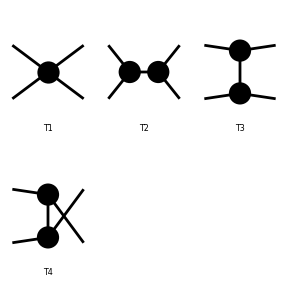

```mathematica
topsLO=CreateTopologies[0, 2->2];
topsR=CreateTopologies[0, 2->3];
(* The SelfEnergy and Tadpoles will not be relevant for the 2to2 *)
topsV=CreateTopologies[1, 2->2,ExcludeTopologies->{Tadpoles}];
topsBox=CreateTopologies[1, 2->2,ExcludeTopologies->{Tadpoles,Triangles,SelfEnergies}];
topsTri=CreateTopologies[1, 2->2,ExcludeTopologies->{Tadpoles,Boxes,SelfEnergies}];
topsSelf=CreateTopologies[1, 2->2,ExcludeTopologies->{Tadpoles,Boxes,Triangles}];
Paint[topsLO];
(*Paint[topsV];*)
(*Paint[topsR];*)
topsCT=CreateCTTopologies[1,2->2];
(*Paint[topsCT]*)
```

```mathematica
ConjugationList={Conjugate[Qu]:>Qu,Conjugate[Qd]:>Qd,Conjugate[Qe]:>Qe};
```

```mathematica
OrganiseSquaredAmpVirt[input_,nweyl_,nqed_]:=Collect[Coefficient[Collect[(2^nweyl)*input//.Abbr[]//.Subexpr[]/.MomReplace/.ConjugationList/.Replacements2to2,{D0i[__],C0i[__],B0i[__],A0[__],Finite},Simplify],Qe,nqed]*Qe^nqed/.Alfas2->ALPHAS^2/.Alfas->ALPHAS/.Alfa2->ALPHA^2/.Den[s12,mz2]->chiz/.Den[s12,Conjugate[mz2]]->Conjugate[chiz]/.Den[a_,b_]:>1/(a-b )/.Den[a_,b_,2]:>1/(a-b)^2/.IGram[a_]:> 1/a/.Diagram[a_]:>1/.Conjugate[s12]->s12,{D0i[__],C0i[__],B0i[__],A0[__],Finite},Simplify];
```

```mathematica
scalarIntegral={Finite->Finite[eps],B0i[bb0,s12,msqQ,msqQ]->B0sQQ[eps],B0i[bb0,s12,0,0]->B0s00[eps],A0[msqQ]->A0Q[eps] ,B0i[bb0,msqQ,0,msqQ]->B0Q0Q[eps],B0i[bb0,0,0,0]->0,B0i[bb0,th,0,msqQ]->B0t0Q[eps],B0i[bb0,uh,0,msqQ]->B0u0Q[eps],C0i[cc0,0,msqQ,th,0,0,msqQ]->C00Qt00Q[eps],C0i[cc0,0,msqQ,uh,0,0,msqQ]->C00Qu00Q[eps],C0i[cc0,0,s12,0,0,0,0]->C0s[eps],C0i[cc0,s12,msqQ,msqQ,0,0,msqQ]->C0sQQ00Q[eps],C0i[cc0,msqQ,s12,msqQ,0,msqQ,msqQ]->C0QsQ0QQ[eps],D0i[dd0,0,s12,msqQ,th,0,msqQ,0,0,0,msqQ]->D00sQt0Q000Q[eps],D0i[dd0,0,s12,msqQ,uh,0,msqQ,0,0,0,msqQ]->D00SQu0Q000Q[eps],C0i[cc0,0,s12,0,msqQ,msqQ,msqQ]->C00s0QQQ[eps],
C0i[cc0,0,th,msqQ,0,0,msqQ]->C00tQ00Q[eps],
C0i[cc0,0,uh,msqQ,0,0,msqQ]->C00uQ00Q[eps],
C0i[cc0,msqQ,0,th,0,msqQ,msqQ]->C0Q0t0QQ[eps],
C0i[cc0,msqQ,0,uh,0,msqQ,msqQ]->C0Q0u0QQ[eps]}
```

{Finite→Finite[eps],B0i[bb0,s12,msqQ,msqQ]→B0sQQ[eps],B0i[bb0,s12,0,0]→B0s00[eps],A0[msqQ]→A0Q[eps],B0i[bb0,msqQ,0,msqQ]→B0Q0Q[eps],B0i[bb0,0,0,0]→0,B0i[bb0,th,0,msqQ]→B0t0Q[eps],B0i[bb0,uh,0,msqQ]→B0u0Q[eps],C0i[cc0,0,msqQ,th,0,0,msqQ]→C00Qt00Q[eps],C0i[cc0,0,msqQ,uh,0,0,msqQ]→C00Qu00Q[eps],C0i[cc0,0,s12,0,0,0,0]→C0s[eps],C0i[cc0,s12,msqQ,msqQ,0,0,msqQ]→C0sQQ00Q[eps],C0i[cc0,msqQ,s12,msqQ,0,msqQ,msqQ]→C0QsQ0QQ[eps],D0i[dd0,0,s12,msqQ,th,0,msqQ,0,0,0,msqQ]→D00sQt0Q000Q[eps],D0i[dd0,0,s12,msqQ,uh,0,msqQ,0,0,0,msqQ]→D00SQu0Q000Q[eps],C0i[cc0,0,s12,0,msqQ,msqQ,msqQ]→C00s0QQQ[eps],C0i[cc0,0,th,msqQ,0,0,msqQ]→C00tQ00Q[eps],C0i[cc0,0,uh,msqQ,0,0,msqQ]→C00uQ00Q[eps],C0i[cc0,msqQ,0,th,0,msqQ,msqQ]→C0Q0t0QQ[eps],C0i[cc0,msqQ,0,uh,0,msqQ,msqQ]→C0Q0u0QQ[eps]}

```mathematica
(* Useful for shortening some expressions, keeping more invariants *)
```

```mathematica
(* Now simplify the R in powers of the electron Qed coupling *)
```

```mathematica
OrganiseSquaredAmpR[input_,nweyl_,nqed_]:=
Simplify[
Collect[
Collect[
Coefficient[(2^nweyl)*input//.Abbr[]//.SubExpr[]/.MomReplace/.ConjugationList,Qe,nqed]*Qe^nqed/.Den[s12,mz2]->chiz/.Den[s12,Conjugate[mz2]]->Conjugate[chiz]/.Den[a_,b_]:>1/(a- b )/.Replacements2to3,Eps[__],Simplify][[1]]/.PassarinoId/.EpsEtaReplace/.EpsRotReplace/.Replacements2to3,Pair[__],Simplify][[1]]/.InverseReplacements2to3]
```

```mathematica
(* For quark computation *)
```

```mathematica
MD=MD2=0;
MU=MU2=0;
```

## 1. neutrino photon interactions: nu + gamma > X

### 1.1) Squared Amplitude calculation, CC quark line: nu + gamma > lepton (3) + quarks (4,5) [Correct up to some width effect]

loading generic model file /Users/rhorry/Research/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/rhorry/Research/FeynArts-3.11/Models/SMQCD.mod

loading classes model file /Users/rhorry/Research/FeynArts-3.11/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 2 Particles insertions

> Top. 15: 2 Particles insertions

> Top. 16: 4 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 2 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

in total: 10 Particles insertions

> Top. 1 afbg/cfdgeh/fhgh.m, 0 diagrams

> Top. 2 afbg/cfdheg/fhgh.m, 0 diagrams

> Top. 3 afbg/cfdheh/fggh.m, 0 diagrams

> Top. 4 afbg/cgdheh/fgfh.m, 0 diagrams

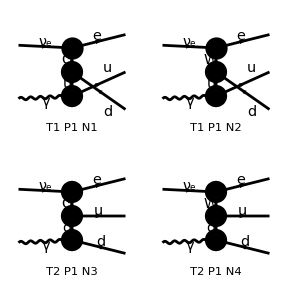

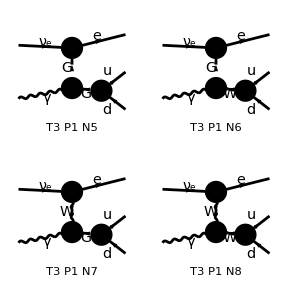

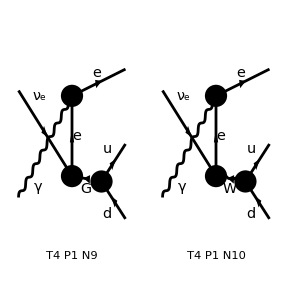

```mathematica
insertFieldseeQQbR=InsertFields[topsR,{F[1,{1}],V[1]}->{F[2,{1}],F[3,{1}],-F[4,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldseeQQbR,ColumnsXRows->{2,2}];
```

```mathematica
feynampR=CreateFeynAmp[insertFieldseeQQbR]/.MW->mw/.MW2->mw2/.SW->sw;
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 10 Particles amplitudes

```mathematica
Wprop={Den[2 Pair[k[4],k[5]],MW2]->chiw45};
```

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeR=CalcFeynAmp[feynampR,FermionChains->Chiral,Invariants->False,MomElim->5]/.SW2->sw2/.Qu->2/3/.Qd->-1/3/.Qe->-1//Simplify;
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

```mathematica
squaredAmpQQbR=PolarizationSum[AmplitudeR,GaugeTerms->True];
```

> 49 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
result=Collect[
Collect[squaredAmpQQbR//.Abbr[]//.Subexpr[]/.MomReplace/.MW2->mw2/.Replacements2to3alt/.ConjugationList/.EpsRotate/.EpsReplace/.PassarinoId2/.EpsRotate/.EpsReplace/.Replacements2to3alt/.m4sq->0/.m5sq->0/.m3sq->ME2,{Eps[__]},Simplify]/.Den[a_,b_]:>1/(a - b )/.Qe->-1/.Qu->2/3/.Qd->-1/3,{Pair[__]},Simplify];
```

```mathematica
(* For the time being drop some width effects in the numerator, but including the complex propagators *)
```

```mathematica
(* Some width issue related to the  WWgamma (or scalar vertex )*)
```

```mathematica
resultWidthSimplification=Simplify[result*chiw45*Conjugate[chiw45](s45-MW2)^2*(MW2+s12-s23-s45)^2*chiw13*Conjugate[chiw13]/.mw->MW];
```

```mathematica
(* Reconstruct the width dependence, zero width for this part *)
```

```mathematica
resultWidth0=Simplify[Coefficient[resultWidthSimplification,MW2,0]];
```

```mathematica
resultWidth1=Simplify[Coefficient[resultWidthSimplification,MW2,1]];
```

```mathematica
resultWidth2=Simplify[Coefficient[resultWidthSimplification,MW2,2]];
```

```mathematica
(* No averaging yet *)
```

```mathematica
ResultQuarks=Simplify[2^3*(resultWidth0+resultWidth1*Sqrt[mw2c*Conjugate[mw2c]]+resultWidth2*mw2c*Conjugate[mw2c])]
```

(64 Alfa Alfa2 chiw13 chiw45 π^3 chiw13^* chiw45^* (9 ME2^4 (2 s12^2 (s14-s45)+s45 (-s23^2+s23 s35-s23 s45-2 s45^2+s14 (s23+2 s45))-s12 (s23 s35-s23 s45-4 s45^2+s14 (s23+4 s45)))-3 ME2^3 (6 s12^3 (s14-s45)+s12^2 (-18 s14^2+6 s45 (2 s35+s45)+3 s14 (3 s23-4 s35+4 s45)-s23 (6 s35+11 s45))-s45 (8 s23^3+6 s45^2 (-2 s35+s45)+9 s14^2 (s23+2 s45)+s23^2 (-11 s35+14 s45)+s14 (-17 s23^2+6 s23 (2 s35-5 s45)+12 (s35-2 s45) s45)+s23 (9 s35^2-s35 s45+23 s45^2))+s12 (6 s45^2 (-4 s35+s45)+9 s14^2 (s23+4 s45)+s23^2 (-3 s35+7 s45)-3 s14 (2 s23^2-4 s23 s35+13 s23 s45-8 s35 s45+14 s45^2)+s23 (9 s35^2+5 s35 s45+34 s45^2)))+s23 (s12-s23-s45) s45 (s12^3 (-6 s14+6 s23-9 s35)+(3 s14-2 s23+3 s35) (3 s35+2 s45) (s14^2+s23^2+s35^2+2 s23 s45+2 s35 s45+2 s45^2-2 s14 (s23+s45))+s12^2 (3 s14 (7 s35+6 s45)-(2 s23-3 s35) (9 s35+8 s45))+s12 (-6 s14^3+3 s14^2 (6 s23-3 s35+4 s45)+(2 s23-3 s35) (3 s23^2+9 s35^2+6 s23 s45+16 s35 s45+10 s45^2)-6 s14 (3 s23^2+s23 (-3 s35+4 s45)+4 (s35^2+s35 s45+s45^2))))-ME2^2 (9 s12^3 (4 s14^2+s14 (-4 s23+2 s35-6 s45)+2 s45 (-s35+s45)+s23 (s35+4 s45))-3 s12^2 (18 s14^3-6 s23^2 s35+12 s23 s35^2+22 s23 s35 s45-6 s35^2 s45+23 s23 s45^2+12 s45^3-6 s14^2 (3 s23-4 s35+s45)-3 s14 (-2 s35^2+8 s35 s45+8 s45^2+s23 (2 s35+s45)))-s45 (-21 s23^4+s23^3 (48 s35-45 s45)-18 s35 (s35-2 s45) s45^2+27 s14^3 (s23+2 s45)+s23^2 (-48 s35^2+44 s35 s45-74 s45^2)+3 s23 (9 s35^3+4 s35^2 s45+34 s35 s45^2-10 s45^3)-3 s14^2 (25 s23^2+6 s45 (-4 s35+5 s45)+s23 (-15 s35+51 s45))+s14 (69 s23^3+s23^2 (-93 s35+145 s45)+18 s45 (s35^2-6 s35 s45+2 s45^2)+3 s23 (15 s35^2-37 s35 s45+54 s45^2)))+3 s12 (-s23^3 s45+9 s14^3 (s23+4 s45)+6 s45^2 (-2 s35^2+3 s35 s45+s45^2)-s23^2 (6 s35^2+3 s35 s45+19 s45^2)+s23 (9 s35^3+16 s35^2 s45+53 s35 s45^2+s45^3)-3 s14^2 (4 s23^2+16 s45 (-s35+s45)+s23 (-5 s35+23 s45))+s14 (3 s23^3+s23^2 (-12 s35+31 s45)+6 s45 (2 s35^2-11 s35 s45+s45^2)+s23 (15 s35^2-43 s35 s45+63 s45^2))))-ME2 (6 s12^4 s23 s45+3 s12^3 (6 s14^3+6 s14 s23^2-3 s14 s23 (s35-6 s45)+6 s35 s45^2+6 s14 s45 (-2 s35+s45)-6 s14^2 (2 s23-s35+2 s45)-s23^2 (3 s35+8 s45)+s23 (3 s35^2-2 s35 s45-14 s45^2))+s12^2 (-18 s14^4+9 s14^3 (3 s23-4 s35)+21 s23^3 s45-18 s35 s45^2 (s35+2 s45)+6 s14^2 (6 s23 s35-3 s35^2+8 s23 s45+6 s35 s45+9 s45^2)+s23^2 (18 s35^2+42 s35 s45+83 s45^2)+s23 (-18 s35^3-6 s35^2 s45+33 s35 s45^2+78 s45^3)-3 s14 (3 s23^3+23 s23^2 s45-12 s45 (s35^2+s35 s45-s45^2)+s23 (3 s35^2+8 s35 s45+39 s45^2)))+s45 (-6 s23^5+s23^4 (30 s35-8 s45)-18 s35^2 s45^3-9 s14^4 (s23+2 s45)+s23^3 (-30 s35^2+56 s35 s45-6 s45^2)+s23^2 (33 s35^3+16 s35^2 s45+106 s35 s45^2+12 s45^3)+s23 (-9 s35^4+3 s35^3 s45-9 s35^2 s45^2+60 s35 s45^3+12 s45^4)+3 s14^3 (11 s23^2-6 s23 (s35-4 s45)+12 s45 (-s35+s45))-s14^2 (45 s23^3+s23^2 (-69 s35+97 s45)+18 s45 (s35^2-4 s35 s45+s45^2)+3 s23 (6 s35^2-39 s35 s45+29 s45^2))+s14 (27 s23^4+36 s35 (s35-s45) s45^2+s23^3 (-81 s35+51 s45)+s23^2 (51 s35^2-135 s35 s45+58 s45^2)-6 s23 (3 s35^3-5 s35^2 s45+24 s35 s45^2-3 s45^3)))+s12 (9 s14^4 (s23+4 s45)-9 s14^3 (2 s23^2-2 s23 s35+11 s23 s45-8 s35 s45+6 s45^2)+3 s14^2 (3 s23^3+6 s35 (2 s35-7 s45) s45+s23^2 (-9 s35+22 s45)+s23 (6 s35^2-51 s35 s45+25 s45^2))+s14 (3 s23^3 (3 s35+4 s45)+18 s45^2 (-4 s35^2+2 s35 s45+s45^2)+s23^2 (-18 s35^2+69 s35 s45+10 s45^2)+3 s23 (6 s35^3-7 s35^2 s45+59 s35 s45^2+15 s45^3))-3 (5 s23^4 s45+11 s23^3 s45^2-6 s35 s45^3 (2 s35+s45)+s23^2 (3 s35^3+17 s35^2 s45+37 s35 s45^2+24 s45^3)+s23 (-3 s35^4-5 s35^3 s45-2 s35^2 s45^2+29 s35 s45^3+18 s45^4))))+mw2c (-3 ME2^3 (s12 (6 s14-s23-6 s45)-(3 s14-s23-3 s45) (6 s14-5 s23+4 s35-2 s45))+9 ME2^4 (2 s14-s23-2 s45)+ME2^2 (54 s14^3+9 s12^2 s23+14 s23^2 s35+3 s23 s35^2-26 s23^2 s45+84 s23 s35 s45-18 s35^2 s45-12 s23 s45^2+36 s35 s45^2-18 s14^2 (5 s23-4 s35+5 s45)-3 s12 (12 s14^2+2 s23^2+4 s23 s35+17 s23 s45-6 s35 s45+6 s45^2-6 s14 (2 s23-s35+3 s45))+s14 (37 s23^2+s23 (-75 s35+108 s45)+18 (s35^2-6 s35 s45+2 s45^2)))+s23 (s12^3 (-3 s14+2 s23)+s12^2 (9 s14^2-12 s14 s23+4 s23^2+15 s14 s35-10 s23 s35-6 s35 s45)+(3 s14-2 s23+3 s35) (3 s14-2 (s23+s45)) (s14^2+s23^2+s35^2+2 s23 s45+2 s35 s45+2 s45^2-2 s14 (s23+s45))+s12 (-3 s14^3+2 s14^2 (4 s23-9 s35-6 s45)+s14 (-7 s23^2+24 s23 s35-21 s35^2+14 s23 s45-12 s35 s45+6 s45^2)+2 (s23^3+6 s35 s45 (s35+s45)-2 s23^2 (2 s35+s45)+s23 (7 s35^2+4 s35 s45-2 s45^2))))-ME2 (-18 s14^4+3 s12^3 s23+10 s23^4+s12^2 s23 (-18 s14+11 s23-12 s35)-4 s23^3 s35+7 s23^2 s35^2-6 s23 s35^3+18 s23^3 s45+34 s23^2 s35 s45-27 s23 s35^2 s45+24 s23^2 s45^2+24 s23 s35 s45^2-18 s35^2 s45^2+12 s23 s45^3+9 s14^3 (3 s23-4 s35+4 s45)-s14 (27 s23^3+36 s35 s45 (-s35+s45)+5 s23^2 (3 s35+4 s45)-3 s23 (s35^2-36 s35 s45-6 s45^2))+s14^2 (8 s23^2+s23 (54 s35-33 s45)-18 (s35^2-4 s35 s45+s45^2))+s12 (18 s14^3-6 s14^2 (5 s23-3 s35+6 s45)+s14 (13 s23^2+18 s45 (-2 s35+s45)+3 s23 (5 s35+27 s45))-3 (-6 s35 s45^2+6 s23^2 (s35+2 s45)+s23 (-5 s35^2-9 s35 s45+8 s45^2))))) mw2c^*-(9 ME2^4 (-s23^2+s23 s35-2 s23 s45-4 s45^2+s14 (s23+4 s45)+s12 (-4 s14+s23+4 s45))+3 ME2^3 (8 s23^3-11 s23^2 s35+9 s23 s35^2+s12^2 (12 s14-s23-12 s45)+19 s23^2 s45-5 s23 s35 s45+40 s23 s45^2-24 s35 s45^2+12 s45^3+9 s14^2 (s23+4 s45)+s14 (-17 s23^2+3 s23 (4 s35-17 s45)+24 (s35-2 s45) s45)-s12 (36 s14^2+s23^2+2 s23 s35+27 s23 s45-24 s35 s45-6 s14 (5 s23-4 s35+6 s45)))+ME2^2 (-9 s12^3 s23-21 s23^4+48 s23^3 s35-48 s23^2 s35^2+27 s23 s35^3-45 s23^3 s45+58 s23^2 s35 s45+15 s23 s35^2 s45-100 s23^2 s45^2+186 s23 s35 s45^2-36 s35^2 s45^2-42 s23 s45^3+72 s35 s45^3+27 s14^3 (s23+4 s45)-3 s14^2 (25 s23^2-15 s23 s35+81 s23 s45-48 s35 s45+60 s45^2)+3 s12^2 (24 s14^2+12 s45 (-s35+s45)-12 s14 (2 s23-s35+3 s45)+s23 (7 s35+32 s45))+s14 (69 s23^3+s23^2 (-93 s35+182 s45)+36 s45 (s35^2-6 s35 s45+2 s45^2)+3 s23 (15 s35^2-62 s35 s45+90 s45^2))-3 s12 (36 s14^3+8 s23^3-12 s14^2 (4 s23-4 s35+3 s45)-s23^2 (12 s35+5 s45)+12 s45 (-s35^2+s35 s45+s45^2)+s23 (13 s35^2+51 s35 s45+24 s45^2)+s14 (4 s23^2+s23 (-31 s35+33 s45)+12 (s35^2-5 s35 s45-s45^2))))-s23 (-3 s12^4 (s14-s23)-9 s14^4 s45-(2 s23-3 s35) (s23+s45) (3 s35+4 s45) (s23^2+s35^2+2 s23 s45+2 s35 s45+2 s45^2)+s12^3 (9 s14^2+6 s23^2-15 s35 s45+2 s23 (-9 s35+s45)-3 s14 (5 s23-5 s35+s45))+s14^3 (30 s45^2+9 s23 (s35+4 s45))+s12^2 (-3 s14^3+3 s23^3+3 s14^2 (3 s23-6 s35-7 s45)-2 s23^2 (9 s35+7 s45)+3 s35 s45 (13 s35+14 s45)+2 s23 (18 s35^2+10 s35 s45-9 s45^2)-3 s14 (3 s23^2-13 s23 s35+7 s35^2-12 s23 s45+2 s35 s45-8 s45^2))-s14^2 (6 s45^2 (s35+7 s45)+s23^2 (24 s35+53 s45)+s23 (-9 s35^2+12 s35 s45+86 s45^2))+s14 (s23^3 (21 s35+34 s45)-6 s45^2 (s35^2-4 s45^2)+s23^2 (-18 s35^2+18 s35 s45+80 s45^2)+s23 (9 s35^3+18 s35 s45^2+76 s45^3))+s12 (9 s14^4+6 s23^4-4 s23^3 (3 s35-5 s45)-3 s14^3 (11 s23-3 s35+9 s45)-3 s35 s45 (11 s35^2+24 s35 s45+18 s45^2)+s23^2 (18 s35^2+s35 s45+44 s45^2)+s14^2 (45 s23^2-30 s23 s35+9 s35^2+74 s23 s45+3 s35 s45+54 s45^2)-2 s23 (15 s35^3+23 s35^2 s45+17 s35 s45^2-16 s45^3)-s14 (27 s23^3-9 s35^3-9 s35^2 s45-6 s35 s45^2+42 s45^3+s23^2 (-33 s35+67 s45)+s23 (33 s35^2+12 s35 s45+100 s45^2))))+ME2 (3 s12^4 s23+6 s23^5-30 s23^4 s35+30 s23^3 s35^2-33 s23^2 s35^3+9 s23 s35^4-2 s23^4 s45-52 s23^3 s35 s45-23 s23^2 s35^2 s45+3 s23 s35^3 s45-12 s23^3 s45^2-140 s23^2 s35 s45^2+36 s23 s35^2 s45^2-36 s23^2 s45^3-84 s23 s35 s45^3+36 s35^2 s45^3-24 s23 s45^4+3 s12^3 s23 (-6 s14+5 s23-4 s35+s45)+9 s14^4 (s23+4 s45)-3 s14^3 (11 s23^2+24 s45 (-s35+s45)+s23 (-6 s35+33 s45))+s14^2 (45 s23^3+s23^2 (-69 s35+89 s45)+36 s45 (s35^2-4 s35 s45+s45^2)+3 s23 (6 s35^2-57 s35 s45+40 s45^2))+s14 (-27 s23^4+3 s23^3 (27 s35-8 s45)+72 s35 s45^2 (-s35+s45)+s23^2 (-51 s35^2+150 s35 s45-38 s45^2)+3 s23 s35 (6 s35^2-11 s35 s45+84 s45^2))+s12^2 (36 s14^3+6 s23^3+36 s35 s45^2-6 s14^2 (11 s23-6 s35+12 s45)-s23^2 (51 s35+76 s45)+3 s23 (8 s35^2+11 s35 s45-20 s45^2)+3 s14 (8 s23^2+12 s45 (-2 s35+s45)+s23 (2 s35+51 s45)))+s12 (-36 s14^4+18 s14^3 (3 s23-4 s35+2 s45)+3 s14^2 (8 s23^2+3 s23 (10 s35+s45)+12 (-s35^2+3 s35 s45+s45^2))-s14 (66 s23^3+s23^2 (-21 s35+95 s45)+36 s45 (-2 s35^2+s45^2)+6 s23 (s35^2+26 s35 s45+27 s45^2))+3 (8 s23^4-12 s35 s45^2 (s35+s45)+s23^3 (-12 s35+17 s45)+s23^2 (23 s35^2+31 s35 s45+42 s45^2)+s23 (-8 s35^3-13 s35^2 s45+8 s35 s45^2+26 s45^3))))) √(mw2c mw2c^*)))/(3 s23^2 (ME2-s12+s14+s35) (ME2+s14-s23+s35) sw^2 (sw^*)^2)

```mathematica
(* Implement this thing *)
```

```mathematica
prefac=4 Alfa Alfa2 π^3 chiw13*chiw45*Conjugate[chiw13*chiw45]
```

4 Alfa Alfa2 chiw13 chiw45 π^3 chiw13^* chiw45^*

```mathematica
CForm[prefac/.Alfa->ALPHA/.Alfa2->ALPHA*Conjugate[ALPHA]/.Power->pow/.Conjugate->conj/.Pi->pi]
```

4*chiw13*chiw45*conj(ALPHA)*conj(chiw13)*conj(chiw45)*pow(ALPHA,2)*pow(pi,3)

```mathematica
CForm[ResultQuarks/prefac/.mw2->mw2c/.ME2->mlsq/.sw2->sw2c/.sw->Sqrt[sw2]]/.Power->pow/.Conjugate->conj/.sw2->SW2
```

(16*pow(s23,-2)*pow(mlsq - s12 + s14 + s35,-1)*pow(mlsq + s14 - s23 + s35,-1)*pow(SW2,-1)*
     (9*pow(mlsq,4)*(2*(s14 - s45)*pow(s12,2) - 
          s12*(s23*s35 - s23*s45 + s14*(s23 + 4*s45) - 4*pow(s45,2)) + 
          s45*(s23*s35 - s23*s45 + s14*(s23 + 2*s45) - pow(s23,2) - 2*pow(s45,2))) - 
       3*pow(mlsq,3)*(6*(s14 - s45)*pow(s12,3) + 
          pow(s12,2)*(6*s45*(2*s35 + s45) + 3*s14*(3*s23 - 4*s35 + 4*s45) - s23*(6*s35 + 11*s45) - 
             18*pow(s14,2)) - s45*(9*(s23 + 2*s45)*pow(s14,2) + 
             s14*(6*s23*(2*s35 - 5*s45) + 12*(s35 - 2*s45)*s45 - 17*pow(s23,2)) + 
             (-11*s35 + 14*s45)*pow(s23,2) + 8*pow(s23,3) + 6*(-2*s35 + s45)*pow(s45,2) + 
             s23*(-(s35*s45) + 9*pow(s35,2) + 23*pow(s45,2))) + 
          s12*(9*(s23 + 4*s45)*pow(s14,2) + (-3*s35 + 7*s45)*pow(s23,2) + 
             6*(-4*s35 + s45)*pow(s45,2) - 
             3*s14*(-4*s23*s35 + 13*s23*s45 - 8*s35*s45 + 2*pow(s23,2) + 14*pow(s45,2)) + 
             s23*(5*s35*s45 + 9*pow(s35,2) + 34*pow(s45,2)))) + 
       s23*(s12 - s23 - s45)*s45*((3*s14*(7*s35 + 6*s45) - (2*s23 - 3*s35)*(9*s35 + 8*s45))*
           pow(s12,2) + (-6*s14 + 6*s23 - 9*s35)*pow(s12,3) + 
          (3*s14 - 2*s23 + 3*s35)*(3*s35 + 2*s45)*
           (2*s23*s45 + 2*s35*s45 - 2*s14*(s23 + s45) + pow(s14,2) + pow(s23,2) + pow(s35,2) + 
             2*pow(s45,2)) + s12*(3*(6*s23 - 3*s35 + 4*s45)*pow(s14,2) - 6*pow(s14,3) + 
             (2*s23 - 3*s35)*(6*s23*s45 + 16*s35*s45 + 3*pow(s23,2) + 9*pow(s35,2) + 10*pow(s45,2)) - 
             6*s14*(s23*(-3*s35 + 4*s45) + 3*pow(s23,2) + 4*(s35*s45 + pow(s35,2) + pow(s45,2))))) + 
       mw2c*conj(mw2c)*(-3*(s12*(6*s14 - s23 - 6*s45) - 
             (3*s14 - s23 - 3*s45)*(6*s14 - 5*s23 + 4*s35 - 2*s45))*pow(mlsq,3) + 
          9*(2*s14 - s23 - 2*s45)*pow(mlsq,4) + 
          pow(mlsq,2)*(84*s23*s35*s45 + 9*s23*pow(s12,2) - 18*(5*s23 - 4*s35 + 5*s45)*pow(s14,2) + 
             54*pow(s14,3) + 14*s35*pow(s23,2) - 26*s45*pow(s23,2) + 3*s23*pow(s35,2) - 
             18*s45*pow(s35,2) - 12*s23*pow(s45,2) + 36*s35*pow(s45,2) - 
             3*s12*(4*s23*s35 + 17*s23*s45 - 6*s35*s45 - 6*s14*(2*s23 - s35 + 3*s45) + 12*pow(s14,2) + 
                2*pow(s23,2) + 6*pow(s45,2)) + 
             s14*(s23*(-75*s35 + 108*s45) + 37*pow(s23,2) + 
                18*(-6*s35*s45 + pow(s35,2) + 2*pow(s45,2)))) + 
          s23*((-3*s14 + 2*s23)*pow(s12,3) + 
             pow(s12,2)*(-12*s14*s23 + 15*s14*s35 - 10*s23*s35 - 6*s35*s45 + 9*pow(s14,2) + 
                4*pow(s23,2)) + (3*s14 - 2*s23 + 3*s35)*(3*s14 - 2*(s23 + s45))*
              (2*s23*s45 + 2*s35*s45 - 2*s14*(s23 + s45) + pow(s14,2) + pow(s23,2) + pow(s35,2) + 
                2*pow(s45,2)) + s12*(2*(4*s23 - 9*s35 - 6*s45)*pow(s14,2) - 3*pow(s14,3) + 
                2*(6*s35*s45*(s35 + s45) - 2*(2*s35 + s45)*pow(s23,2) + pow(s23,3) + 
                   s23*(4*s35*s45 + 7*pow(s35,2) - 2*pow(s45,2))) + 
                s14*(24*s23*s35 + 14*s23*s45 - 12*s35*s45 - 7*pow(s23,2) - 21*pow(s35,2) + 
                   6*pow(s45,2)))) - mlsq*
           (s23*(-18*s14 + 11*s23 - 12*s35)*pow(s12,2) + 3*s23*pow(s12,3) + 
             9*(3*s23 - 4*s35 + 4*s45)*pow(s14,3) - 18*pow(s14,4) + 34*s35*s45*pow(s23,2) - 
             4*s35*pow(s23,3) + 18*s45*pow(s23,3) + 10*pow(s23,4) - 27*s23*s45*pow(s35,2) + 
             7*pow(s23,2)*pow(s35,2) - 6*s23*pow(s35,3) - 
             s14*(36*s35*s45*(-s35 + s45) + 5*(3*s35 + 4*s45)*pow(s23,2) + 27*pow(s23,3) - 
                3*s23*(-36*s35*s45 + pow(s35,2) - 6*pow(s45,2))) + 24*s23*s35*pow(s45,2) + 
             24*pow(s23,2)*pow(s45,2) - 18*pow(s35,2)*pow(s45,2) + 
             pow(s14,2)*(s23*(54*s35 - 33*s45) + 8*pow(s23,2) - 
                18*(-4*s35*s45 + pow(s35,2) + pow(s45,2))) + 
             s12*(-6*(5*s23 - 3*s35 + 6*s45)*pow(s14,2) + 18*pow(s14,3) + 
                s14*(18*s45*(-2*s35 + s45) + 3*s23*(5*s35 + 27*s45) + 13*pow(s23,2)) - 
                3*(6*(s35 + 2*s45)*pow(s23,2) - 6*s35*pow(s45,2) + 
                   s23*(-9*s35*s45 - 5*pow(s35,2) + 8*pow(s45,2)))) + 12*s23*pow(s45,3))) - 
       pow(mlsq,2)*(9*pow(s12,3)*(s14*(-4*s23 + 2*s35 - 6*s45) + 2*s45*(-s35 + s45) + 
             s23*(s35 + 4*s45) + 4*pow(s14,2)) - 
          s45*(27*(s23 + 2*s45)*pow(s14,3) - 
             3*pow(s14,2)*(6*s45*(-4*s35 + 5*s45) + s23*(-15*s35 + 51*s45) + 25*pow(s23,2)) + 
             (48*s35 - 45*s45)*pow(s23,3) - 21*pow(s23,4) + 
             pow(s23,2)*(44*s35*s45 - 48*pow(s35,2) - 74*pow(s45,2)) - 
             18*s35*(s35 - 2*s45)*pow(s45,2) + 
             s14*((-93*s35 + 145*s45)*pow(s23,2) + 69*pow(s23,3) + 
                18*s45*(-6*s35*s45 + pow(s35,2) + 2*pow(s45,2)) + 
                3*s23*(-37*s35*s45 + 15*pow(s35,2) + 54*pow(s45,2))) + 
             3*s23*(4*s45*pow(s35,2) + 9*pow(s35,3) + 34*s35*pow(s45,2) - 10*pow(s45,3))) - 
          3*pow(s12,2)*(22*s23*s35*s45 - 6*(3*s23 - 4*s35 + s45)*pow(s14,2) + 18*pow(s14,3) - 
             6*s35*pow(s23,2) + 12*s23*pow(s35,2) - 6*s45*pow(s35,2) + 23*s23*pow(s45,2) - 
             3*s14*(8*s35*s45 + s23*(2*s35 + s45) - 2*pow(s35,2) + 8*pow(s45,2)) + 12*pow(s45,3)) + 
          3*s12*(9*(s23 + 4*s45)*pow(s14,3) - 
             3*pow(s14,2)*(16*s45*(-s35 + s45) + s23*(-5*s35 + 23*s45) + 4*pow(s23,2)) - 
             s45*pow(s23,3) + 6*pow(s45,2)*(3*s35*s45 - 2*pow(s35,2) + pow(s45,2)) - 
             pow(s23,2)*(3*s35*s45 + 6*pow(s35,2) + 19*pow(s45,2)) + 
             s14*((-12*s35 + 31*s45)*pow(s23,2) + 3*pow(s23,3) + 
                6*s45*(-11*s35*s45 + 2*pow(s35,2) + pow(s45,2)) + 
                s23*(-43*s35*s45 + 15*pow(s35,2) + 63*pow(s45,2))) + 
             s23*(16*s45*pow(s35,2) + 9*pow(s35,3) + 53*s35*pow(s45,2) + pow(s45,3)))) - 
       mlsq*(6*s23*s45*pow(s12,4) + 3*pow(s12,3)*
           (-3*s14*s23*(s35 - 6*s45) + 6*s14*s45*(-2*s35 + s45) - 6*(2*s23 - s35 + 2*s45)*pow(s14,2) + 
             6*pow(s14,3) + 6*s14*pow(s23,2) - (3*s35 + 8*s45)*pow(s23,2) + 
             s23*(-2*s35*s45 + 3*pow(s35,2) - 14*pow(s45,2)) + 6*s35*pow(s45,2)) + 
          pow(s12,2)*(9*(3*s23 - 4*s35)*pow(s14,3) - 18*pow(s14,4) + 21*s45*pow(s23,3) - 
             18*s35*(s35 + 2*s45)*pow(s45,2) + 
             6*pow(s14,2)*(6*s23*s35 + 8*s23*s45 + 6*s35*s45 - 3*pow(s35,2) + 9*pow(s45,2)) + 
             pow(s23,2)*(42*s35*s45 + 18*pow(s35,2) + 83*pow(s45,2)) - 
             3*s14*(23*s45*pow(s23,2) + 3*pow(s23,3) - 12*s45*(s35*s45 + pow(s35,2) - pow(s45,2)) + 
                s23*(8*s35*s45 + 3*pow(s35,2) + 39*pow(s45,2))) + 
             s23*(-6*s45*pow(s35,2) - 18*pow(s35,3) + 33*s35*pow(s45,2) + 78*pow(s45,3))) + 
          s45*(-9*(s23 + 2*s45)*pow(s14,4) + 
             3*pow(s14,3)*(-6*s23*(s35 - 4*s45) + 12*s45*(-s35 + s45) + 11*pow(s23,2)) + 
             (30*s35 - 8*s45)*pow(s23,4) - 6*pow(s23,5) + 
             pow(s23,3)*(56*s35*s45 - 30*pow(s35,2) - 6*pow(s45,2)) - 
             pow(s14,2)*((-69*s35 + 97*s45)*pow(s23,2) + 45*pow(s23,3) + 
                18*s45*(-4*s35*s45 + pow(s35,2) + pow(s45,2)) + 
                3*s23*(-39*s35*s45 + 6*pow(s35,2) + 29*pow(s45,2))) + 
             s14*((-81*s35 + 51*s45)*pow(s23,3) + 27*pow(s23,4) + 36*s35*(s35 - s45)*pow(s45,2) + 
                pow(s23,2)*(-135*s35*s45 + 51*pow(s35,2) + 58*pow(s45,2)) - 
                6*s23*(-5*s45*pow(s35,2) + 3*pow(s35,3) + 24*s35*pow(s45,2) - 3*pow(s45,3))) - 
             18*pow(s35,2)*pow(s45,3) + pow(s23,2)*
              (16*s45*pow(s35,2) + 33*pow(s35,3) + 106*s35*pow(s45,2) + 12*pow(s45,3)) + 
             s23*(3*s45*pow(s35,3) - 9*pow(s35,4) - 9*pow(s35,2)*pow(s45,2) + 60*s35*pow(s45,3) + 
                12*pow(s45,4))) + s12*(9*(s23 + 4*s45)*pow(s14,4) - 
             9*pow(s14,3)*(-2*s23*s35 + 11*s23*s45 - 8*s35*s45 + 2*pow(s23,2) + 6*pow(s45,2)) + 
             3*pow(s14,2)*(6*s35*(2*s35 - 7*s45)*s45 + (-9*s35 + 22*s45)*pow(s23,2) + 3*pow(s23,3) + 
                s23*(-51*s35*s45 + 6*pow(s35,2) + 25*pow(s45,2))) + 
             s14*(3*(3*s35 + 4*s45)*pow(s23,3) + 
                18*pow(s45,2)*(2*s35*s45 - 4*pow(s35,2) + pow(s45,2)) + 
                pow(s23,2)*(69*s35*s45 - 18*pow(s35,2) + 10*pow(s45,2)) + 
                3*s23*(-7*s45*pow(s35,2) + 6*pow(s35,3) + 59*s35*pow(s45,2) + 15*pow(s45,3))) - 
             3*(5*s45*pow(s23,4) + 11*pow(s23,3)*pow(s45,2) - 6*s35*(2*s35 + s45)*pow(s45,3) + 
                pow(s23,2)*(17*s45*pow(s35,2) + 3*pow(s35,3) + 37*s35*pow(s45,2) + 24*pow(s45,3)) + 
                s23*(-5*s45*pow(s35,3) - 3*pow(s35,4) - 2*pow(s35,2)*pow(s45,2) + 29*s35*pow(s45,3) + 
                   18*pow(s45,4))))) - (9*pow(mlsq,4)*
           (s23*s35 - 2*s23*s45 + s14*(s23 + 4*s45) + s12*(-4*s14 + s23 + 4*s45) - pow(s23,2) - 
             4*pow(s45,2)) + 3*pow(mlsq,3)*
           (-5*s23*s35*s45 + (12*s14 - s23 - 12*s45)*pow(s12,2) + 9*(s23 + 4*s45)*pow(s14,2) + 
             s14*(3*s23*(4*s35 - 17*s45) + 24*(s35 - 2*s45)*s45 - 17*pow(s23,2)) - 11*s35*pow(s23,2) + 
             19*s45*pow(s23,2) - s12*(2*s23*s35 + 27*s23*s45 - 24*s35*s45 - 
                6*s14*(5*s23 - 4*s35 + 6*s45) + 36*pow(s14,2) + pow(s23,2)) + 8*pow(s23,3) + 
             9*s23*pow(s35,2) + 40*s23*pow(s45,2) - 24*s35*pow(s45,2) + 12*pow(s45,3)) + 
          pow(mlsq,2)*(-9*s23*pow(s12,3) + 
             3*pow(s12,2)*(12*s45*(-s35 + s45) - 12*s14*(2*s23 - s35 + 3*s45) + s23*(7*s35 + 32*s45) + 
                24*pow(s14,2)) + 27*(s23 + 4*s45)*pow(s14,3) + 58*s35*s45*pow(s23,2) + 
             48*s35*pow(s23,3) - 45*s45*pow(s23,3) - 21*pow(s23,4) + 15*s23*s45*pow(s35,2) - 
             48*pow(s23,2)*pow(s35,2) + 27*s23*pow(s35,3) + 186*s23*s35*pow(s45,2) - 
             100*pow(s23,2)*pow(s45,2) - 36*pow(s35,2)*pow(s45,2) - 
             3*pow(s14,2)*(-15*s23*s35 + 81*s23*s45 - 48*s35*s45 + 25*pow(s23,2) + 60*pow(s45,2)) - 
             3*s12*(-12*(4*s23 - 4*s35 + 3*s45)*pow(s14,2) + 36*pow(s14,3) - 
                (12*s35 + 5*s45)*pow(s23,2) + 8*pow(s23,3) + 
                s14*(s23*(-31*s35 + 33*s45) + 4*pow(s23,2) + 
                   12*(-5*s35*s45 + pow(s35,2) - pow(s45,2))) + 
                12*s45*(s35*s45 - pow(s35,2) + pow(s45,2)) + 
                s23*(51*s35*s45 + 13*pow(s35,2) + 24*pow(s45,2))) + 
             s14*((-93*s35 + 182*s45)*pow(s23,2) + 69*pow(s23,3) + 
                36*s45*(-6*s35*s45 + pow(s35,2) + 2*pow(s45,2)) + 
                3*s23*(-62*s35*s45 + 15*pow(s35,2) + 90*pow(s45,2))) - 42*s23*pow(s45,3) + 
             72*s35*pow(s45,3)) - s23*(-3*(s14 - s23)*pow(s12,4) - 9*s45*pow(s14,4) + 
             pow(s12,3)*(-15*s35*s45 + 2*s23*(-9*s35 + s45) - 3*s14*(5*s23 - 5*s35 + s45) + 
                9*pow(s14,2) + 6*pow(s23,2)) + 
             pow(s12,2)*(3*s35*s45*(13*s35 + 14*s45) + 3*(3*s23 - 6*s35 - 7*s45)*pow(s14,2) - 
                3*pow(s14,3) - 2*(9*s35 + 7*s45)*pow(s23,2) + 3*pow(s23,3) + 
                2*s23*(10*s35*s45 + 18*pow(s35,2) - 9*pow(s45,2)) - 
                3*s14*(-13*s23*s35 - 12*s23*s45 + 2*s35*s45 + 3*pow(s23,2) + 7*pow(s35,2) - 
                   8*pow(s45,2))) - (2*s23 - 3*s35)*(s23 + s45)*(3*s35 + 4*s45)*
              (2*s23*s45 + 2*s35*s45 + pow(s23,2) + pow(s35,2) + 2*pow(s45,2)) + 
             pow(s14,3)*(9*s23*(s35 + 4*s45) + 30*pow(s45,2)) - 
             pow(s14,2)*((24*s35 + 53*s45)*pow(s23,2) + 6*(s35 + 7*s45)*pow(s45,2) + 
                s23*(12*s35*s45 - 9*pow(s35,2) + 86*pow(s45,2))) + 
             s12*(-3*(11*s23 - 3*s35 + 9*s45)*pow(s14,3) + 9*pow(s14,4) - 
                4*(3*s35 - 5*s45)*pow(s23,3) + 6*pow(s23,4) - 
                3*s35*s45*(24*s35*s45 + 11*pow(s35,2) + 18*pow(s45,2)) + 
                pow(s23,2)*(s35*s45 + 18*pow(s35,2) + 44*pow(s45,2)) + 
                pow(s14,2)*(-30*s23*s35 + 74*s23*s45 + 3*s35*s45 + 45*pow(s23,2) + 9*pow(s35,2) + 
                   54*pow(s45,2)) - 2*s23*
                 (23*s45*pow(s35,2) + 15*pow(s35,3) + 17*s35*pow(s45,2) - 16*pow(s45,3)) - 
                s14*((-33*s35 + 67*s45)*pow(s23,2) + 27*pow(s23,3) - 9*s45*pow(s35,2) - 9*pow(s35,3) - 
                   6*s35*pow(s45,2) + s23*(12*s35*s45 + 33*pow(s35,2) + 100*pow(s45,2)) + 42*pow(s45,3)
                   )) + s14*((21*s35 + 34*s45)*pow(s23,3) - 6*(pow(s35,2) - 4*pow(s45,2))*pow(s45,2) + 
                pow(s23,2)*(18*s35*s45 - 18*pow(s35,2) + 80*pow(s45,2)) + 
                s23*(9*pow(s35,3) + 18*s35*pow(s45,2) + 76*pow(s45,3)))) + 
          mlsq*(3*s23*(-6*s14 + 5*s23 - 4*s35 + s45)*pow(s12,3) + 3*s23*pow(s12,4) + 
             9*(s23 + 4*s45)*pow(s14,4) - 
             3*pow(s14,3)*(24*s45*(-s35 + s45) + s23*(-6*s35 + 33*s45) + 11*pow(s23,2)) - 
             52*s35*s45*pow(s23,3) - 30*s35*pow(s23,4) - 2*s45*pow(s23,4) + 6*pow(s23,5) - 
             23*s45*pow(s23,2)*pow(s35,2) + 30*pow(s23,3)*pow(s35,2) + 3*s23*s45*pow(s35,3) - 
             33*pow(s23,2)*pow(s35,3) + 9*s23*pow(s35,4) - 140*s35*pow(s23,2)*pow(s45,2) - 
             12*pow(s23,3)*pow(s45,2) + 36*s23*pow(s35,2)*pow(s45,2) + 
             pow(s12,2)*(-6*(11*s23 - 6*s35 + 12*s45)*pow(s14,2) + 36*pow(s14,3) - 
                (51*s35 + 76*s45)*pow(s23,2) + 
                3*s14*(12*s45*(-2*s35 + s45) + s23*(2*s35 + 51*s45) + 8*pow(s23,2)) + 6*pow(s23,3) + 
                3*s23*(11*s35*s45 + 8*pow(s35,2) - 20*pow(s45,2)) + 36*s35*pow(s45,2)) + 
             pow(s14,2)*((-69*s35 + 89*s45)*pow(s23,2) + 45*pow(s23,3) + 
                36*s45*(-4*s35*s45 + pow(s35,2) + pow(s45,2)) + 
                3*s23*(-57*s35*s45 + 6*pow(s35,2) + 40*pow(s45,2))) + 
             s14*(3*(27*s35 - 8*s45)*pow(s23,3) - 27*pow(s23,4) + 
                pow(s23,2)*(150*s35*s45 - 51*pow(s35,2) - 38*pow(s45,2)) + 
                72*s35*(-s35 + s45)*pow(s45,2) + 3*s23*s35*(-11*s35*s45 + 6*pow(s35,2) + 84*pow(s45,2))
                ) - 84*s23*s35*pow(s45,3) - 36*pow(s23,2)*pow(s45,3) + 36*pow(s35,2)*pow(s45,3) + 
             s12*(18*(3*s23 - 4*s35 + 2*s45)*pow(s14,3) - 36*pow(s14,4) + 
                3*pow(s14,2)*(3*s23*(10*s35 + s45) + 8*pow(s23,2) + 
                   12*(3*s35*s45 - pow(s35,2) + pow(s45,2))) - 
                s14*((-21*s35 + 95*s45)*pow(s23,2) + 66*pow(s23,3) + 
                   36*s45*(-2*pow(s35,2) + pow(s45,2)) + 
                   6*s23*(26*s35*s45 + pow(s35,2) + 27*pow(s45,2))) + 
                3*((-12*s35 + 17*s45)*pow(s23,3) + 8*pow(s23,4) - 12*s35*(s35 + s45)*pow(s45,2) + 
                   pow(s23,2)*(31*s35*s45 + 23*pow(s35,2) + 42*pow(s45,2)) + 
                   s23*(-13*s45*pow(s35,2) - 8*pow(s35,3) + 8*s35*pow(s45,2) + 26*pow(s45,3)))) - 
             24*s23*pow(s45,4)))*pow(mw2c*conj(mw2c),1/2.))*pow(conj(pow(SW2,1/2.)),-2))/3.

### 1.1**) Squared Amplitude calculation, CC quark line: nu + lepton > quarks (3,4) + photon(5)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 4 Particles insertions

> Top. 12: 2 Particles insertions

> Top. 13: 2 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 2 Particles insertions

in total: 10 Particles insertions

> Top. 1 afbf/cgdgeh/fhgh.m, 0 diagrams

> Top. 2 afbf/cgdheg/fhgh.m, 0 diagrams

> Top. 3 afbf/cgdheh/fggh.m, 0 diagrams

> Top. 4 afbg/chdheg/fgfh.m, 0 diagrams

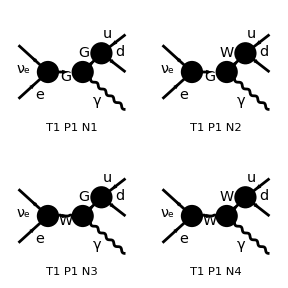

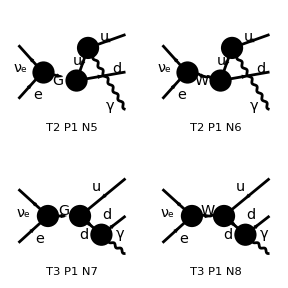

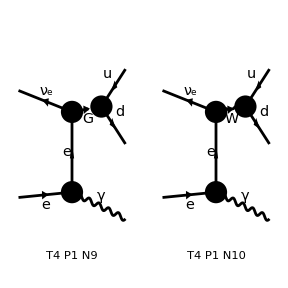

```mathematica
insertFieldseeQQbR=InsertFields[topsR,{-F[1,{1}],F[2,{1}]}->{-F[3,{1}],F[4,{1}],V[1]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldseeQQbR,ColumnsXRows->{2,2}];
```

```mathematica
feynampR=CreateFeynAmp[insertFieldseeQQbR];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 10 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeR=CalcFeynAmp[feynampR,FermionChains->Chiral,Invariants->False,MomElim->4]/.MW2->mw2/.SW2->sw2;
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

```mathematica
squaredAmpQQbR=PolarizationSum[AmplitudeR,GaugeTerms->True];
```

> 144 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
result=Collect[
Collect[squaredAmpQQbR//.Abbr[]//.Subexpr[]/.MomReplace/.Replacements2to3/.ConjugationList/.EpsRotReplace/.EpsEtaReplace/.PassarinoId/.Replacements2to3/.m4sq->0/.m5sq->0/.m3sq->0/.ME2->0/.Den[a_,b_]:>1/(a - b ),{Eps[__]},Simplify][[1]]/.Qd->Qe/3/.Qu->-Qe*2/3/.Qe->-1/.Pair[eta[5],k[2]]->Pair[eta[5],k[3]]+Pair[eta[5],k[4]]+Pair[eta[5],k[5]]-Pair[eta[5],k[1]],{Pair[__]},Simplify][[1]]
```

(4 Alfa Alfa2 π^3 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) (2 s12 (s12-s15-s25) ((3 s13+s15-3 s24-2 s25) (3 s24+2 s25)+s12 (-6 s13+6 s24+4 s25))+mw2 (4 s12^2 (3 s13-3 s24-2 s25)+s12 (-9 s13^2+9 s15 s24+9 s24^2+8 s15 s25+18 s24 s25+8 s25^2-3 s13 (5 s15+2 s25))+3 (3 s13^2 s25+s15 (s15-3 s24-2 s25) (s24+s25)+s13 (3 s15 s24+4 s15 s25-3 s24 s25-2 s25^2)))+(4 s12^2 (3 s13-3 s24-2 s25)+s12 (-9 s13^2+9 s15 s24+9 s24^2+8 s15 s25+18 s24 s25+8 s25^2-3 s13 (5 s15+2 s25))+2 mw2 (9 s13^2+s13 (9 s15-9 s24-6 s25)-6 s15 (s24+s25)+s12 (-6 s13+6 s24+4 s25))+3 (3 s13^2 s25+s15 (s15-3 s24-2 s25) (s24+s25)+s13 (3 s15 s24+4 s15 s25-3 s24 s25-2 s25^2))) mw2^*))/(3 (mw2-s12) (s13+s15-s24) (s13-s24-s25) s25 (mw2-s12+s15+s25) sw2 (s12-mw2^*) (-s12+s15+s25+mw2^*) sw2^*)+(Alfa Alfa2 π^3 (s15+s25) (12 s13^2+s15^2-7 s15 s24+12 s24^2+s13 (7 s15-24 s24-11 s25)-3 s15 s25+11 s24 s25+2 s25^2) (mw2-mw2^*) ((s13-s24-s25) Eps[eta[5],k[1],k[2],k[3]]+(s13+s15-s24) Eps[eta[5],k[1],k[2],k[4]]-s25 Eps[eta[5],k[1],k[3],k[4]]+s15 Eps[eta[5],k[2],k[3],k[4]]) Pair[eta[5],k[1]])/((mw2-s12) (s13+s15-s24) s25 (mw2-s12+s15+s25) (-s13+s24+s25) sw2 (s12-mw2^*) (-s12+s15+s25+mw2^*) sw2^* Pair[eta[5],k[5]]^2)+1/Pair[eta[5],k[5]]^2((Alfa Alfa2 π^3 (-3 s15^3+12 s13^2 (s15+s25)+s15^2 (5 s24+7 s25)+s15 (12 s24^2+s24 s25-6 s25^2)+4 s25 (3 s24^2+5 s24 s25+2 s25^2)-s13 (5 s15^2+s15 (24 s24+s25)+4 s25 (6 s24+5 s25))) (mw2-mw2^*) ((s13-s24-s25) Eps[eta[5],k[1],k[2],k[3]]+(s13+s15-s24) Eps[eta[5],k[1],k[2],k[4]]-s25 Eps[eta[5],k[1],k[3],k[4]]+s15 Eps[eta[5],k[2],k[3],k[4]]) Pair[eta[5],k[3]])/((mw2-s12) (s13+s15-s24) (s13-s24-s25) s25 (mw2-s12+s15+s25) sw2 (s12-mw2^*) (-s12+s15+s25+mw2^*) sw2^*)+(Alfa Alfa2 π^3 (4 s13+s15-4 s24) (3 s13+s15-3 s24-2 s25) (s15+s25) (mw2-mw2^*) ((s13-s24-s25) Eps[eta[5],k[1],k[2],k[3]]+(s13+s15-s24) Eps[eta[5],k[1],k[2],k[4]]-s25 Eps[eta[5],k[1],k[3],k[4]]+s15 Eps[eta[5],k[2],k[3],k[4]]) Pair[eta[5],k[4]])/((mw2-s12) (s13+s15-s24) (s13-s24-s25) s25 (mw2-s12+s15+s25) sw2 (s12-mw2^*) (-s12+s15+s25+mw2^*) sw2^*))+(Alfa Alfa2 π^3 (3 s13+s15-3 s24-2 s25) (mw2-mw2^*) ((-8 s13^3+s13^2 (-12 s15+8 s24+12 s25)+s13 (-7 s15^2+8 s24^2+12 s24 s25+3 s25^2+12 s15 (s24+s25))+2 (2 s15^3+s15 s25 (2 s24+s25)+s15^2 (4 s24+5 s25)-2 (2 s24^3+6 s24^2 s25+5 s24 s25^2+s25^3))+s12 (16 s13^2-4 s15^2-16 s15 s24+16 s24^2-15 s15 s25+32 s24 s25+13 s25^2+16 s13 (s15-2 (s24+s25)))) Eps[eta[5],k[1],k[2],k[3]]+(-8 s13^3-7 s15^3+4 s15^2 s24+8 s15 s24^2-8 s24^3+2 s15^2 s25+8 s15 s24 s25-16 s24^2 s25+9 s15 s25^2-12 s24 s25^2+4 s13^2 (-5 s15+2 s24+s25)+s12 (16 s13^2+15 s15^2-28 s15 s24+16 s24^2+4 s13 (7 s15-8 s24-5 s25)-17 s15 s25+20 s24 s25)+s13 (-19 s15^2+12 s15 s24+8 s24^2+8 s15 s25+12 s24 s25+11 s25^2)) Eps[eta[5],k[1],k[2],k[4]]-4 s12 s15^2 Eps[eta[5],k[1],k[3],k[4]]+4 s15^2 s24 Eps[eta[5],k[1],k[3],k[4]]-16 s12 s13 s25 Eps[eta[5],k[1],k[3],k[4]]+8 s13^2 s25 Eps[eta[5],k[1],k[3],k[4]]-15 s12 s15 s25 Eps[eta[5],k[1],k[3],k[4]]+12 s13 s15 s25 Eps[eta[5],k[1],k[3],k[4]]+11 s15^2 s25 Eps[eta[5],k[1],k[3],k[4]]+16 s12 s24 s25 Eps[eta[5],k[1],k[3],k[4]]+4 s15 s24 s25 Eps[eta[5],k[1],k[3],k[4]]-8 s24^2 s25 Eps[eta[5],k[1],k[3],k[4]]+13 s12 s25^2 Eps[eta[5],k[1],k[3],k[4]]-4 s13 s25^2 Eps[eta[5],k[1],k[3],k[4]]-s15 s25^2 Eps[eta[5],k[1],k[3],k[4]]-8 s24 s25^2 Eps[eta[5],k[1],k[3],k[4]]-4 s25^3 Eps[eta[5],k[1],k[3],k[4]]+12 s12 s13 s15 Eps[eta[5],k[2],k[3],k[4]]-8 s13^2 s15 Eps[eta[5],k[2],k[3],k[4]]+15 s12 s15^2 Eps[eta[5],k[2],k[3],k[4]]-8 s13 s15^2 Eps[eta[5],k[2],k[3],k[4]]-7 s15^3 Eps[eta[5],k[2],k[3],k[4]]-12 s12 s15 s24 Eps[eta[5],k[2],k[3],k[4]]-4 s15^2 s24 Eps[eta[5],k[2],k[3],k[4]]+8 s15 s24^2 Eps[eta[5],k[2],k[3],k[4]]-4 s12 s13 s25 Eps[eta[5],k[2],k[3],k[4]]-17 s12 s15 s25 Eps[eta[5],k[2],k[3],k[4]]+4 s13 s15 s25 Eps[eta[5],k[2],k[3],k[4]]+s15^2 s25 Eps[eta[5],k[2],k[3],k[4]]+4 s12 s24 s25 Eps[eta[5],k[2],k[3],k[4]]+12 s15 s24 s25 Eps[eta[5],k[2],k[3],k[4]]+4 s13 s25^2 Eps[eta[5],k[2],k[3],k[4]]+8 s15 s25^2 Eps[eta[5],k[2],k[3],k[4]]))/((mw2-s12) (s13+s15-s24) (s13-s24-s25) s25 (mw2-s12+s15+s25) sw2 (s12-mw2^*) (-s12+s15+s25+mw2^*) sw2^* Pair[eta[5],k[5]])

```mathematica
result/.Eps[__]->0
```

(4 Alfa Alfa2 π^3 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) (2 s12 (s12-s15-s25) ((3 s13+s15-3 s24-2 s25) (3 s24+2 s25)+s12 (-6 s13+6 s24+4 s25))+mw2 (4 s12^2 (3 s13-3 s24-2 s25)+s12 (-9 s13^2+9 s15 s24+9 s24^2+8 s15 s25+18 s24 s25+8 s25^2-3 s13 (5 s15+2 s25))+3 (3 s13^2 s25+s15 (s15-3 s24-2 s25) (s24+s25)+s13 (3 s15 s24+4 s15 s25-3 s24 s25-2 s25^2)))+(4 s12^2 (3 s13-3 s24-2 s25)+s12 (-9 s13^2+9 s15 s24+9 s24^2+8 s15 s25+18 s24 s25+8 s25^2-3 s13 (5 s15+2 s25))+2 mw2 (9 s13^2+s13 (9 s15-9 s24-6 s25)-6 s15 (s24+s25)+s12 (-6 s13+6 s24+4 s25))+3 (3 s13^2 s25+s15 (s15-3 s24-2 s25) (s24+s25)+s13 (3 s15 s24+4 s15 s25-3 s24 s25-2 s25^2))) mw2^*))/(3 (mw2-s12) (s13+s15-s24) (s13-s24-s25) s25 (mw2-s12+s15+s25) sw2 (s12-mw2^*) (-s12+s15+s25+mw2^*) sw2^*)

```mathematica
(* Try to combine / find some common factors for simplifications *)
```

```mathematica
prefac=1/(s35^2 s45^2)2048 Alfa2 Alfas π^3;
```

```mathematica
RresTemp[1]
```

-1/(s12 s35^2 s45^2)2048 Alfa2 Alfas π^3 Qe Qu (chiz (gLe gLu (2 MT2^2 s12 (s15+s25)^2+2 MT2 (s12^2 (s13^2+s15^2+s24^2+s13 (s15-2 s24-s25)+s24 s25+s25^2+s15 (-s24+s25))+(s13 s25+s15 (s24+s25))^2-s12 (s15+s25) (s13^2+s13 (s15-2 s24+s25)+(s15+s24) (s24+s25)))-s12 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) s35 s45)+gRe gRu (2 MT2^2 s12 (s15+s25)^2+2 MT2 (s12^2 (s13^2+s15^2+s24^2+s13 (s15-2 s24-s25)+s24 s25+s25^2+s15 (-s24+s25))+(s13 s25+s15 (s24+s25))^2-s12 (s15+s25) (s13^2+s13 (s15-2 s24+s25)+(s15+s24) (s24+s25)))-s12 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) s35 s45)+gLu gRe (2 MT2^2 s12 (s15+s25)^2-s12 (s13^2+s24^2) s35 s45+2 MT2 ((s13 s25+s15 (s24+s25))^2-s12^2 s35 s45+s12 (s15+s25) s35 s45))+gLe gRu (2 MT2^2 s12 (s15+s25)^2-s12 (s13^2+s24^2) s35 s45+2 MT2 ((s13 s25+s15 (s24+s25))^2-s12^2 s35 s45+s12 (s15+s25) s35 s45)))+chiz^* (gRe^* ((2 MT2^2 s12 (s15+s25)^2-s12 (s13^2+s24^2) s35 s45+2 MT2 ((s13 s25+s15 (s24+s25))^2-s12^2 s35 s45+s12 (s15+s25) s35 s45)) gLu^*+(2 MT2^2 s12 (s15+s25)^2+2 MT2 (s12^2 (s13^2+s15^2+s24^2+s13 (s15-2 s24-s25)+s24 s25+s25^2+s15 (-s24+s25))+(s13 s25+s15 (s24+s25))^2-s12 (s15+s25) (s13^2+s13 (s15-2 s24+s25)+(s15+s24) (s24+s25)))-s12 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) s35 s45) gRu^*)+gLe^* ((2 MT2^2 s12 (s15+s25)^2+2 MT2 (s12^2 (s13^2+s15^2+s24^2+s13 (s15-2 s24-s25)+s24 s25+s25^2+s15 (-s24+s25))+(s13 s25+s15 (s24+s25))^2-s12 (s15+s25) (s13^2+s13 (s15-2 s24+s25)+(s15+s24) (s24+s25)))-s12 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) s35 s45) gLu^*+(2 MT2^2 s12 (s15+s25)^2-s12 (s13^2+s24^2) s35 s45+2 MT2 ((s13 s25+s15 (s24+s25))^2-s12^2 s35 s45+s12 (s15+s25) s35 s45)) gRu^*)))

```mathematica
CForm[prefac/.Alfa2->ALPHA^2]/.Pi->pi/.Power->pow/.Alfas->ALPHAS
```

2048*ALPHAS*pow(ALPHA,2)*pow(pi,3)*pow(s35,-2)*pow(s45,-2)

```mathematica
CForm[Rexpr]/.MT2->msqQ/.Qu->Q2/.Qe->Q1/.gLe->gLf1/.gRe->gRf1/.gLu->gLf2/.gRu->gRf2/.Power->pow/.Conjugate->conj/.chiz->chizs
```

-(chizs*conj(chizs)*(gLf1*conj(gLf1)*(conj(gRf2)*
            (-2*gLf2*msqQ*(s35*s45*(-(s15*s25) + pow(s12,2)) + 
                 s12*(s15 + s25)*(s13*(s15 - 2*s24 - s25) - msqQ*(s15 + s25) - 
                    (s15 - s24)*(s24 + s25) + pow(s13,2))) + 
              gRf2*(-(s12*s35*s45*(pow(s13,2) + pow(s24,2))) + 
                 2*msqQ*(s15 + s25)*(s25*pow(s13,2) + s15*((s13 + s24)*s25 + pow(s24,2))))) + 
           conj(gLf2)*(-2*gRf2*msqQ*(s35*s45*(-(s15*s25) + pow(s12,2)) + 
                 s12*(s15 + s25)*(s13*(s15 - 2*s24 - s25) - msqQ*(s15 + s25) - 
                    (s15 - s24)*(s24 + s25) + pow(s13,2))) + 
              gLf2*(-2*s35*s45*pow(s12,3) + 
                 2*msqQ*(s15 + s25)*(s25*pow(s13,2) + s15*((s13 + s24)*s25 + pow(s24,2))) - 
                 2*pow(s12,2)*(-((s15 - s24)*(s24 + s25)*(s15 + s24 + s25)) + 
                    (2*s15 - s24)*pow(s13,2) + pow(s13,3) - msqQ*pow(s15 + s25,2) + 
                    s13*(-(s15*(2*s24 + s25)) + pow(s15,2) - pow(s24 + s25,2))) + 
                 s12*((3*s15 - 2*s24 - s25)*pow(s13,3) + pow(s13,4) + 
                    pow(s13,2)*(-5*s15*s24 + (-3*s15 + 3*s24)*s25 + 3*pow(s15,2) + 2*pow(s24,2) + 
                       pow(s25,2)) + s13*(-((4*s24 + 3*s25)*pow(s15,2)) + pow(s15,3) - 
                       5*s25*pow(s24,2) + s15*(s25*(-4*msqQ + 4*s24 + s25) + 3*pow(s24,2)) - 
                       2*pow(s24,3) + (-4*msqQ - 4*s24 - s25)*pow(s25,2)) - 
                    (s24 + s25)*(4*msqQ*s15*(s15 + s25) + (s15 - s24)*(pow(s15,2) + pow(s24 + s25,2))))
                 ))) + gRf1*conj(gRf1)*(conj(gLf2)*
            (-2*gRf2*msqQ*(s35*s45*(-(s15*s25) + pow(s12,2)) + 
                 s12*(s15 + s25)*(s13*(s15 - 2*s24 - s25) - msqQ*(s15 + s25) - 
                    (s15 - s24)*(s24 + s25) + pow(s13,2))) + 
              gLf2*(-(s12*s35*s45*(pow(s13,2) + pow(s24,2))) + 
                 2*msqQ*(s15 + s25)*(s25*pow(s13,2) + s15*((s13 + s24)*s25 + pow(s24,2))))) + 
           conj(gRf2)*(-2*gLf2*msqQ*(s35*s45*(-(s15*s25) + pow(s12,2)) + 
                 s12*(s15 + s25)*(s13*(s15 - 2*s24 - s25) - msqQ*(s15 + s25) - 
                    (s15 - s24)*(s24 + s25) + pow(s13,2))) + 
              gRf2*(-2*s35*s45*pow(s12,3) + 
                 2*msqQ*(s15 + s25)*(s25*pow(s13,2) + s15*((s13 + s24)*s25 + pow(s24,2))) - 
                 2*pow(s12,2)*(-((s15 - s24)*(s24 + s25)*(s15 + s24 + s25)) + 
                    (2*s15 - s24)*pow(s13,2) + pow(s13,3) - msqQ*pow(s15 + s25,2) + 
                    s13*(-(s15*(2*s24 + s25)) + pow(s15,2) - pow(s24 + s25,2))) + 
                 s12*((3*s15 - 2*s24 - s25)*pow(s13,3) + pow(s13,4) + 
                    pow(s13,2)*(-5*s15*s24 + (-3*s15 + 3*s24)*s25 + 3*pow(s15,2) + 2*pow(s24,2) + 
                       pow(s25,2)) + s13*(-((4*s24 + 3*s25)*pow(s15,2)) + pow(s15,3) - 
                       5*s25*pow(s24,2) + s15*(s25*(-4*msqQ + 4*s24 + s25) + 3*pow(s24,2)) - 
                       2*pow(s24,3) + (-4*msqQ - 4*s24 - s25)*pow(s25,2)) - 
                    (s24 + s25)*(4*msqQ*s15*(s15 + s25) + (s15 - s24)*(pow(s15,2) + pow(s24 + s25,2))))
                 ))))) - 2*pow(Q1,2)*pow(Q2,2)*pow(s12,-2)*
    (-(s12*s35*s45*(-2*s12*(s13 + s15 + s24 + s25) + 2*(s13*s15 + pow(s12,2) + pow(s13,2)) + 
           pow(s15,2) + 2*(s24*s25 + pow(s24,2)) + pow(s25,2))) + 4*s12*pow(msqQ,2)*pow(s15 + s25,2) + 
      2*msqQ*(-2*s12*(s15 + s25)*(s13*(s15 - 2*s24) + s24*(s24 + s25) + pow(s13,2)) + 
         pow(s12,2)*(-2*s15*s24 + 2*pow(s13,2) + pow(s15,2) + 
            2*(s13*(s15 - 2*s24 - s25) + s24*s25 + pow(s24,2)) + pow(s25,2)) + 
         2*pow(s13*s25 + s15*(s24 + s25),2))) - 
   Q1*Q2*pow(s12,-1)*(chizs*((gLf2*gRf1 + gLf1*gRf2)*
          (s12*(-(s35*s45*(pow(s13,2) + pow(s24,2))) + 2*pow(msqQ,2)*pow(s15 + s25,2)) + 
            2*msqQ*(s35*s45*(s12*(s15 + s25) - pow(s12,2)) + pow(s13*s25 + s15*(s24 + s25),2))) + 
         (gLf1*gLf2 + gRf1*gRf2)*(-(s12*s35*s45*
               (2*s13*s15 + 2*s24*s25 - 2*s12*(s13 + s15 + s24 + s25) + 2*pow(s12,2) + pow(s13,2) + 
                 pow(s15,2) + pow(s24,2) + pow(s25,2))) + 
            2*(s12*pow(msqQ,2)*pow(s15 + s25,2) + 
               msqQ*(-(s12*(s15 + s25)*(s13*(s15 - 2*s24 + s25) + (s15 + s24)*(s24 + s25) + 
                       pow(s13,2))) + pow(s12,2)*
                   (s13*(s15 - 2*s24 - s25) - s15*(s24 - s25) + s24*s25 + pow(s13,2) + pow(s15,2) + 
                     pow(s24,2) + pow(s25,2)) + pow(s13*s25 + s15*(s24 + s25),2))))) + 
      conj(chizs)*(conj(gLf1)*(conj(gRf2)*
             (s12*(-(s35*s45*(pow(s13,2) + pow(s24,2))) + 2*pow(msqQ,2)*pow(s15 + s25,2)) + 
               2*msqQ*(s35*s45*(s12*(s15 + s25) - pow(s12,2)) + pow(s13*s25 + s15*(s24 + s25),2))) + 
            conj(gLf2)*(-(s12*s35*s45*(2*s13*s15 + 2*s24*s25 - 2*s12*(s13 + s15 + s24 + s25) + 
                    2*pow(s12,2) + pow(s13,2) + pow(s15,2) + pow(s24,2) + pow(s25,2))) + 
               2*(s12*pow(msqQ,2)*pow(s15 + s25,2) + 
                  msqQ*(-(s12*(s15 + s25)*
                        (s13*(s15 - 2*s24 + s25) + (s15 + s24)*(s24 + s25) + pow(s13,2))) + 
                     pow(s12,2)*(s13*(s15 - 2*s24 - s25) - s15*(s24 - s25) + s24*s25 + pow(s13,2) + 
                        pow(s15,2) + pow(s24,2) + pow(s25,2)) + pow(s13*s25 + s15*(s24 + s25),2))))) + 
         conj(gRf1)*(conj(gLf2)*(s12*(-(s35*s45*(pow(s13,2) + pow(s24,2))) + 
                  2*pow(msqQ,2)*pow(s15 + s25,2)) + 
               2*msqQ*(s35*s45*(s12*(s15 + s25) - pow(s12,2)) + pow(s13*s25 + s15*(s24 + s25),2))) + 
            conj(gRf2)*(-(s12*s35*s45*(2*s13*s15 + 2*s24*s25 - 2*s12*(s13 + s15 + s24 + s25) + 
                    2*pow(s12,2) + pow(s13,2) + pow(s15,2) + pow(s24,2) + pow(s25,2))) + 
               2*(s12*pow(msqQ,2)*pow(s15 + s25,2) + 
                  msqQ*(-(s12*(s15 + s25)*
                        (s13*(s15 - 2*s24 + s25) + (s15 + s24)*(s24 + s25) + pow(s13,2))) + 
                     pow(s12,2)*(s13*(s15 - 2*s24 - s25) - s15*(s24 - s25) + s24*s25 + pow(s13,2) + 
                        pow(s15,2) + pow(s24,2) + pow(s25,2)) + pow(s13*s25 + s15*(s24 + s25),2)))))))

```mathematica
(* One could also introduce sub-expressions to speed up computation *)
```

```mathematica
Clear[SubExpr]
```

```mathematica
test=Abbreviate[Rexpr,6]
```

-1/s12^2 2 Qe^2 Qu^2 (4 MT2^2 s12 (s15+s25)^2-s12 (s15^2+2 (s12^2+s13^2+s13 s15)+s25^2-2 s12 (s13+s15+s24+s25)+2 (s24^2+s24 s25)) s35 s45+2 MT2 (2 (s13 s25+s15 (s24+s25))^2-2 s12 (s15+s25) Sub1+s12^2 Sub3))-1/s12 Qe Qu (chiz ((gLe gLu+gRe gRu) (2 Sub19-s12 s35 s45 Sub20)+(gLu gRe+gLe gRu) (s12 Sub21+2 MT2 Sub22))+chiz^* (Sub24 gLe^*+Sub23 gRe^*))-chiz chiz^* (gRe gRe^* ((gLu Sub5-2 gRu MT2 Sub7) gLu^*+(gRu Sub15-2 gLu MT2 Sub7) gRu^*)+gLe gLe^* ((gLu Sub15-2 gRu MT2 Sub7) gLu^*+(gRu Sub5-2 gLu MT2 Sub7) gRu^*))

### 1.2) Squared Amplitude calculation, CC lepton line: nu + gamma > lepton (3) + lepton (4,5) [Correct up to some width effect]

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 2 Particles insertions

> Top. 16: 4 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 2 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

in total: 8 Particles insertions

> Top. 1 afbg/cfdheg/fhgh.m, 0 diagrams

> Top. 2 afbg/cfdheh/fggh.m, 0 diagrams

> Top. 3 afbg/cgdheh/fgfh.m, 0 diagrams

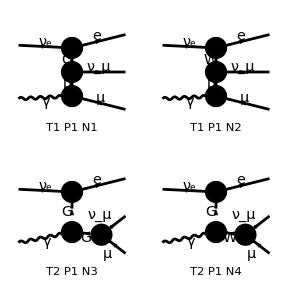

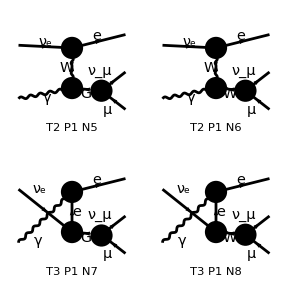

```mathematica
insertFieldseeQQbR=InsertFields[topsR,{F[1,{1}],V[1]}->{F[2,{1}],F[1,{2}],-F[2,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldseeQQbR,ColumnsXRows->{2,2}];
```

```mathematica
feynampR=CreateFeynAmp[insertFieldseeQQbR];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 4 Particles amplitudes

> Top. 3: 2 Particles amplitudes

in total: 8 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeR=CalcFeynAmp[feynampR,FermionChains->Chiral,Invariants->False,MomElim->5];
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

```mathematica
squaredAmpQQbR=PolarizationSum[AmplitudeR,GaugeTerms->True];
```

> 121 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
result=Collect[
Collect[squaredAmpQQbR//.Abbr[]//.Subexpr[]/.MomReplace/.MW2->mw2/.Replacements2to3alt/.ConjugationList/.EpsRotate/.EpsReplace/.PassarinoId2/.EpsRotate/.EpsReplace/.Replacements2to3alt/.m4sq->0/.m5sq->MM2/.m3sq->ME2,{Eps[__]},Simplify]/.Den[a_,b_]:>1/(a - b )/.Qe->-1/.Qu->2/3/.Qd->-1/3,{Pair[__]},Simplify];
```

```mathematica
resultWidthSimplification=Simplify[result*chiw45*Conjugate[chiw45](MM2-mw2+s45)^2*(MM2-mw2-s12+s23+s45)^2*chiw13*Conjugate[chiw13]/.mw->MW/.mw2->MW2];
```

```mathematica
(* Reconstruct the width dependence, zero width for this part *)
```

```mathematica
resultWidth0=Simplify[Coefficient[resultWidthSimplification,MW2,0]];
```

```mathematica
resultWidth1=Simplify[Coefficient[resultWidthSimplification,MW2,1]];
```

```mathematica
resultWidth2=Simplify[Coefficient[resultWidthSimplification,MW2,2]];
```

```mathematica
(* No averaging yet *)
```

```mathematica
Replacements2to3alt
```

{s13→m3sq-m4sq-m5sq+s12-s23-s45,s24→-m3sq+m4sq-m5sq+s12-s14-s35,s25→m3sq-m4sq+m5sq+s14-s23+s35,s34→-m3sq-m4sq-m5sq+s12-s35-s45,s15→-m3sq+m4sq+m5sq-s14+s23+s45}

```mathematica
ResultLepton=Simplify[2^3*(resultWidth0+resultWidth1*Sqrt[mw2c*Conjugate[mw2c]]+resultWidth2*mw2c*Conjugate[mw2c])]/.(ME2+MM2+s14-s23+s35)->s25
```

1/(s23^2 s25^2 sw2^2)16 Alfa Alfa2 chiw13 chiw45 π^3 chiw13^* chiw45^* (-ME2^5 MM2 (5 s23+2 s45)+ME2^4 (2 MM2^2 (12 s14-3 s23-5 s45)+8 s12^2 (s14-s45)-4 s45 (s23^2-s23 s35+s23 s45+2 s45^2-s14 (s23+2 s45))-4 s12 (s23 s35-s23 s45-4 s45^2+s14 (s23+4 s45))+MM2 (-2 s14 s23+6 s23^2-10 s23 s35+28 s14 s45+9 s23 s45-4 s35 s45-14 s45^2+4 s12 (-8 s14+s23+4 s45)))+ME2^3 (MM2^3 (40 s14+8 s23-6 s45)+MM2^2 (56 s14^2+10 s23^2+10 s23 s35-2 s12 (24 s14+5 s23-8 s45)+45 s23 s45-16 s35 s45-4 s45^2+s14 (-50 s23+48 s35+16 s45))+MM2 (7 s23^3+7 s23^2 s35-s23 s35^2+s12^2 (8 s14+5 s23-8 s45)+5 s23^2 s45+40 s23 s35 s45-2 s35^2 s45+46 s23 s45^2-28 s35 s45^2+8 s45^3+3 s14^2 (5 s23+26 s45)-s12 (80 s14^2+9 s23^2+9 s23 s35+s14 (-92 s23+64 s35-48 s45)+62 s23 s45-32 s35 s45)+s14 (-22 s23^2+6 s23 s35-74 s23 s45+60 s35 s45-52 s45^2))+4 (s12^2 (6 s14^2+s14 (-6 s23+4 s35-8 s45)+2 s45 (-2 s35+s45)+s23 (s35+6 s45))+s45 (3 s23^3+2 s45^2 (-2 s35+s45)+3 s14^2 (s23+2 s45)+s23^2 (-4 s35+5 s45)-2 s14 (3 s23^2-2 s23 s35+5 s23 s45-2 s35 s45+4 s45^2)+s23 (3 s35^2-s35 s45+7 s45^2))-s12 (4 s45^2 (-2 s35+s45)+s23^2 (-2 s35+3 s45)+3 s14^2 (s23+4 s45)+s14 (-3 s23^2+4 s23 (s35-4 s45)+8 (s35-2 s45) s45)+s23 (3 s35^2+13 s45^2))))-4 s23 (MM2^6+MM2^5 (-3 s12+2 s14-s23+5 s35+3 s45)+s35 (s14-s23+s35) s45 (-s12+s23+s45) (s12^2+s14^2+s23^2+s35^2+2 s23 s45+2 s35 s45+2 s45^2-2 s14 (s23+s45)-2 s12 (s35+s45))+MM2^4 (3 s12^2+s14^2-2 s23^2+s23 s35+8 s35^2-5 s23 s45+16 s35 s45+3 s45^2+s14 (s23+5 s35+6 s45)-s12 (6 s14-4 s23+13 s35+6 s45))+MM2^3 (-s12^3-s23^3-3 s23^2 s35+5 s23 s35^2+5 s35^3-7 s23^2 s45+23 s35^2 s45-9 s23 s45^2+19 s35 s45^2+s45^3+s14^2 (-s23+s35+3 s45)+s12^2 (6 s14-5 s23+11 s35+3 s45)+2 s14 (s23^2+2 s35^2+7 s35 s45+3 s45^2+s23 (s35+2 s45))-s12 (3 s14^2-3 s23^2+17 s35^2+28 s35 s45+3 s45^2-4 s23 (s35+3 s45)+2 s14 (7 s35+6 s45)))+MM2^2 (-s23^4+s12^3 (-2 s14+2 s23-3 s35)-2 s23^2 s35^2+4 s23 s35^3+s35^4+s14^3 (s23+s35)-4 s23^3 s45-7 s23^2 s35 s45+9 s23 s35^2 s45+12 s35^3 s45-9 s23^2 s45^2-4 s23 s35 s45^2+24 s35^2 s45^2-7 s23 s45^3+10 s35 s45^3+s12^2 (3 s14^2-3 s14 s23-8 s23 s35+11 s35^2-7 s23 s45+13 s35 s45+6 s14 (2 s35+s45))+s14^2 (-3 s23^2+s35^2+3 s45^2-2 s23 (s35+2 s45))+s14 (3 s23^3+s35^3+8 s35^2 s45+15 s35 s45^2+2 s45^3+s23^2 (s35+8 s45)+s23 (s35^2+7 s35 s45+6 s45^2))+s12 (s23^3+s23^2 (3 s35+7 s45)+s23 s45 (11 s35+12 s45)-s35 (8 s35^2+33 s35 s45+19 s45^2)-s14 (2 s23^2+8 s35^2+27 s35 s45+6 s45^2+s23 (s35+s45))+s14^2 (s23-2 (s35+3 s45))))-MM2 (s23^4 s35-s23^3 s35^2+s23^2 s35^3-s23 s35^4+s23^4 s45+3 s23^3 s35 s45+s23^2 s35^2 s45-5 s23 s35^3 s45-2 s35^4 s45+3 s23^3 s45^2+8 s23^2 s35 s45^2-6 s23 s35^2 s45^2-9 s35^3 s45^2+4 s23^2 s45^3+5 s23 s35 s45^3-11 s35^2 s45^3+2 s23 s45^4-2 s35 s45^4-s14^3 (2 s35 s45+s23 (s35+s45))+s12^3 (s14^2+s23^2-3 s23 s35+s14 (-2 s23+3 s35)+s35 (2 s35+s45))-s12^2 (s14^2 (s35+3 s45)-s14 s23 (s35+3 s45)+s14 s35 (4 s35+13 s45)+3 s35 (s35^2+4 s35 s45+s45^2)-s23 (3 s35^2+9 s35 s45+2 s45^2))+s14^2 (3 s23^2 (s35+s45)-s45 (2 s35^2-3 s35 s45+s45^2)+s23 (-s35^2+7 s35 s45+3 s45^2))-s14 (3 s23^3 (s35+s45)+2 s35 s45 (s35^2+2 s35 s45+4 s45^2)+s23^2 (-2 s35^2+8 s35 s45+6 s45^2)+s23 (s35^3-s35^2 s45+11 s35 s45^2+3 s45^3))+s12 (-s23^4+s14^3 (s23+s35)+s23^3 (s35-3 s45)-s23^2 (2 s35^2+5 s35 s45+5 s45^2)+s23 (s35^3-11 s35 s45^2-4 s45^3)+s35 (s35^3+12 s35^2 s45+20 s35 s45^2+4 s45^3)+s14^2 (-3 s23^2+s35^2+3 s45^2-s23 (s35+3 s45))+s14 (3 s23^3-s23^2 (s35-6 s45)+s23 (s35^2+5 s35 s45+2 s45^2)+s35 (s35^2+10 s35 s45+17 s45^2)))))+ME2^2 (2 MM2^4 (4 s14+5 (s23+s45))+MM2^3 (48 s14^2-6 s23^2+30 s23 s35+s14 (-38 s23+32 s35-28 s45)+27 s23 s45+4 s35 s45+34 s45^2-4 s12 (5 s23+4 s45))-2 MM2^2 (-20 s14^3+5 s23^2 s35-16 s23 s35^2+s14^2 (34 s23-32 s35-13 s45)+s12^2 (4 s14-7 s23-4 s45)+20 s23^2 s45-36 s23 s35 s45+3 s35^2 s45-8 s23 s45^2-10 s35 s45^2-20 s45^3+s14 (-11 s23^2+26 s23 s35-12 s35^2+6 s35 s45+26 s45^2)+2 s12 (16 s14^2+7 s23 s35+12 s23 s45+12 s45^2-2 s14 (7 s23-4 s35+10 s45)))+MM2 (-4 s12^3 s23-12 s23^4+15 s23^3 s35-7 s23^2 s35^2+8 s23 s35^3-20 s23^3 s45-23 s23^2 s35 s45+47 s23 s35^2 s45-52 s23^2 s45^2+66 s23 s35 s45^2-14 s35^2 s45^2-12 s23 s45^3+32 s35 s45^3+16 s45^4+16 s14^3 (s23+4 s45)+s14^2 (-44 s23^2+24 s23 s35-139 s23 s45+96 s35 s45-62 s45^2)+s12^2 (16 s14^2-6 s14 s23+3 s23^2+9 s23 s35-32 s14 s45+20 s23 s45+16 s45^2)+s14 (41 s23^3+4 s35 (8 s35-23 s45) s45+s23^2 (-43 s35+93 s45)+4 s23 (4 s35^2-23 s35 s45+26 s45^2))+s12 (-64 s14^3-3 s23^3+2 s23^2 (6 s35+29 s45)+16 s45 (s35^2-2 s35 s45-2 s45^2)+s23 (-25 s35^2-90 s35 s45+4 s45^2)+4 s14^2 (35 s23+12 (-2 s35+s45))+s14 (-79 s23^2+s23 (107 s35-116 s45)+32 (-s35^2+3 s35 s45+s45^2))))+4 (s12^2 (6 s14^3-2 s35 (s35-2 s45) s45-2 s23^2 (s35+3 s45)-2 s14^2 (6 s23-4 s35+5 s45)+s23 (2 s35^2+7 s35 s45-4 s45^2)+2 s14 (3 s23^2-3 s23 s35+s35^2+8 s23 s45-6 s35 s45+2 s45^2))+s45 (-3 s23^4+s23^3 (6 s35-7 s45)-2 s35 (s35-2 s45) s45^2+3 s14^3 (s23+2 s45)+s14^2 (-9 s23^2+5 s23 s35-17 s23 s45+8 s35 s45-10 s45^2)+s23^2 (-6 s35^2+6 s35 s45-9 s45^2)+s23 (3 s35^3+10 s35 s45^2-4 s45^3)+s14 (9 s23^3+s23^2 (-11 s35+18 s45)+2 s45 (s35^2-6 s35 s45+2 s45^2)+s23 (5 s35^2-13 s35 s45+18 s45^2)))-s12 (s23^3 (s35-3 s45)-4 s35 (s35-2 s45) s45^2+3 s14^3 (s23+4 s45)+s14^2 (-6 s23^2+s23 (5 s35-29 s45)+4 (4 s35-5 s45) s45)-2 s23^2 (2 s35^2+7 s45^2)+s23 (3 s35^3+2 s35^2 s45+17 s35 s45^2-8 s45^3)+s14 (3 s23^3+s23^2 (-6 s35+20 s45)+4 s45 (s35^2-6 s35 s45+2 s45^2)+s23 (5 s35^2-19 s35 s45+34 s45^2)))))+ME2 (MM2^5 (-8 s14-3 s23+8 s45)+MM2^4 (-8 s14^2-6 s23^2-10 s23 s35+2 s12 (8 s14+3 s23-8 s45)-21 s23 s45+16 s35 s45+24 s45^2+2 s14 (s23-8 (s35+s45)))+MM2^3 (8 s14^3+s23^3-33 s23^2 s35+s23 s35^2-29 s23^2 s45-52 s23 s35 s45+8 s35^2 s45-46 s23 s45^2+48 s35 s45^2+24 s45^3+s12^2 (-8 s14-3 s23+8 s45)-s14^2 (23 s23+40 s45)+2 s14 (14 s23^2-7 s23 s35-4 s35^2+15 s23 s45-24 s35 s45+4 s45^2)+s12 (16 s14^2+5 s23^2-16 s14 (s23-2 s35-s45)-32 s45 (s35+s45)+s23 (29 s35+42 s45)))+MM2^2 (8 s14^4-8 s23^4-8 s14^3 (3 s23-2 s35)+5 s23^3 s35-35 s23^2 s35^2+12 s23 s35^3-4 s23^3 s45-89 s23^2 s35 s45-19 s23 s35^2 s45-36 s23^2 s45^2-82 s23 s35 s45^2+24 s35^2 s45^2-44 s23 s45^3+48 s35 s45^3+8 s45^4+s12^2 (-8 s14^2+s23^2+2 s14 (5 s23-8 s35)+8 s45 (2 s35+s45)-s23 (23 s35+16 s45))+s14^2 (10 s23^2-s23 (52 s35+9 s45)+8 (s35^2-4 s35 s45-6 s45^2))+s14 (17 s23^3+s23^2 (23 s35+31 s45)-32 s45 (s35^2+s35 s45-s45^2)+s23 (-8 s35^2+28 s35 s45+44 s45^2))+s12 (-16 s14^3+7 s23^3+2 s23^2 (9 s35+17 s45)+s14^2 (34 s23+64 s45)-16 s45 (s35^2+4 s35 s45+s45^2)+s23 (15 s35^2+86 s35 s45+68 s45^2)+s14 (-35 s23^2+s23 (9 s35-68 s45)+16 (s35^2+4 s35 s45-2 s45^2))))+4 (s12^3 s23 s35 s45+s12^2 (2 s14^4+s14^3 (-6 s23+4 s35-4 s45)+2 s35^2 s45^2+s23^3 (s35+2 s45)+s23 s35 (s35^2-s35 s45-7 s45^2)-2 s23^2 (s35^2+2 s35 s45-s45^2)+s14 (-2 s23^3+2 s23^2 (s35-4 s45)+s23 (11 s35-4 s45) s45+4 s35 s45 (-s35+s45))+s14^2 (6 s23^2+s23 (-7 s35+10 s45)+2 (s35^2-4 s35 s45+s45^2)))+s45 (s23^5+4 s23^3 (s35-s45)^2+2 s35^2 s45^3+s14^4 (s23+2 s45)+s23^4 (-4 s35+3 s45)+s14^3 (-4 s23^2+2 s23 (s35-4 s45)+4 (s35-s45) s45)+s23 s35 (s35^3-s35^2 s45+s35 s45^2-6 s45^3)+s23^2 (-4 s35^3-11 s35 s45^2+2 s45^3)+s14^2 (6 s23^3+s23^2 (-8 s35+13 s45)+2 s45 (s35^2-4 s35 s45+s45^2)+s23 (2 s35^2-13 s35 s45+11 s45^2))-s14 (4 s23^4-10 s23^3 (s35-s45)+4 s35 (s35-s45) s45^2+s23^2 (6 s35^2-17 s35 s45+11 s45^2)-2 s23 (s35^3-2 s35^2 s45+8 s35 s45^2-2 s45^3)))-s12 (s23^4 s45+4 s35^2 s45^3+s14^4 (s23+4 s45)-s14^3 (3 s23-2 s35+2 s45) (s23+4 s45)+s23^3 (s35^2-s35 s45+5 s45^2)-s23^2 (2 s35^3+4 s35^2 s45+13 s35 s45^2-4 s45^3)+s23 (s35^4-12 s35 s45^3)+s14^2 (3 s23^3+s23^2 (-4 s35+17 s45)+4 s45 (s35^2-4 s35 s45+s45^2)+s23 (2 s35^2-20 s35 s45+21 s45^2))-s14 (s23^4-2 s23^3 (s35-4 s45)+8 s35 (s35-s45) s45^2+s23^2 (3 s35^2-13 s35 s45+18 s45^2)+s23 (-2 s35^3+4 s35^2 s45-27 s35 s45^2+8 s45^3))))+MM2 (4 s12^3 s23 s35+4 s14^4 (s23+4 s45)-8 s14^3 (2 s23^2-s23 s35+7 s23 s45-4 s35 s45+3 s45^2)+s14^2 (25 s23^3+s23^2 (-36 s35+66 s45)-8 s45 (-2 s35^2+8 s35 s45+s45^2)+2 s23 (4 s35^2-52 s35 s45+29 s45^2))+s14 (-17 s23^4+15 s23^3 (3 s35-2 s45)+8 s45^2 (-5 s35^2+2 s35 s45+2 s45^2)-6 s23^2 (4 s35^2-15 s35 s45+7 s45^2)+2 s23 s35 (4 s35^2-12 s35 s45+53 s45^2))+4 (s23^5+s23^4 (-4 s35+s45)+2 s35 s45^3 (3 s35+2 s45)+s23^3 (3 s35^2-5 s35 s45+2 s45^2)-s23^2 (3 s35^3+12 s35^2 s45+22 s35 s45^2+2 s45^3)+s23 (s35^4+2 s35^3 s45-4 s35^2 s45^2-16 s35 s45^3-4 s45^4))+s12^2 (8 s14^3-8 s23^3+4 s23^2 (s35-3 s45)+8 s35 s45 (s35+2 s45)-s14^2 (11 s23+24 s45)-8 s23 (s35^2+5 s35 s45+2 s45^2)+s14 (11 s23^2+s23 (5 s35+24 s45)-8 (s35^2+2 s35 s45-2 s45^2)))-2 s12 (8 s14^4-2 s14^3 (13 s23-8 s35+4 s45)-s14 (s23^3+s23^2 (-25 s35+19 s45)+s23 (10 s35^2-57 s35 s45-8 s45^2)+8 s45 (3 s35^2-2 s45^2))+s14^2 (25 s23^2+s23 (-44 s35+27 s45)+8 (s35^2-4 s35 s45-2 s45^2))-2 (3 s23^4-3 s23^3 s35-8 s35 s45^2 (s35+s45)+s23^2 (6 s35^2+19 s35 s45+2 s45^2)+s23 (-2 s35^3+5 s35^2 s45+26 s35 s45^2+8 s45^3)))))+4 mw2c (ME2^3 (2 MM2 (s14-s23-s45)+(2 s14-s23-2 s45) (3 s14-2 s23+2 s35-s45))+ME2^4 (2 s14-s23-2 s45)-ME2^2 (-6 s14^3-s12^2 s23+s12 s23^2+s23^3+s12 s23 s35-3 s23^2 s35+s23 s35^2+2 MM2^2 (s14-s45)+2 s12 s23 s45+3 s23^2 s45-8 s23 s35 s45+2 s35^2 s45+2 s23 s45^2-4 s35 s45^2+2 s14^2 (5 s23-4 s35+5 s45)+MM2 (-4 s14^2+2 s12 s23+5 s14 s23-2 s23^2+2 s23 s35+8 s14 s45-5 s23 s45-4 s45^2)-s14 (5 s23^2-9 s23 s35+2 s35^2+12 s23 s45-12 s35 s45+4 s45^2))+ME2 (2 s14^4+s14^3 (-3 s23+4 s35-4 s45)+2 MM2^3 (-s14+s23+s45)+MM2^2 (-2 s14^2-4 s12 s23+3 s14 s23+2 s23^2-4 s14 s35+2 s23 s35+3 s23 s45+4 s35 s45+2 s45^2)+s14 (2 s12^2 s23+s23^3-s23 s35 (s35-12 s45)+s23^2 (3 s35-s45)+4 s35 s45 (-s35+s45)-s12 s23 (s23+3 s35+4 s45))+s14^2 (s23 (-6 s35+5 s45)+2 (s35^2-4 s35 s45+s45^2))-(s23-s35) (s12^2 s23-s12 s23 (s23+s35+2 s45)+s35 (s23^2+3 s23 s45+2 s45^2))+2 MM2 (s14^3+s12^2 s23-2 s12 s23 (s35+s45)-s14^2 (s23+3 s45)+s14 (-2 s12 s23+s23 s35-s35^2+4 s23 s45-2 s35 s45+2 s45^2)+s35 (s23^2+2 s23 s45+s45 (s35+2 s45))))+s23 (MM2^4+MM2^3 (-2 s12+s14+2 s23+2 s35+3 s45)+s14 (s14-s23+s35) (s12^2+s14^2+s23^2+s35^2+2 s23 s45+2 s35 s45+2 s45^2-2 s14 (s23+s45)-2 s12 (s35+s45))+MM2^2 (s12^2+s23^2+3 s23 s35+s35^2+3 s23 s45+4 s35 s45+2 s45^2-s12 (4 s14+3 s23+3 s35+2 s45)+s14 (-s23+3 s35+4 s45))+MM2 (s14^3+s12^2 (2 s14+s23+s35)-s14^2 (2 s23-2 s35+s45)+s35 (s23+s45) (s23+s35+2 s45)+s14 (s23^2-3 s23 s35+3 s35^2+s23 s45+4 s35 s45+4 s45^2)-s12 (2 s14^2+(s23+s35) (s23+s35+2 s45)+s14 (-3 s23+5 s35+4 s45))))) mw2c^*-4 (ME2^4 (s14 s23-s23^2+s23 s35+MM2 (6 s14-4 s45)+4 s14 s45-2 s23 s45-4 s45^2+s12 (-4 s14+s23+4 s45))+ME2^3 (3 s14^2 s23-6 s14 s23^2+3 s23^3+4 s14 s23 s35-4 s23^2 s35+3 s23 s35^2+MM2^2 (8 s14-4 s45)+12 s14^2 s45-17 s14 s23 s45+7 s23^2 s45+8 s14 s35 s45-3 s23 s35 s45-16 s14 s45^2+12 s23 s45^2-8 s35 s45^2+4 s45^3+2 MM2 (-2 s12 s14+8 s14^2-7 s14 s23+6 s14 s35+2 s23 s35+2 s12 s45-6 s14 s45+4 s23 s45-4 s35 s45)-s12 (12 s14^2-13 s14 s23+s23^2-s23 (s35-11 s45)+8 s14 (s35-2 s45)+4 s45 (-2 s35+s45)))+ME2^2 (-s12^3 s23+3 s14^3 s23-9 s14^2 s23^2+9 s14 s23^3-3 s23^4+5 s14^2 s23 s35-11 s14 s23^2 s35+6 s23^3 s35+5 s14 s23 s35^2-6 s23^2 s35^2+3 s23 s35^3-2 MM2^3 (s14-2 s45)+12 s14^3 s45-27 s14^2 s23 s45+23 s14 s23^2 s45-8 s23^3 s45+16 s14^2 s35 s45-22 s14 s23 s35 s45+9 s23^2 s35 s45+4 s14 s35^2 s45-s23 s35^2 s45-20 s14^2 s45^2+30 s14 s23 s45^2-12 s23^2 s45^2-24 s14 s35 s45^2+18 s23 s35 s45^2-4 s35^2 s45^2+8 s14 s45^3-6 s23 s45^3+8 s35 s45^3+s12^2 s23 (s35+3 s45)+2 MM2^2 (6 s14^2-s23^2+s23 s35+2 s12 (s14-s23-s45)+4 s23 s45+6 s45^2-2 s14 (3 s23-s35+5 s45))+MM2 (14 s14^3+4 s12^2 s23+s23^3-6 s23^2 s35+7 s23 s35^2+s14^2 (-23 s23+20 s35-12 s45)-5 s23^2 s45+13 s23 s35 s45-4 s35^2 s45+4 s23 s45^2+8 s35 s45^2+8 s45^3+s12 (-8 s14^2+5 s14 s23+s23^2-3 s23 s35+16 s14 s45-11 s23 s45-8 s45^2)+s14 (8 s23^2-16 s23 s35+6 s35^2+15 s23 s45-24 s35 s45-8 s45^2))-s12 (12 s14^3+2 s23^3-4 s35 (s35-2 s45) s45-s23^2 (2 s35+7 s45)-2 s14^2 (11 s23-8 s35+10 s45)+s23 (s35^2+16 s35 s45-4 s45^2)+s14 (8 s23^2-15 s23 s35+4 s35^2+28 s23 s45-24 s35 s45+8 s45^2)))+ME2 (s14^4 s23-4 s14^3 s23^2+6 s14^2 s23^3-4 s14 s23^4+s23^5+2 s14^3 s23 s35-8 s14^2 s23^2 s35+10 s14 s23^3 s35-4 s23^4 s35+2 s14^2 s23 s35^2-6 s14 s23^2 s35^2+4 s23^3 s35^2+2 s14 s23 s35^3-4 s23^2 s35^3+s23 s35^4-s12^3 s23 (2 s14-2 s23+s35)-4 MM2^4 (s14-s45)+4 s14^4 s45-11 s14^3 s23 s45+13 s14^2 s23^2 s45-9 s14 s23^3 s45+3 s23^4 s45+8 s14^3 s35 s45-19 s14^2 s23 s35 s45+20 s14 s23^2 s35 s45-9 s23^3 s35 s45+4 s14^2 s35^2 s45-5 s14 s23 s35^2 s45+s23^2 s35^2 s45-s23 s35^3 s45-8 s14^3 s45^2+16 s14^2 s23 s45^2-12 s14 s23^2 s45^2+4 s23^3 s45^2-16 s14^2 s35 s45^2+28 s14 s23 s35 s45^2-14 s23^2 s35 s45^2-8 s14 s35^2 s45^2+4 s23 s35^2 s45^2+4 s14^2 s45^3-4 s14 s23 s45^3+2 s23^2 s45^3+8 s14 s35 s45^3-8 s23 s35 s45^3+4 s35^2 s45^3+2 MM2^3 (-2 s14^2-2 s23 s35+s14 (s23-4 s35-2 s45)+2 s12 (s14-s23-s45)+4 s35 s45+4 s45^2)+s12^2 s23 (-4 s23 s35+s35^2-5 s23 s45+2 s35 s45+3 s14 (s35+2 s45))+MM2^2 (4 s14^3+6 s12^2 s23+s23^3-8 s23^2 s35-3 s23 s35^2-3 s23^2 s45-5 s23 s35 s45+4 s35^2 s45-4 s23 s45^2+16 s35 s45^2+4 s45^3-s14^2 (7 s23+16 s45)+s14 (4 s23^2-2 s23 s35-4 s35^2+17 s23 s45-16 s35 s45+8 s45^2)+s12 (4 s14^2+7 s23^2+s14 (-9 s23+8 s35)-4 s45 (2 s35+s45)-s23 (s35+5 s45)))-s12 (4 s14^4-3 s23^4+s14^3 (-9 s23+8 s35-8 s45)+s23^3 (4 s35-2 s45)+4 s35^2 s45^2+s23 s35 (s35^2+3 s35 s45-6 s45^2)-s23^2 (6 s35^2+9 s35 s45+2 s45^2)+s14 (5 s23^3-s23 s35 (s35-26 s45)+s23^2 (s35-5 s45)+8 s35 s45 (-s35+s45))+s14^2 (3 s23^2+s23 (-13 s35+15 s45)+4 (s35^2-4 s35 s45+s45^2)))-2 MM2 (-2 s14^4+s12^3 s23+s23^4-s23^3 s35+5 s23^2 s35^2-s23 s35^3+s12^2 s23 (-3 s14+4 s23-2 s35-3 s45)+s23^3 s45+6 s23^2 s35 s45+s23 s35^2 s45+2 s23^2 s45^2+4 s23 s35 s45^2-4 s35^2 s45^2+2 s23 s45^3-4 s35 s45^3+2 s14^3 (2 s23-2 s35+s45)-s14^2 (s23^2-8 s23 s35+2 s35^2+3 s23 s45-8 s35 s45-4 s45^2)+2 s12 (s14^3+s35 s45 (s35+2 s45)-s23^2 (3 s35+2 s45)-s14^2 (s23+3 s45)+s14 (2 s23 s35-s35^2+5 s23 s45-2 s35 s45+2 s45^2))-s14 (2 s23^3+3 s23^2 s35-6 s35^2 s45+4 s45^3+s23 (-s35^2+12 s35 s45+6 s45^2))))+s23 (-MM2^4 (s12+s14-3 s23+3 s35-2 s45)+MM2^3 (2 s12^2-s14^2+3 s23^2+2 s23 s35-7 s35^2+9 s23 s45-5 s35 s45+4 s45^2+s14 (-2 s23-2 s35+s45)-s12 (s14+3 s23-3 s35+5 s45))+MM2^2 (-s12^3+s14^3+s23^3+4 s23^2 s35-4 s23 s35^2-5 s35^3+s14^2 (-s23+s35-3 s45)+6 s23^2 s45+7 s23 s35 s45-13 s35^2 s45+8 s23 s45^2-2 s35 s45^2+2 s45^3+s12^2 (4 s14-2 s23+s35+3 s45)-s14 (s23^2+5 s23 s35+s35^2+3 s23 s45+2 s35 s45-6 s45^2)+s12 (-6 s23^2+4 s23 s35+7 s35^2+s14 (6 s23+s35-8 s45)-7 s23 s45-4 s45^2))-MM2 (-s14^4-s23^4-2 s23^2 s35^2+4 s23 s35^3+s35^4+s12^3 (2 s14-2 s23+s35)-3 s23^3 s45-5 s23^2 s35 s45+3 s23 s35^2 s45+7 s35^3 s45-4 s23^2 s45^2-6 s23 s35 s45^2+8 s35^2 s45^2-2 s23 s45^3+s14^3 (4 s23+s45)-s14^2 (6 s23^2+5 s23 s45+3 s35 s45)+s12^2 (-2 s14^2+6 s14 s23-4 s23^2+s35 (s35-2 s45)+s23 (6 s35+s45)-3 s14 (s35+2 s45))+s14 (4 s23^3+7 s23^2 s45+2 s23 (s35^2+4 s35 s45+2 s45^2)-s45 (s35^2+4 s45^2))+s12 (s14^3+s23^3+6 s23^2 (s35+s45)+s14^2 (-s23+3 s35+s45)+s35 (-3 s35^2-7 s35 s45+2 s45^2)+s23 (-8 s35^2+s35 s45+2 s45^2)+s14 (-s23^2-9 s23 s35+s35^2-7 s23 s45+2 s35 s45+8 s45^2)))-(s14-s23+s35) (s12^3 (s14-s23)-s14^3 s45+s14^2 (s23+s45) (s35+2 s45)+s12^2 (-2 s14 s35+3 s23 s35-3 s14 s45+2 s23 s45+s35 s45)+s35 (s23+s45) (s23^2+s35^2+2 s23 s45+2 s35 s45+2 s45^2)-s14 (s23^2 (2 s35+s45)+2 s23 s45 (2 s35+s45)+s45 (s35^2+4 s35 s45+2 s45^2))+s12 (s14^3-s23^3-2 s23^2 s45-2 s35 s45 (s35+s45)-s14^2 (3 s23+2 s45)-s23 (3 s35^2+4 s35 s45+2 s45^2)+s14 (3 s23^2+4 s23 s45+(s35+2 s45)^2))))) √(mw2c mw2c^*))

```mathematica
prefac
```

4 Alfa Alfa2 chiw13 chiw45 π^3 chiw13^* chiw45^*

```mathematica
CForm[prefac/.Alfa->ALPHA/.Alfa2->ALPHA*Conjugate[ALPHA]]/.Power->pow/.Conjugate->conj/.Pi->pi
```

CForm(4*chiw13*chiw45*conj(ALPHA)*conj(chiw13)*conj(chiw45)*pow(ALPHA,2)*pow(pi,3))

```mathematica
(* Implement this thing *)
```

```mathematica
CForm[Simplify[ResultLepton/prefac]/.mw2->mw2c/.ME2->ml1sq/.MM2->ml2sq/.sw2->sw2c/.sw->Sqrt[sw2]]/.Power->pow/.Conjugate->conj/.sw2c->SW2
```

4*pow(s23,-2)*pow(s25,-2)*pow(SW2,-2)*(-(ml2sq*(5*s23 + 2*s45)*pow(ml1sq,5)) + 
     pow(ml1sq,4)*(2*(12*s14 - 3*s23 - 5*s45)*pow(ml2sq,2) + 8*(s14 - s45)*pow(s12,2) + 
        ml2sq*(-2*s14*s23 - 10*s23*s35 + 28*s14*s45 + 9*s23*s45 - 4*s35*s45 + 
           4*s12*(-8*s14 + s23 + 4*s45) + 6*pow(s23,2) - 14*pow(s45,2)) - 
        4*s12*(s23*s35 - s23*s45 + s14*(s23 + 4*s45) - 4*pow(s45,2)) - 
        4*s45*(-(s23*s35) + s23*s45 - s14*(s23 + 2*s45) + pow(s23,2) + 2*pow(s45,2))) + 
     4*mw2c*conj(mw2c)*((2*ml2sq*(s14 - s23 - s45) + 
           (2*s14 - s23 - 2*s45)*(3*s14 - 2*s23 + 2*s35 - s45))*pow(ml1sq,3) + 
        (2*s14 - s23 - 2*s45)*pow(ml1sq,4) - 
        pow(ml1sq,2)*(s12*s23*s35 + 2*s12*s23*s45 - 8*s23*s35*s45 + 2*(s14 - s45)*pow(ml2sq,2) - 
           s23*pow(s12,2) + 2*(5*s23 - 4*s35 + 5*s45)*pow(s14,2) - 6*pow(s14,3) + s12*pow(s23,2) - 
           3*s35*pow(s23,2) + 3*s45*pow(s23,2) + pow(s23,3) + s23*pow(s35,2) + 2*s45*pow(s35,2) + 
           ml2sq*(2*s12*s23 + 5*s14*s23 + 2*s23*s35 + 8*s14*s45 - 5*s23*s45 - 4*pow(s14,2) - 
              2*pow(s23,2) - 4*pow(s45,2)) + 2*s23*pow(s45,2) - 4*s35*pow(s45,2) - 
           s14*(-9*s23*s35 + 12*s23*s45 - 12*s35*s45 + 5*pow(s23,2) + 2*pow(s35,2) + 4*pow(s45,2))) + 
        ml1sq*(2*(-s14 + s23 + s45)*pow(ml2sq,3) + (-3*s23 + 4*s35 - 4*s45)*pow(s14,3) + 
           2*pow(s14,4) + s14*(-(s23*s35*(s35 - 12*s45)) + 4*s35*s45*(-s35 + s45) - 
              s12*s23*(s23 + 3*s35 + 4*s45) + 2*s23*pow(s12,2) + (3*s35 - s45)*pow(s23,2) + pow(s23,3))
             + pow(ml2sq,2)*(-4*s12*s23 + 3*s14*s23 - 4*s14*s35 + 2*s23*s35 + 3*s23*s45 + 4*s35*s45 - 
              2*pow(s14,2) + 2*pow(s23,2) + 2*pow(s45,2)) + 
           pow(s14,2)*(s23*(-6*s35 + 5*s45) + 2*(-4*s35*s45 + pow(s35,2) + pow(s45,2))) - 
           (s23 - s35)*(-(s12*s23*(s23 + s35 + 2*s45)) + s23*pow(s12,2) + 
              s35*(3*s23*s45 + pow(s23,2) + 2*pow(s45,2))) + 
           2*ml2sq*(-2*s12*s23*(s35 + s45) + s23*pow(s12,2) - (s23 + 3*s45)*pow(s14,2) + pow(s14,3) + 
              s35*(2*s23*s45 + s45*(s35 + 2*s45) + pow(s23,2)) + 
              s14*(-2*s12*s23 + s23*s35 + 4*s23*s45 - 2*s35*s45 - pow(s35,2) + 2*pow(s45,2)))) + 
        s23*((-2*s12 + s14 + 2*s23 + 2*s35 + 3*s45)*pow(ml2sq,3) + pow(ml2sq,4) + 
           pow(ml2sq,2)*(3*s23*s35 + 3*s23*s45 + 4*s35*s45 - s12*(4*s14 + 3*s23 + 3*s35 + 2*s45) + 
              s14*(-s23 + 3*s35 + 4*s45) + pow(s12,2) + pow(s23,2) + pow(s35,2) + 2*pow(s45,2)) + 
           s14*(s14 - s23 + s35)*(2*s23*s45 + 2*s35*s45 - 2*s14*(s23 + s45) - 2*s12*(s35 + s45) + 
              pow(s12,2) + pow(s14,2) + pow(s23,2) + pow(s35,2) + 2*pow(s45,2)) + 
           ml2sq*(s35*(s23 + s45)*(s23 + s35 + 2*s45) + (2*s14 + s23 + s35)*pow(s12,2) - 
              (2*s23 - 2*s35 + s45)*pow(s14,2) - 
              s12*((s23 + s35)*(s23 + s35 + 2*s45) + s14*(-3*s23 + 5*s35 + 4*s45) + 2*pow(s14,2)) + 
              pow(s14,3) + s14*(-3*s23*s35 + s23*s45 + 4*s35*s45 + pow(s23,2) + 3*pow(s35,2) + 
                 4*pow(s45,2))))) + pow(ml1sq,3)*
      ((40*s14 + 8*s23 - 6*s45)*pow(ml2sq,3) + 
        pow(ml2sq,2)*(10*s23*s35 - 2*s12*(24*s14 + 5*s23 - 8*s45) + 45*s23*s45 - 16*s35*s45 + 
           s14*(-50*s23 + 48*s35 + 16*s45) + 56*pow(s14,2) + 10*pow(s23,2) - 4*pow(s45,2)) + 
        4*(pow(s12,2)*(s14*(-6*s23 + 4*s35 - 8*s45) + 2*s45*(-2*s35 + s45) + s23*(s35 + 6*s45) + 
              6*pow(s14,2)) + s45*(3*(s23 + 2*s45)*pow(s14,2) + (-4*s35 + 5*s45)*pow(s23,2) + 
              3*pow(s23,3) + 2*(-2*s35 + s45)*pow(s45,2) - 
              2*s14*(-2*s23*s35 + 5*s23*s45 - 2*s35*s45 + 3*pow(s23,2) + 4*pow(s45,2)) + 
              s23*(-(s35*s45) + 3*pow(s35,2) + 7*pow(s45,2))) - 
           s12*(3*(s23 + 4*s45)*pow(s14,2) + 
              s14*(4*s23*(s35 - 4*s45) + 8*(s35 - 2*s45)*s45 - 3*pow(s23,2)) + 
              (-2*s35 + 3*s45)*pow(s23,2) + 4*(-2*s35 + s45)*pow(s45,2) + 
              s23*(3*pow(s35,2) + 13*pow(s45,2)))) + 
        ml2sq*(40*s23*s35*s45 + (8*s14 + 5*s23 - 8*s45)*pow(s12,2) + 3*(5*s23 + 26*s45)*pow(s14,2) + 
           7*s35*pow(s23,2) + 5*s45*pow(s23,2) - 
           s12*(9*s23*s35 + s14*(-92*s23 + 64*s35 - 48*s45) + 62*s23*s45 - 32*s35*s45 + 
              80*pow(s14,2) + 9*pow(s23,2)) + 7*pow(s23,3) - s23*pow(s35,2) - 2*s45*pow(s35,2) + 
           s14*(6*s23*s35 - 74*s23*s45 + 60*s35*s45 - 22*pow(s23,2) - 52*pow(s45,2)) + 
           46*s23*pow(s45,2) - 28*s35*pow(s45,2) + 8*pow(s45,3))) + 
     ml1sq*((-8*s14 - 3*s23 + 8*s45)*pow(ml2sq,5) + 
        pow(ml2sq,4)*(-10*s23*s35 + 2*s12*(8*s14 + 3*s23 - 8*s45) - 21*s23*s45 + 16*s35*s45 + 
           2*s14*(s23 - 8*(s35 + s45)) - 8*pow(s14,2) - 6*pow(s23,2) + 24*pow(s45,2)) + 
        pow(ml2sq,3)*(-52*s23*s35*s45 + (-8*s14 - 3*s23 + 8*s45)*pow(s12,2) - 
           (23*s23 + 40*s45)*pow(s14,2) + 8*pow(s14,3) - 33*s35*pow(s23,2) - 29*s45*pow(s23,2) + 
           s12*(-16*s14*(s23 - 2*s35 - s45) - 32*s45*(s35 + s45) + s23*(29*s35 + 42*s45) + 
              16*pow(s14,2) + 5*pow(s23,2)) + pow(s23,3) + s23*pow(s35,2) + 8*s45*pow(s35,2) - 
           46*s23*pow(s45,2) + 48*s35*pow(s45,2) + 
           2*s14*(-7*s23*s35 + 15*s23*s45 - 24*s35*s45 + 14*pow(s23,2) - 4*pow(s35,2) + 
              4*pow(s45,2)) + 24*pow(s45,3)) + 
        4*(s23*s35*s45*pow(s12,3) + pow(s12,2)*
            ((-6*s23 + 4*s35 - 4*s45)*pow(s14,3) + 2*pow(s14,4) + 
              s14*(s23*(11*s35 - 4*s45)*s45 + 4*s35*s45*(-s35 + s45) + 2*(s35 - 4*s45)*pow(s23,2) - 
                 2*pow(s23,3)) + (s35 + 2*s45)*pow(s23,3) + 
              s23*s35*(-(s35*s45) + pow(s35,2) - 7*pow(s45,2)) - 
              2*pow(s23,2)*(2*s35*s45 + pow(s35,2) - pow(s45,2)) + 2*pow(s35,2)*pow(s45,2) + 
              pow(s14,2)*(s23*(-7*s35 + 10*s45) + 6*pow(s23,2) + 
                 2*(-4*s35*s45 + pow(s35,2) + pow(s45,2)))) + 
           s45*((s23 + 2*s45)*pow(s14,4) + 
              pow(s14,3)*(2*s23*(s35 - 4*s45) + 4*(s35 - s45)*s45 - 4*pow(s23,2)) + 
              (-4*s35 + 3*s45)*pow(s23,4) + pow(s23,5) + 4*pow(s23,3)*pow(s35 - s45,2) + 
              pow(s14,2)*((-8*s35 + 13*s45)*pow(s23,2) + 6*pow(s23,3) + 
                 2*s45*(-4*s35*s45 + pow(s35,2) + pow(s45,2)) + 
                 s23*(-13*s35*s45 + 2*pow(s35,2) + 11*pow(s45,2))) - 
              s14*(-10*(s35 - s45)*pow(s23,3) + 4*pow(s23,4) + 4*s35*(s35 - s45)*pow(s45,2) + 
                 pow(s23,2)*(-17*s35*s45 + 6*pow(s35,2) + 11*pow(s45,2)) - 
                 2*s23*(-2*s45*pow(s35,2) + pow(s35,3) + 8*s35*pow(s45,2) - 2*pow(s45,3))) + 
              s23*s35*(-(s45*pow(s35,2)) + pow(s35,3) + s35*pow(s45,2) - 6*pow(s45,3)) + 
              2*pow(s35,2)*pow(s45,3) + pow(s23,2)*(-4*pow(s35,3) - 11*s35*pow(s45,2) + 2*pow(s45,3)))\
            - s12*(-((3*s23 - 2*s35 + 2*s45)*(s23 + 4*s45)*pow(s14,3)) + (s23 + 4*s45)*pow(s14,4) + 
              s45*pow(s23,4) + pow(s23,3)*(-(s35*s45) + pow(s35,2) + 5*pow(s45,2)) + 
              pow(s14,2)*((-4*s35 + 17*s45)*pow(s23,2) + 3*pow(s23,3) + 
                 4*s45*(-4*s35*s45 + pow(s35,2) + pow(s45,2)) + 
                 s23*(-20*s35*s45 + 2*pow(s35,2) + 21*pow(s45,2))) - 
              pow(s23,2)*(4*s45*pow(s35,2) + 2*pow(s35,3) + 13*s35*pow(s45,2) - 4*pow(s45,3)) + 
              4*pow(s35,2)*pow(s45,3) + s23*(pow(s35,4) - 12*s35*pow(s45,3)) - 
              s14*(-2*(s35 - 4*s45)*pow(s23,3) + pow(s23,4) + 8*s35*(s35 - s45)*pow(s45,2) + 
                 pow(s23,2)*(-13*s35*s45 + 3*pow(s35,2) + 18*pow(s45,2)) + 
                 s23*(4*s45*pow(s35,2) - 2*pow(s35,3) - 27*s35*pow(s45,2) + 8*pow(s45,3))))) + 
        ml2sq*(4*s23*s35*pow(s12,3) + 4*(s23 + 4*s45)*pow(s14,4) - 
           8*pow(s14,3)*(-(s23*s35) + 7*s23*s45 - 4*s35*s45 + 2*pow(s23,2) + 3*pow(s45,2)) + 
           pow(s12,2)*(8*s35*s45*(s35 + 2*s45) - (11*s23 + 24*s45)*pow(s14,2) + 8*pow(s14,3) + 
              4*(s35 - 3*s45)*pow(s23,2) - 8*pow(s23,3) + 
              s14*(s23*(5*s35 + 24*s45) + 11*pow(s23,2) - 8*(2*s35*s45 + pow(s35,2) - 2*pow(s45,2))) - 
              8*s23*(5*s35*s45 + pow(s35,2) + 2*pow(s45,2))) + 
           pow(s14,2)*((-36*s35 + 66*s45)*pow(s23,2) + 25*pow(s23,3) - 
              8*s45*(8*s35*s45 - 2*pow(s35,2) + pow(s45,2)) + 
              2*s23*(-52*s35*s45 + 4*pow(s35,2) + 29*pow(s45,2))) + 
           s14*(15*(3*s35 - 2*s45)*pow(s23,3) - 17*pow(s23,4) + 
              8*pow(s45,2)*(2*s35*s45 - 5*pow(s35,2) + 2*pow(s45,2)) - 
              6*pow(s23,2)*(-15*s35*s45 + 4*pow(s35,2) + 7*pow(s45,2)) + 
              2*s23*s35*(-12*s35*s45 + 4*pow(s35,2) + 53*pow(s45,2))) - 
           2*s12*(-2*(13*s23 - 8*s35 + 4*s45)*pow(s14,3) + 8*pow(s14,4) + 
              pow(s14,2)*(s23*(-44*s35 + 27*s45) + 25*pow(s23,2) + 
                 8*(-4*s35*s45 + pow(s35,2) - 2*pow(s45,2))) - 
              s14*((-25*s35 + 19*s45)*pow(s23,2) + pow(s23,3) + 
                 s23*(-57*s35*s45 + 10*pow(s35,2) - 8*pow(s45,2)) + 8*s45*(3*pow(s35,2) - 2*pow(s45,2))
                 ) - 2*(-3*s35*pow(s23,3) + 3*pow(s23,4) - 8*s35*(s35 + s45)*pow(s45,2) + 
                 pow(s23,2)*(19*s35*s45 + 6*pow(s35,2) + 2*pow(s45,2)) + 
                 s23*(5*s45*pow(s35,2) - 2*pow(s35,3) + 26*s35*pow(s45,2) + 8*pow(s45,3)))) + 
           4*((-4*s35 + s45)*pow(s23,4) + pow(s23,5) + 
              pow(s23,3)*(-5*s35*s45 + 3*pow(s35,2) + 2*pow(s45,2)) + 
              2*s35*(3*s35 + 2*s45)*pow(s45,3) - 
              pow(s23,2)*(12*s45*pow(s35,2) + 3*pow(s35,3) + 22*s35*pow(s45,2) + 2*pow(s45,3)) + 
              s23*(2*s45*pow(s35,3) + pow(s35,4) - 4*pow(s35,2)*pow(s45,2) - 16*s35*pow(s45,3) - 
                 4*pow(s45,4)))) + pow(ml2sq,2)*
         (-8*(3*s23 - 2*s35)*pow(s14,3) + 8*pow(s14,4) - 89*s35*s45*pow(s23,2) + 
           pow(s12,2)*(2*s14*(5*s23 - 8*s35) + 8*s45*(2*s35 + s45) - s23*(23*s35 + 16*s45) - 
              8*pow(s14,2) + pow(s23,2)) + 5*s35*pow(s23,3) - 4*s45*pow(s23,3) - 8*pow(s23,4) - 
           19*s23*s45*pow(s35,2) - 35*pow(s23,2)*pow(s35,2) + 12*s23*pow(s35,3) + 
           pow(s14,2)*(-(s23*(52*s35 + 9*s45)) + 10*pow(s23,2) + 
              8*(-4*s35*s45 + pow(s35,2) - 6*pow(s45,2))) - 82*s23*s35*pow(s45,2) - 
           36*pow(s23,2)*pow(s45,2) + 24*pow(s35,2)*pow(s45,2) + 
           s14*((23*s35 + 31*s45)*pow(s23,2) + 17*pow(s23,3) - 
              32*s45*(s35*s45 + pow(s35,2) - pow(s45,2)) + 
              s23*(28*s35*s45 - 8*pow(s35,2) + 44*pow(s45,2))) + 
           s12*((34*s23 + 64*s45)*pow(s14,2) - 16*pow(s14,3) + 2*(9*s35 + 17*s45)*pow(s23,2) + 
              7*pow(s23,3) + s14*(s23*(9*s35 - 68*s45) - 35*pow(s23,2) + 
                 16*(4*s35*s45 + pow(s35,2) - 2*pow(s45,2))) - 
              16*s45*(4*s35*s45 + pow(s35,2) + pow(s45,2)) + 
              s23*(86*s35*s45 + 15*pow(s35,2) + 68*pow(s45,2))) - 44*s23*pow(s45,3) + 
           48*s35*pow(s45,3) + 8*pow(s45,4))) + 
     pow(ml1sq,2)*(2*(4*s14 + 5*(s23 + s45))*pow(ml2sq,4) + 
        pow(ml2sq,3)*(30*s23*s35 + s14*(-38*s23 + 32*s35 - 28*s45) + 27*s23*s45 + 4*s35*s45 - 
           4*s12*(5*s23 + 4*s45) + 48*pow(s14,2) - 6*pow(s23,2) + 34*pow(s45,2)) + 
        4*(pow(s12,2)*(-2*s35*(s35 - 2*s45)*s45 - 2*(6*s23 - 4*s35 + 5*s45)*pow(s14,2) + 
              6*pow(s14,3) - 2*(s35 + 3*s45)*pow(s23,2) + 
              s23*(7*s35*s45 + 2*pow(s35,2) - 4*pow(s45,2)) + 
              2*s14*(-3*s23*s35 + 8*s23*s45 - 6*s35*s45 + 3*pow(s23,2) + pow(s35,2) + 2*pow(s45,2))) - 
           s12*(3*(s23 + 4*s45)*pow(s14,3) + 
              pow(s14,2)*(s23*(5*s35 - 29*s45) + 4*(4*s35 - 5*s45)*s45 - 6*pow(s23,2)) + 
              (s35 - 3*s45)*pow(s23,3) - 4*s35*(s35 - 2*s45)*pow(s45,2) - 
              2*pow(s23,2)*(2*pow(s35,2) + 7*pow(s45,2)) + 
              s14*((-6*s35 + 20*s45)*pow(s23,2) + 3*pow(s23,3) + 
                 4*s45*(-6*s35*s45 + pow(s35,2) + 2*pow(s45,2)) + 
                 s23*(-19*s35*s45 + 5*pow(s35,2) + 34*pow(s45,2))) + 
              s23*(2*s45*pow(s35,2) + 3*pow(s35,3) + 17*s35*pow(s45,2) - 8*pow(s45,3))) + 
           s45*(3*(s23 + 2*s45)*pow(s14,3) + (6*s35 - 7*s45)*pow(s23,3) - 3*pow(s23,4) + 
              pow(s14,2)*(5*s23*s35 - 17*s23*s45 + 8*s35*s45 - 9*pow(s23,2) - 10*pow(s45,2)) + 
              pow(s23,2)*(6*s35*s45 - 6*pow(s35,2) - 9*pow(s45,2)) - 2*s35*(s35 - 2*s45)*pow(s45,2) + 
              s14*((-11*s35 + 18*s45)*pow(s23,2) + 9*pow(s23,3) + 
                 2*s45*(-6*s35*s45 + pow(s35,2) + 2*pow(s45,2)) + 
                 s23*(-13*s35*s45 + 5*pow(s35,2) + 18*pow(s45,2))) + 
              s23*(3*pow(s35,3) + 10*s35*pow(s45,2) - 4*pow(s45,3)))) - 
        2*pow(ml2sq,2)*(-36*s23*s35*s45 + (4*s14 - 7*s23 - 4*s45)*pow(s12,2) + 
           (34*s23 - 32*s35 - 13*s45)*pow(s14,2) - 20*pow(s14,3) + 5*s35*pow(s23,2) + 
           20*s45*pow(s23,2) - 16*s23*pow(s35,2) + 3*s45*pow(s35,2) - 8*s23*pow(s45,2) - 
           10*s35*pow(s45,2) + 2*s12*(7*s23*s35 + 12*s23*s45 - 2*s14*(7*s23 - 4*s35 + 10*s45) + 
              16*pow(s14,2) + 12*pow(s45,2)) + 
           s14*(26*s23*s35 + 6*s35*s45 - 11*pow(s23,2) - 12*pow(s35,2) + 26*pow(s45,2)) - 20*pow(s45,3)
           ) + ml2sq*(-4*s23*pow(s12,3) + 16*(s23 + 4*s45)*pow(s14,3) - 23*s35*s45*pow(s23,2) + 
           15*s35*pow(s23,3) - 20*s45*pow(s23,3) - 12*pow(s23,4) + 47*s23*s45*pow(s35,2) - 
           7*pow(s23,2)*pow(s35,2) + 8*s23*pow(s35,3) + 
           pow(s14,2)*(24*s23*s35 - 139*s23*s45 + 96*s35*s45 - 44*pow(s23,2) - 62*pow(s45,2)) + 
           66*s23*s35*pow(s45,2) - 52*pow(s23,2)*pow(s45,2) - 14*pow(s35,2)*pow(s45,2) + 
           pow(s12,2)*(-6*s14*s23 + 9*s23*s35 - 32*s14*s45 + 20*s23*s45 + 16*pow(s14,2) + 
              3*pow(s23,2) + 16*pow(s45,2)) + 
           s14*(4*s35*(8*s35 - 23*s45)*s45 + (-43*s35 + 93*s45)*pow(s23,2) + 41*pow(s23,3) + 
              4*s23*(-23*s35*s45 + 4*pow(s35,2) + 26*pow(s45,2))) + 
           s12*(4*(35*s23 + 12*(-2*s35 + s45))*pow(s14,2) - 64*pow(s14,3) + 
              2*(6*s35 + 29*s45)*pow(s23,2) - 3*pow(s23,3) + 
              16*s45*(-2*s35*s45 + pow(s35,2) - 2*pow(s45,2)) + 
              s23*(-90*s35*s45 - 25*pow(s35,2) + 4*pow(s45,2)) + 
              s14*(s23*(107*s35 - 116*s45) - 79*pow(s23,2) + 32*(3*s35*s45 - pow(s35,2) + pow(s45,2))))
             - 12*s23*pow(s45,3) + 32*s35*pow(s45,3) + 16*pow(s45,4))) - 
     4*s23*((-3*s12 + 2*s14 - s23 + 5*s35 + 3*s45)*pow(ml2sq,5) + pow(ml2sq,6) + 
        s35*(s14 - s23 + s35)*s45*(-s12 + s23 + s45)*
         (2*s23*s45 + 2*s35*s45 - 2*s14*(s23 + s45) - 2*s12*(s35 + s45) + pow(s12,2) + pow(s14,2) + 
           pow(s23,2) + pow(s35,2) + 2*pow(s45,2)) + 
        pow(ml2sq,4)*(s23*s35 - 5*s23*s45 + 16*s35*s45 + s14*(s23 + 5*s35 + 6*s45) - 
           s12*(6*s14 - 4*s23 + 13*s35 + 6*s45) + 3*pow(s12,2) + pow(s14,2) - 2*pow(s23,2) + 
           8*pow(s35,2) + 3*pow(s45,2)) + 
        pow(ml2sq,3)*((6*s14 - 5*s23 + 11*s35 + 3*s45)*pow(s12,2) - pow(s12,3) + 
           (-s23 + s35 + 3*s45)*pow(s14,2) - 3*s35*pow(s23,2) - 7*s45*pow(s23,2) - pow(s23,3) + 
           5*s23*pow(s35,2) + 23*s45*pow(s35,2) + 5*pow(s35,3) - 9*s23*pow(s45,2) + 
           19*s35*pow(s45,2) + 2*s14*(7*s35*s45 + s23*(s35 + 2*s45) + pow(s23,2) + 2*pow(s35,2) + 
              3*pow(s45,2)) - s12*(28*s35*s45 - 4*s23*(s35 + 3*s45) + 2*s14*(7*s35 + 6*s45) + 
              3*pow(s14,2) - 3*pow(s23,2) + 17*pow(s35,2) + 3*pow(s45,2)) + pow(s45,3)) + 
        pow(ml2sq,2)*((-2*s14 + 2*s23 - 3*s35)*pow(s12,3) + (s23 + s35)*pow(s14,3) - 
           7*s35*s45*pow(s23,2) - 4*s45*pow(s23,3) - pow(s23,4) + 9*s23*s45*pow(s35,2) - 
           2*pow(s23,2)*pow(s35,2) + pow(s12,2)*
            (-3*s14*s23 - 8*s23*s35 - 7*s23*s45 + 13*s35*s45 + 6*s14*(2*s35 + s45) + 3*pow(s14,2) + 
              11*pow(s35,2)) + 4*s23*pow(s35,3) + 12*s45*pow(s35,3) + pow(s35,4) - 
           4*s23*s35*pow(s45,2) - 9*pow(s23,2)*pow(s45,2) + 24*pow(s35,2)*pow(s45,2) + 
           pow(s14,2)*(-2*s23*(s35 + 2*s45) - 3*pow(s23,2) + pow(s35,2) + 3*pow(s45,2)) + 
           s12*(s23*s45*(11*s35 + 12*s45) + (s23 - 2*(s35 + 3*s45))*pow(s14,2) + 
              (3*s35 + 7*s45)*pow(s23,2) + pow(s23,3) - 
              s14*(27*s35*s45 + s23*(s35 + s45) + 2*pow(s23,2) + 8*pow(s35,2) + 6*pow(s45,2)) - 
              s35*(33*s35*s45 + 8*pow(s35,2) + 19*pow(s45,2))) - 7*s23*pow(s45,3) + 
           10*s35*pow(s45,3) + s14*((s35 + 8*s45)*pow(s23,2) + 3*pow(s23,3) + 8*s45*pow(s35,2) + 
              pow(s35,3) + 15*s35*pow(s45,2) + s23*(7*s35*s45 + pow(s35,2) + 6*pow(s45,2)) + 
              2*pow(s45,3))) - ml2sq*(-((2*s35*s45 + s23*(s35 + s45))*pow(s14,3)) + 
           pow(s12,3)*(-3*s23*s35 + s14*(-2*s23 + 3*s35) + s35*(2*s35 + s45) + pow(s14,2) + 
              pow(s23,2)) + 3*s35*s45*pow(s23,3) + s35*pow(s23,4) + s45*pow(s23,4) + 
           s45*pow(s23,2)*pow(s35,2) - pow(s23,3)*pow(s35,2) - 5*s23*s45*pow(s35,3) + 
           pow(s23,2)*pow(s35,3) - s23*pow(s35,4) - 2*s45*pow(s35,4) + 8*s35*pow(s23,2)*pow(s45,2) + 
           3*pow(s23,3)*pow(s45,2) - 6*s23*pow(s35,2)*pow(s45,2) - 9*pow(s35,3)*pow(s45,2) - 
           pow(s12,2)*(-(s14*s23*(s35 + 3*s45)) + s14*s35*(4*s35 + 13*s45) + 
              (s35 + 3*s45)*pow(s14,2) + 3*s35*(4*s35*s45 + pow(s35,2) + pow(s45,2)) - 
              s23*(9*s35*s45 + 3*pow(s35,2) + 2*pow(s45,2))) + 
           pow(s14,2)*(3*(s35 + s45)*pow(s23,2) - s45*(-3*s35*s45 + 2*pow(s35,2) + pow(s45,2)) + 
              s23*(7*s35*s45 - pow(s35,2) + 3*pow(s45,2))) + 5*s23*s35*pow(s45,3) + 
           4*pow(s23,2)*pow(s45,3) - 11*pow(s35,2)*pow(s45,3) - 
           s14*(3*(s35 + s45)*pow(s23,3) + 2*s35*s45*(2*s35*s45 + pow(s35,2) + 4*pow(s45,2)) + 
              pow(s23,2)*(8*s35*s45 - 2*pow(s35,2) + 6*pow(s45,2)) + 
              s23*(-(s45*pow(s35,2)) + pow(s35,3) + 11*s35*pow(s45,2) + 3*pow(s45,3))) + 
           s12*((s23 + s35)*pow(s14,3) + (s35 - 3*s45)*pow(s23,3) - pow(s23,4) + 
              pow(s14,2)*(-(s23*(s35 + 3*s45)) - 3*pow(s23,2) + pow(s35,2) + 3*pow(s45,2)) - 
              pow(s23,2)*(5*s35*s45 + 2*pow(s35,2) + 5*pow(s45,2)) + 
              s14*(-((s35 - 6*s45)*pow(s23,2)) + 3*pow(s23,3) + 
                 s23*(5*s35*s45 + pow(s35,2) + 2*pow(s45,2)) + 
                 s35*(10*s35*s45 + pow(s35,2) + 17*pow(s45,2))) + 
              s23*(pow(s35,3) - 11*s35*pow(s45,2) - 4*pow(s45,3)) + 
              s35*(12*s45*pow(s35,2) + pow(s35,3) + 20*s35*pow(s45,2) + 4*pow(s45,3))) + 
           2*s23*pow(s45,4) - 2*s35*pow(s45,4))) - 
     4*(pow(ml1sq,4)*(s14*s23 + s23*s35 + ml2sq*(6*s14 - 4*s45) + 4*s14*s45 - 2*s23*s45 + 
           s12*(-4*s14 + s23 + 4*s45) - pow(s23,2) - 4*pow(s45,2)) + 
        pow(ml1sq,3)*(4*s14*s23*s35 - 17*s14*s23*s45 + 8*s14*s35*s45 - 3*s23*s35*s45 + 
           (8*s14 - 4*s45)*pow(ml2sq,2) + 3*s23*pow(s14,2) + 12*s45*pow(s14,2) + 
           2*ml2sq*(-2*s12*s14 - 7*s14*s23 + 6*s14*s35 + 2*s23*s35 + 2*s12*s45 - 6*s14*s45 + 
              4*s23*s45 - 4*s35*s45 + 8*pow(s14,2)) - 6*s14*pow(s23,2) - 4*s35*pow(s23,2) + 
           7*s45*pow(s23,2) - s12*(-13*s14*s23 - s23*(s35 - 11*s45) + 8*s14*(s35 - 2*s45) + 
              4*s45*(-2*s35 + s45) + 12*pow(s14,2) + pow(s23,2)) + 3*pow(s23,3) + 3*s23*pow(s35,2) - 
           16*s14*pow(s45,2) + 12*s23*pow(s45,2) - 8*s35*pow(s45,2) + 4*pow(s45,3)) + 
        pow(ml1sq,2)*(-22*s14*s23*s35*s45 - 2*(s14 - 2*s45)*pow(ml2sq,3) + 
           s23*(s35 + 3*s45)*pow(s12,2) - s23*pow(s12,3) + 5*s23*s35*pow(s14,2) - 
           27*s23*s45*pow(s14,2) + 16*s35*s45*pow(s14,2) + 3*s23*pow(s14,3) + 12*s45*pow(s14,3) - 
           11*s14*s35*pow(s23,2) + 23*s14*s45*pow(s23,2) + 9*s35*s45*pow(s23,2) - 
           9*pow(s14,2)*pow(s23,2) + 9*s14*pow(s23,3) + 6*s35*pow(s23,3) - 8*s45*pow(s23,3) - 
           3*pow(s23,4) + 5*s14*s23*pow(s35,2) + 4*s14*s45*pow(s35,2) - s23*s45*pow(s35,2) - 
           6*pow(s23,2)*pow(s35,2) + 3*s23*pow(s35,3) + 30*s14*s23*pow(s45,2) - 
           24*s14*s35*pow(s45,2) + 18*s23*s35*pow(s45,2) - 20*pow(s14,2)*pow(s45,2) - 
           12*pow(s23,2)*pow(s45,2) - 4*pow(s35,2)*pow(s45,2) + 
           2*pow(ml2sq,2)*(s23*s35 + 2*s12*(s14 - s23 - s45) + 4*s23*s45 - 
              2*s14*(3*s23 - s35 + 5*s45) + 6*pow(s14,2) - pow(s23,2) + 6*pow(s45,2)) - 
           s12*(-4*s35*(s35 - 2*s45)*s45 - 2*(11*s23 - 8*s35 + 10*s45)*pow(s14,2) + 12*pow(s14,3) - 
              (2*s35 + 7*s45)*pow(s23,2) + 2*pow(s23,3) + 
              s23*(16*s35*s45 + pow(s35,2) - 4*pow(s45,2)) + 
              s14*(-15*s23*s35 + 28*s23*s45 - 24*s35*s45 + 8*pow(s23,2) + 4*pow(s35,2) + 8*pow(s45,2)))
             + 8*s14*pow(s45,3) - 6*s23*pow(s45,3) + 8*s35*pow(s45,3) + 
           ml2sq*(13*s23*s35*s45 + 4*s23*pow(s12,2) + (-23*s23 + 20*s35 - 12*s45)*pow(s14,2) + 
              14*pow(s14,3) - 6*s35*pow(s23,2) - 5*s45*pow(s23,2) + pow(s23,3) + 7*s23*pow(s35,2) - 
              4*s45*pow(s35,2) + s12*(5*s14*s23 - 3*s23*s35 + 16*s14*s45 - 11*s23*s45 - 8*pow(s14,2) + 
                 pow(s23,2) - 8*pow(s45,2)) + 
              s14*(-16*s23*s35 + 15*s23*s45 - 24*s35*s45 + 8*pow(s23,2) + 6*pow(s35,2) - 
                 8*pow(s45,2)) + 4*s23*pow(s45,2) + 8*s35*pow(s45,2) + 8*pow(s45,3))) + 
        ml1sq*(-4*(s14 - s45)*pow(ml2sq,4) - s23*(2*s14 - 2*s23 + s35)*pow(s12,3) - 
           19*s23*s35*s45*pow(s14,2) + 2*s23*s35*pow(s14,3) - 11*s23*s45*pow(s14,3) + 
           8*s35*s45*pow(s14,3) + s23*pow(s14,4) + 4*s45*pow(s14,4) + 20*s14*s35*s45*pow(s23,2) - 
           8*s35*pow(s14,2)*pow(s23,2) + 13*s45*pow(s14,2)*pow(s23,2) - 4*pow(s14,3)*pow(s23,2) + 
           10*s14*s35*pow(s23,3) - 9*s14*s45*pow(s23,3) - 9*s35*s45*pow(s23,3) + 
           6*pow(s14,2)*pow(s23,3) - 4*s14*pow(s23,4) - 4*s35*pow(s23,4) + 3*s45*pow(s23,4) + 
           pow(s23,5) - 5*s14*s23*s45*pow(s35,2) + 2*s23*pow(s14,2)*pow(s35,2) + 
           4*s45*pow(s14,2)*pow(s35,2) - 6*s14*pow(s23,2)*pow(s35,2) + s45*pow(s23,2)*pow(s35,2) + 
           4*pow(s23,3)*pow(s35,2) + s23*pow(s12,2)*
            (-4*s23*s35 - 5*s23*s45 + 2*s35*s45 + 3*s14*(s35 + 2*s45) + pow(s35,2)) + 
           2*s14*s23*pow(s35,3) - s23*s45*pow(s35,3) - 4*pow(s23,2)*pow(s35,3) + s23*pow(s35,4) + 
           28*s14*s23*s35*pow(s45,2) + 16*s23*pow(s14,2)*pow(s45,2) - 16*s35*pow(s14,2)*pow(s45,2) - 
           8*pow(s14,3)*pow(s45,2) - 12*s14*pow(s23,2)*pow(s45,2) - 14*s35*pow(s23,2)*pow(s45,2) + 
           4*pow(s23,3)*pow(s45,2) - 8*s14*pow(s35,2)*pow(s45,2) + 4*s23*pow(s35,2)*pow(s45,2) + 
           2*pow(ml2sq,3)*(-2*s23*s35 + s14*(s23 - 4*s35 - 2*s45) + 2*s12*(s14 - s23 - s45) + 
              4*s35*s45 - 2*pow(s14,2) + 4*pow(s45,2)) - 
           s12*((-9*s23 + 8*s35 - 8*s45)*pow(s14,3) + 4*pow(s14,4) + (4*s35 - 2*s45)*pow(s23,3) + 
              s14*(-(s23*s35*(s35 - 26*s45)) + 8*s35*s45*(-s35 + s45) + (s35 - 5*s45)*pow(s23,2) + 
                 5*pow(s23,3)) - 3*pow(s23,4) + s23*s35*(3*s35*s45 + pow(s35,2) - 6*pow(s45,2)) + 
              4*pow(s35,2)*pow(s45,2) - pow(s23,2)*(9*s35*s45 + 6*pow(s35,2) + 2*pow(s45,2)) + 
              pow(s14,2)*(s23*(-13*s35 + 15*s45) + 3*pow(s23,2) + 
                 4*(-4*s35*s45 + pow(s35,2) + pow(s45,2)))) - 4*s14*s23*pow(s45,3) + 
           8*s14*s35*pow(s45,3) - 8*s23*s35*pow(s45,3) + 4*pow(s14,2)*pow(s45,3) + 
           2*pow(s23,2)*pow(s45,3) + 4*pow(s35,2)*pow(s45,3) + 
           pow(ml2sq,2)*(-5*s23*s35*s45 + 6*s23*pow(s12,2) - (7*s23 + 16*s45)*pow(s14,2) + 
              4*pow(s14,3) - 8*s35*pow(s23,2) - 3*s45*pow(s23,2) + 
              s12*(s14*(-9*s23 + 8*s35) - 4*s45*(2*s35 + s45) - s23*(s35 + 5*s45) + 4*pow(s14,2) + 
                 7*pow(s23,2)) + pow(s23,3) - 3*s23*pow(s35,2) + 4*s45*pow(s35,2) - 4*s23*pow(s45,2) + 
              16*s35*pow(s45,2) + s14*(-2*s23*s35 + 17*s23*s45 - 16*s35*s45 + 4*pow(s23,2) - 
                 4*pow(s35,2) + 8*pow(s45,2)) + 4*pow(s45,3)) - 
           2*ml2sq*(s23*(-3*s14 + 4*s23 - 2*s35 - 3*s45)*pow(s12,2) + s23*pow(s12,3) + 
              2*(2*s23 - 2*s35 + s45)*pow(s14,3) - 2*pow(s14,4) + 6*s35*s45*pow(s23,2) - 
              s35*pow(s23,3) + s45*pow(s23,3) + pow(s23,4) + s23*s45*pow(s35,2) + 
              5*pow(s23,2)*pow(s35,2) - s23*pow(s35,3) - 
              pow(s14,2)*(-8*s23*s35 + 3*s23*s45 - 8*s35*s45 + pow(s23,2) + 2*pow(s35,2) - 
                 4*pow(s45,2)) + 4*s23*s35*pow(s45,2) + 2*pow(s23,2)*pow(s45,2) - 
              4*pow(s35,2)*pow(s45,2) + 2*s12*
               (s35*s45*(s35 + 2*s45) - (s23 + 3*s45)*pow(s14,2) + pow(s14,3) - 
                 (3*s35 + 2*s45)*pow(s23,2) + 
                 s14*(2*s23*s35 + 5*s23*s45 - 2*s35*s45 - pow(s35,2) + 2*pow(s45,2))) + 
              2*s23*pow(s45,3) - 4*s35*pow(s45,3) - 
              s14*(3*s35*pow(s23,2) + 2*pow(s23,3) - 6*s45*pow(s35,2) + 
                 s23*(12*s35*s45 - pow(s35,2) + 6*pow(s45,2)) + 4*pow(s45,3)))) + 
        s23*(-((s12 + s14 - 3*s23 + 3*s35 - 2*s45)*pow(ml2sq,4)) + 
           pow(ml2sq,3)*(2*s23*s35 + 9*s23*s45 - 5*s35*s45 + s14*(-2*s23 - 2*s35 + s45) - 
              s12*(s14 + 3*s23 - 3*s35 + 5*s45) + 2*pow(s12,2) - pow(s14,2) + 3*pow(s23,2) - 
              7*pow(s35,2) + 4*pow(s45,2)) + 
           pow(ml2sq,2)*(7*s23*s35*s45 + (4*s14 - 2*s23 + s35 + 3*s45)*pow(s12,2) - pow(s12,3) + 
              (-s23 + s35 - 3*s45)*pow(s14,2) + pow(s14,3) + 4*s35*pow(s23,2) + 6*s45*pow(s23,2) + 
              pow(s23,3) - 4*s23*pow(s35,2) - 13*s45*pow(s35,2) - 5*pow(s35,3) - 
              s14*(5*s23*s35 + 3*s23*s45 + 2*s35*s45 + pow(s23,2) + pow(s35,2) - 6*pow(s45,2)) + 
              s12*(4*s23*s35 + s14*(6*s23 + s35 - 8*s45) - 7*s23*s45 - 6*pow(s23,2) + 7*pow(s35,2) - 
                 4*pow(s45,2)) + 8*s23*pow(s45,2) - 2*s35*pow(s45,2) + 2*pow(s45,3)) - 
           ml2sq*((2*s14 - 2*s23 + s35)*pow(s12,3) + (4*s23 + s45)*pow(s14,3) - pow(s14,4) + 
              pow(s12,2)*(6*s14*s23 + s35*(s35 - 2*s45) + s23*(6*s35 + s45) - 3*s14*(s35 + 2*s45) - 
                 2*pow(s14,2) - 4*pow(s23,2)) - 5*s35*s45*pow(s23,2) - 
              pow(s14,2)*(5*s23*s45 + 3*s35*s45 + 6*pow(s23,2)) - 3*s45*pow(s23,3) - pow(s23,4) + 
              3*s23*s45*pow(s35,2) - 2*pow(s23,2)*pow(s35,2) + 4*s23*pow(s35,3) + 7*s45*pow(s35,3) + 
              pow(s35,4) - 6*s23*s35*pow(s45,2) - 4*pow(s23,2)*pow(s45,2) + 8*pow(s35,2)*pow(s45,2) + 
              s14*(7*s45*pow(s23,2) + 4*pow(s23,3) + 2*s23*(4*s35*s45 + pow(s35,2) + 2*pow(s45,2)) - 
                 s45*(pow(s35,2) + 4*pow(s45,2))) + 
              s12*((-s23 + 3*s35 + s45)*pow(s14,2) + pow(s14,3) + 6*(s35 + s45)*pow(s23,2) + 
                 pow(s23,3) + s23*(s35*s45 - 8*pow(s35,2) + 2*pow(s45,2)) + 
                 s35*(-7*s35*s45 - 3*pow(s35,2) + 2*pow(s45,2)) + 
                 s14*(-9*s23*s35 - 7*s23*s45 + 2*s35*s45 - pow(s23,2) + pow(s35,2) + 8*pow(s45,2))) - 
              2*s23*pow(s45,3)) - (s14 - s23 + s35)*
            ((-2*s14*s35 + 3*s23*s35 - 3*s14*s45 + 2*s23*s45 + s35*s45)*pow(s12,2) + 
              (s14 - s23)*pow(s12,3) + (s23 + s45)*(s35 + 2*s45)*pow(s14,2) - s45*pow(s14,3) + 
              s35*(s23 + s45)*(2*s23*s45 + 2*s35*s45 + pow(s23,2) + pow(s35,2) + 2*pow(s45,2)) - 
              s14*(2*s23*s45*(2*s35 + s45) + (2*s35 + s45)*pow(s23,2) + 
                 s45*(4*s35*s45 + pow(s35,2) + 2*pow(s45,2))) + 
              s12*(-2*s35*s45*(s35 + s45) - (3*s23 + 2*s45)*pow(s14,2) + pow(s14,3) - 
                 2*s45*pow(s23,2) - pow(s23,3) - s23*(4*s35*s45 + 3*pow(s35,2) + 2*pow(s45,2)) + 
                 s14*(4*s23*s45 + 3*pow(s23,2) + pow(s35 + 2*s45,2))))))*pow(mw2c*conj(mw2c),1/2.))

### 1.3) Squared Amplitude calculation, NC lepton line: nu + gamma > nu (3) + quark (4,5) [Complete]

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 1 Particles insertion

> Top. 15: 1 Particles insertion

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

in total: 2 Particles insertions

> Top. 1 afbg/cfdgeh/fhgh.m, 0 diagrams

> Top. 2 afbg/cfdheg/fhgh.m, 0 diagrams

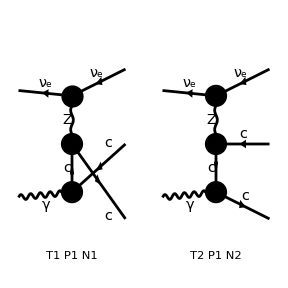

```mathematica
insertFieldseeQQbR=InsertFields[topsR,{-F[1,{1}],V[1]}->{-F[1,{1}],-F[3,{2}],F[3,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldseeQQbR,ColumnsXRows->{2,2}];
```

```mathematica
feynampR=CreateFeynAmp[insertFieldseeQQbR];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeR=CalcFeynAmp[feynampR,FermionChains->Chiral,Invariants->False,MomElim->5]/.MZ2->mz2/.MW2->mw2/.SW2->sw2;
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

```mathematica
squaredAmpQQbR=PolarizationSum[AmplitudeR,GaugeTerms->True];
```

> 64 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
Replacements2to3/.m[3]^2->0/.m[4]^2->MC2/.m[5]^2->MC2/.m[2]^2->0/.m[1]^2->0
```

{s14→s12-s13-s15,s23→s12-s24-s25,s34→s12-s15-s25,s35→s13+s15-s24,s45→-2 MC2-s13+s24+s25}

```mathematica
(* Eps[eta[2],k[1],k[4],k[5]] *)
```

```mathematica
result=Collect[
Collect[squaredAmpQQbR//.Abbr[]//.Subexpr[]/.MomReplace/.Replacements2to3/.ConjugationList/.EpsRotate/.EpsReplace/.PassarinoId2/.EpsRotate/.EpsReplace/.Replacements2to3/.m[3]^2->0/.m[4]^2->MC2/.m[5]^2->MC2/.m[2]^2->0/.m[1]^2->0,{Eps[__]},Simplify]/.Den[a_,b_]:>1/(a - b ),{Pair[__]},Simplify]
```

1/((mz2+s13) s24^2 s25^2 (s13+mz2^*))96 Alfa Alfa2 gLnu π^3 Qu^2 gLnu^* ((-2 gRu MC2^2 s13 (s24+s25)^2+gLu s13 s24 s25 (s12^2+2 s15^2+2 s15 s25+s25^2-2 s12 (s15+s25))+2 gLu MC2 (s24+s25) (s12^2 s24-s12 s24 (2 s15+s25)+s15^2 (s24+s25))+2 gRu MC2 s24 s25 (-s12^2+s12 (s24+s25)+s13 (-s13+s24+s25))) gLu^*+(gRu s13 s24 (s12^2+2 s13^2+4 s13 s15+2 s15^2-2 s12 (s13+s15)-2 s13 s24-2 s15 s24+s24^2) s25-2 gLu MC2^2 s13 (s24+s25)^2+2 gRu MC2 (s24+s25) (s12^2 s24-s12 s24 (2 s13+2 s15+s25)+(s13+s15)^2 (s24+s25))+2 gLu MC2 s24 s25 (-s12^2+s12 (s24+s25)+s13 (-s13+s24+s25))) gRu^*)

```mathematica
(* Result for implementation in c++ code, the quark result related by nc and Qe gLe gRe replacement *)
```

```mathematica
prefac=1/(s24^2 s25^2)32 Alfa Alfa2 π^3 chiz13 Conjugate[chiz13]gLnu Conjugate[gLnu]Qu^2;
```

```mathematica
CForm[prefac/.Qu->Qf]/.Conjugate->conj/.Pi->pi/.Alfa2->ALPHA^2/.Alfa->ALPHA/.Power->pow
```

32*chiz13*gLnu*conj(chiz13)*conj(gLnu)*pow(ALPHA,3)*pow(pi,3)*pow(Qf,2)*pow(s24,-2)*pow(s25,-2)

```mathematica
CForm[(result/.(mz2+s13)->1/chiz13/.(Conjugate[mz2]+s13)->1/Conjugate[chiz13])/prefac/.MM2->mfsq/.Conjugate->conj/.Power->pow]/.MC2->mfsq/.gRu->gRf/.gLu->gLf
```

3*(conj(gRf)*(2*gLf*mfsq*s24*s25*(s12*(s24 + s25) + s13*(-s13 + s24 + s25) - pow(s12,2)) + 
        2*gRf*mfsq*(s24 + s25)*(-(s12*s24*(2*s13 + 2*s15 + s25)) + s24*pow(s12,2) + 
           (s24 + s25)*pow(s13 + s15,2)) + 
        gRf*s13*s24*s25*(4*s13*s15 - 2*s12*(s13 + s15) - 2*s13*s24 - 2*s15*s24 + pow(s12,2) + 
           2*pow(s13,2) + 2*pow(s15,2) + pow(s24,2)) - 2*gLf*s13*pow(mfsq,2)*pow(s24 + s25,2)) + 
     conj(gLf)*(2*gRf*mfsq*s24*s25*(s12*(s24 + s25) + s13*(-s13 + s24 + s25) - pow(s12,2)) + 
        2*gLf*mfsq*(s24 + s25)*(-(s12*s24*(2*s15 + s25)) + s24*pow(s12,2) + (s24 + s25)*pow(s15,2)) + 
        gLf*s13*s24*s25*(2*s15*s25 - 2*s12*(s15 + s25) + pow(s12,2) + 2*pow(s15,2) + pow(s25,2)) - 
        2*gRf*s13*pow(mfsq,2)*pow(s24 + s25,2)))

### 1.4) Squared Amplitude calculation, NC lepton line: nu + gamma > nu (3) + lepton (4,5) [Complete]

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 1 Particles insertion

> Top. 15: 1 Particles insertion

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

in total: 2 Particles insertions

> Top. 1 afbg/cfdgeh/fhgh.m, 0 diagrams

> Top. 2 afbg/cfdheg/fhgh.m, 0 diagrams

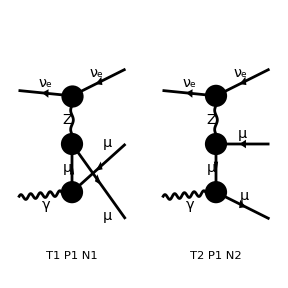

```mathematica
insertFieldseeQQbR=InsertFields[topsR,{-F[1,{1}],V[1]}->{-F[1,{1}],-F[2,{2}],F[2,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldseeQQbR,ColumnsXRows->{2,2}];
```

```mathematica
feynampR=CreateFeynAmp[insertFieldseeQQbR];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeR=CalcFeynAmp[feynampR,FermionChains->Chiral,Invariants->False,MomElim->5]/.MW2->mw2/.MZ2->mz2/.SW2->sw2;
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

```mathematica
squaredAmpQQbR=PolarizationSum[AmplitudeR,GaugeTerms->True];
```

> 64 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
(* Eps[eta[2],k[1],k[4],k[5]] *)
```

```mathematica
result=Collect[
Collect[squaredAmpQQbR//.Abbr[]//.Subexpr[]/.MomReplace/.Replacements2to3/.ConjugationList/.EpsRotate/.EpsReplace/.PassarinoId2/.EpsRotate/.EpsReplace/.Replacements2to3/.m4sq->MM2/.m5sq->MM2/.m3sq->0,{Eps[__]},Simplify][[1]]/.Den[a_,b_]:>1/(a - b ),{Pair[__]},Simplify][[1]]
```

(32 Alfa Alfa2 gLnu π^3 Qe^2 gLnu^* ((-2 gRe MM2^2 s13 (s24+s25)^2+gLe s13 s24 s25 (s12^2+2 s15^2+2 s15 s25+s25^2-2 s12 (s15+s25))+2 gLe MM2 (s24+s25) (s12^2 s24-s12 s24 (2 s15+s25)+s15^2 (s24+s25))+2 gRe MM2 s24 s25 (-s12^2+s12 (s24+s25)+s13 (-s13+s24+s25))) gLe^*+(gRe s13 s24 (s12^2+2 s13^2+4 s13 s15+2 s15^2-2 s12 (s13+s15)-2 s13 s24-2 s15 s24+s24^2) s25-2 gLe MM2^2 s13 (s24+s25)^2+2 gRe MM2 (s24+s25) (s12^2 s24-s12 s24 (2 s13+2 s15+s25)+(s13+s15)^2 (s24+s25))+2 gLe MM2 s24 s25 (-s12^2+s12 (s24+s25)+s13 (-s13+s24+s25))) gRe^*))/((mz2+s13) s24^2 s25^2 (s13+mz2^*))

```mathematica
(* Result for implementation in c++ code, the quark result related by nc and Qe gLe gRe replacement *)
```

```mathematica
prefac=1/(s24^2 s25^2)32 Alfa Alfa2 π^3 chiz13 Conjugate[chiz13]gLnu Conjugate[gLnu]Qe^2;
```

```mathematica
CForm[(result/.(mz2+s13)->1/chiz13/.(Conjugate[mz2]+s13)->1/Conjugate[chiz13])/prefac/.MM2->mfsq/.Conjugate->conj/.Power->pow]
```

conj(gRe)*(2*gLe*mfsq*s24*s25*(s12*(s24 + s25) + s13*(-s13 + s24 + s25) - pow(s12,2)) + 
      2*gRe*mfsq*(s24 + s25)*(-(s12*s24*(2*s13 + 2*s15 + s25)) + s24*pow(s12,2) + 
         (s24 + s25)*pow(s13 + s15,2)) + 
      gRe*s13*s24*s25*(4*s13*s15 - 2*s12*(s13 + s15) - 2*s13*s24 - 2*s15*s24 + 
         pow(s12,2) + 2*pow(s13,2) + 2*pow(s15,2) + pow(s24,2)) - 
      2*gLe*s13*pow(mfsq,2)*pow(s24 + s25,2)) + 
   conj(gLe)*(2*gRe*mfsq*s24*s25*(s12*(s24 + s25) + s13*(-s13 + s24 + s25) - 
         pow(s12,2)) + 2*gLe*mfsq*(s24 + s25)*
       (-(s12*s24*(2*s15 + s25)) + s24*pow(s12,2) + (s24 + s25)*pow(s15,2)) + 
      gLe*s13*s24*s25*(2*s15*s25 - 2*s12*(s15 + s25) + pow(s12,2) + 2*pow(s15,2) + 
         pow(s25,2)) - 2*gRe*s13*pow(mfsq,2)*pow(s24 + s25,2))

### 1.5) Squared Amplitude calculation, same flav: nu + gamma > nu (3) + lepton (4,5)

```mathematica
(* All diagrams, for exporting a Figure *)
```

```mathematica
insertFieldseeQQbR=InsertFields[topsR,{-F[1,{1}],V[1]}->{-F[2,{1}],-F[1,{1}],F[2,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
SetDirectory["/Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation"];
Paint[insertFieldseeQQbR,ColumnsXRows->{5,6},SheetHeader->False,Numbering->Simple,FieldNumbers->True,DisplayFunction->(Export["notes/Diagrams.pdf",#]&)];
```

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 2 Particles insertions

> Top. 16: 4 Particles insertions

> Top. 17: 1 Particles insertion

> Top. 18: 0 Particles insertions

> Top. 19: 2 Particles insertions

> Top. 20: 1 Particles insertion

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

in total: 10 Particles insertions

> Top. 1 afbg/cfdheg/fhgh.m, 0 diagrams

> Top. 2 afbg/cfdheh/fggh.m, 0 diagrams

> Top. 3 afbg/cgdfeh/fhgh.m, 0 diagrams

> Top. 4 afbg/cgdheh/fgfh.m, 0 diagrams

> Top. 5 afbg/chdfeg/fhgh.m, 0 diagrams

```mathematica
(* Now perform the computating by separating the result into Z^2, W^2, and interference type contributions *)
```

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 1 Particles insertion

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 1 Particles insertion

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 2 Particles insertions

> Top. 16: 4 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 2 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

in total: 8 Particles insertions

> Top. 1 afbg/cgdfeh/fhgh.m, 0 diagrams

> Top. 2 afbg/chdfeg/fhgh.m, 0 diagrams

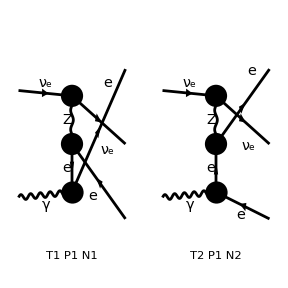

> Top. 1 afbg/cfdheg/fhgh.m, 0 diagrams

> Top. 2 afbg/cfdheh/fggh.m, 0 diagrams

> Top. 3 afbg/cgdheh/fgfh.m, 0 diagrams

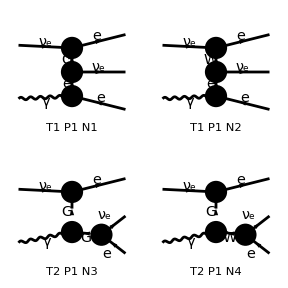

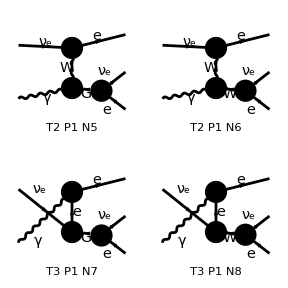

```mathematica
insertFieldseeQQbRZ=InsertFields[topsR,{F[1,{1}],V[1]}->{F[2,{1}],F[1,{1}],-F[2,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],V[2]}];
(* no Z *)
insertFieldseeQQbRnoZ=InsertFields[topsR,{F[1,{1}],V[1]}->{F[2,{1}],F[1,{1}],-F[2,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!V[2]}];
(**)
Paint[insertFieldseeQQbRZ,ColumnsXRows->{2,2}];
Paint[insertFieldseeQQbRnoZ,ColumnsXRows->{2,2}];
```

```mathematica
(* Split the computation into three parts:*)
(* Z-diagrams only *)
(* no Z-diagrams *)
(* Z * all-others *)
```

```mathematica
feynampRZ=CreateFeynAmp[insertFieldseeQQbRZ];
feynampRnoZ=CreateFeynAmp[insertFieldseeQQbRnoZ];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 4 Particles amplitudes

> Top. 3: 2 Particles amplitudes

in total: 8 Particles amplitudes

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeRZ=CalcFeynAmp[feynampRZ,FermionChains->Chiral,Invariants->False,MomElim->5];
AmplitudeRnoZ=CalcFeynAmp[feynampRnoZ,FermionChains->Chiral,Invariants->False,MomElim->5]/.Qe->-1/.Den[ME2+2 Pair[k[4],k[5]],MW2]->chiw45/.Den[ME2-2 Pair[k[1],k[3]],MW2]->chiw13//Simplify
(**)
AmplitudeRnoZtag=CalcFeynAmp[TagDiagrams[feynampRnoZ],FermionChains->Chiral,Invariants->False,MomElim->5];
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{V[1],k[2],0,{}}}→{{F[2,{1}],k[3],ME,{-Charge,LeptonNumber}},{F[1,{1}],k[4],0,{0,LeptonNumber}},{-F[2,{1}],k[5],ME,{Charge,-LeptonNumber}}}][1/(MW2 SW2)2 Alfa EL π (chiw45 Den[ME2-2 Pair[k[2],k[3]],ME2] (ME2 Mat[F1]+2 ME2 Pair1 Mat[F2]+MW2 (Mat[F3]+Mat[F4]-2 Mat[F5]+2 ME Mat[F6]+Mat[F7]+2 Mat[F8]+2 Pair1 Mat[F9]))-chiw13 (Den[ME2-2 Pair[k[2],k[5]],ME2] (ME2 Mat[F10]+MW2 Mat[F11]+2 Abb1 ME2 Mat[F2]-MW2 Mat[F4]+MW2 Mat[F7]+2 Abb1 MW2 Mat[F9])+2 chiw45 (Abb2 ME2 Mat[F2]+MW2 (-Mat[F4]+Mat[F7]+Abb2 Mat[F9]))))]

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

```mathematica
(* Just as a check, recompute the Z only *)
```

```mathematica
squaredAmpQQbRZ=PolarizationSum[AmplitudeRZ,GaugeTerms->True];
(**)
resultZ=Collect[
Collect[squaredAmpQQbRZ//.Abbr[]//.Subexpr[]/.MomReplace/.MW2->mw2/.Replacements2to3alt/.ConjugationList/.EpsRotate/.EpsReplace/.PassarinoId2/.EpsRotate/.EpsReplace/.Replacements2to3alt/.m4sq->0/.m3sq->ME2/.m5sq->ME2,{Eps[__]},Simplify]/.Den[a_,b_]:>1/(a - b )/.Qe->-1/.Qu->2/3/.Qd->-1/3,{Pair[__]},Simplify];
```

> 100 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

```mathematica
(* Z component *)
```

```mathematica
preZ=(32*Alfa*Alfa2*gLnu*Pi^3*Conjugate[gLnu]/(mz2+s14)^2)
CForm[%/.Alfa2->Conjugate[ALPHA]ALPHA/.Alfa->ALPHA/. 1/(mz2+s14)^2->chiz14 Conjugate[chiz14]]/.Power->pow/.Conjugate->conj/.Pi->pi/.mz2->mz2c
```

(32 Alfa Alfa2 gLnu π^3 gLnu^*)/(mz2+s14)^2

32*chiz14*gLnu*conj(ALPHA)*conj(chiz14)*conj(gLnu)*pow(ALPHA,2)*pow(pi,3)

```mathematica
CForm[resultZ/preZ/.gLe->gLf/.gRe->gRf/.ME2->mfsq]/.Power->pow/.Conjugate->conj
```

-(conj(gRf)*(-(gRf*(2*mfsq + s23)*s45*(s23 + s45)) + 2*gLf*s14*pow(mfsq,2))*pow(s23,-2)) - 
   conj(gLf)*(gLf*(2*mfsq + s23)*(s14 - s45)*(-s14 + s23 + s45) + 2*gRf*s14*pow(mfsq,2))*pow(s23,-2) + 
   conj(gRf)*(2*gLf*mfsq*s14*(mfsq + s14 - s23 + s35) + 
      gRf*(s12 - s23 - s45)*(2*mfsq*(s12 - s14 - s35) + (s14 - s23 + s35)*s45 - 4*pow(mfsq,2)))*
    pow(2*mfsq + s14 - s23 + s35,-2) + conj(gLf)*
    (2*gRf*mfsq*s14*(mfsq + s14 - s23 + s35) + 
      gLf*(s14 - s23 + s35)*(s14 - s23 - s45)*(-s12 + s35 + s45) - 4*gLf*s12*pow(mfsq,2) + 
      2*gLf*mfsq*((s14 - s23 + s35)*(s14 - s23 - s45) - s12*(s35 + s45) + pow(s12,2)))*
    pow(2*mfsq + s14 - s23 + s35,-2) + conj(gRf)*pow(s23,-1)*pow(2*mfsq + s14 - s23 + s35,-1)*
    (2*gLf*mfsq*(2*mfsq*s12 + s12*(s14 + s35) + s14*(-s23 + s35) - pow(s12,2)) + 
      gRf*(2*mfsq*(s12 - s23 - s45)*(s12 - s14 - s35 - s45) + s14*s23*s45 - s23*s35*s45 - 
         s12*(s23*s45 + 2*s14*(s23 + s45)) + 4*(-s12 + s23 + s45)*pow(mfsq,2) + s14*pow(s12,2) + 
         s14*pow(s23,2) + 2*s45*pow(s23,2) + s14*pow(s45,2) + 2*s23*pow(s45,2) - s35*pow(s45,2))) + 
   conj(gLf)*pow(s23,-1)*pow(2*mfsq + s14 - s23 + s35,-1)*
    (2*gRf*mfsq*(2*mfsq*s12 + s12*(s14 + s35) + s14*(-s23 + s35) - pow(s12,2)) + 
      gLf*(-2*s14*s23*s45 + 4*s14*s35*s45 - s12*s23*(s23 + s45) + s12*s14*(s23 - 2*(s35 + s45)) + 
         4*(-s12 + s23 + s45)*pow(mfsq,2) + s14*pow(s12,2) + 
         2*mfsq*(s14*(-s23 + s35 + s45) + (s23 + s45)*(s23 + s35 + s45) - 
            s12*(s14 + s23 + s35 + 2*s45) + pow(s12,2)) - s35*pow(s14,2) + s35*pow(s23,2) + 
         2*s45*pow(s23,2) + s14*pow(s35,2) + s14*pow(s45,2) + 2*s23*pow(s45,2) - s35*pow(s45,2)))

```mathematica
(* Select out subset of diagrams *)
(*AmplitudeRnoZschan=AmplitudeRnoZtag/.Diagram[1]->0/.Diagram[2]->0/.Diagram[a_]:>1/.Qe->-1//Simplify;
squaredAmpQQbRinterSchan1=PolarizationSum[AmplitudeRZ,AmplitudeRnoZschan,GaugeTerms->True];
squaredAmpQQbRinterSchan2=PolarizationSum[AmplitudeRnoZschan,AmplitudeRZ,GaugeTerms->True];
(**)
resultInterSchan=Collect[
Collect[(squaredAmpQQbRinterSchan1+squaredAmpQQbRinterSchan2)//.Abbr[]//.Subexpr[]/.MomReplace/.Replacements2to3alt/.ConjugationList/.EpsRotate/.EpsReplace/.PassarinoId2/.EpsRotate/.EpsReplace/.Replacements2to3alt/.m4sq->0/.m3sq->ME2/.m5sq->ME2,{Eps[__]},Simplify]/.Den[a_,b_]:>1/(a - b )/.Qe->-1/.Qu->2/3/.Qd->-1/3,{Pair[__]},Simplify];*)
```

```mathematica
(* Select out subset of diagrams *)
(*AmplitudeRnoZtchan=AmplitudeRnoZtag/.Diagram[1]->1/.Diagram[2]->1/.Diagram[a_]:>0/.Qe->-1//Simplify
squaredAmpQQbRinterTchan1=PolarizationSum[AmplitudeRZ,AmplitudeRnoZtchan,GaugeTerms->True];
squaredAmpQQbRinterTchan2=PolarizationSum[AmplitudeRnoZtchan,AmplitudeRZ,GaugeTerms->True];
(**)
resultInterTchan=Collect[
Collect[(squaredAmpQQbRinterTchan1+squaredAmpQQbRinterTchan2)//.Abbr[]//.Subexpr[]/.MomReplace/.Replacements2to3alt/.ConjugationList/.EpsRotate/.EpsReplace/.PassarinoId2/.EpsRotate/.EpsReplace/.Replacements2to3alt/.m4sq->0/.m3sq->ME2/.m5sq->ME2,{Eps[__]},Simplify]/.Den[a_,b_]:>1/(a - b )/.Qe->-1/.Qu->2/3/.Qd->-1/3,{Pair[__]},Simplify];*)
```

```mathematica
(* Attempt to combine all results into single expression *)
```

```mathematica
(*resultInter=Collect[
Collect[(resultInterTchan+resultInterSchan),{Eps[__]},Simplify],{Pair[__]},Simplify];*)
```

```mathematica
squaredAmpQQbRinter1=PolarizationSum[AmplitudeRZ,AmplitudeRnoZ,GaugeTerms->True];
squaredAmpQQbRinter2=PolarizationSum[AmplitudeRnoZ,AmplitudeRZ,GaugeTerms->True];
```

> 110 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

> 121 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

```mathematica
(**)
resultInter=Collect[
Collect[(squaredAmpQQbRinter1+squaredAmpQQbRinter2)//.Abbr[]//.Subexpr[]/.MomReplace/.Replacements2to3alt/.ConjugationList/.EpsRotate/.EpsReplace/.PassarinoId2/.EpsRotate/.EpsReplace/.Replacements2to3alt/.m4sq->0/.m3sq->ME2/.m5sq->ME2,{Eps[__]},Simplify]/.Den[a_,b_]:>1/(a - b )/.Qe->-1,{Pair[__]},Simplify];
```

```mathematica
(* Some manipulations for simplifications*)
```

```mathematica
chiw13 (-1+chiw45 (s12-s23))/chiw45/.s12->s23+s45+s13//Simplify
%/.chiw13->1/(ME2-s13-MW2)//Simplify
%/.chiw45->1/(ME2+s45-MW2)//Simplify
```

(chiw13 (-1+chiw45 (s13+s45)))/chiw45

(-1+chiw45 (s13+s45))/(chiw45 (ME2-MW2-s13))

-1

```mathematica
chiw13 (-1+chiw45 (s12-s23))/.s12->s23+s45-s13/.Replacements2to3alt/.m3sq->ME2/.m5sq->ME2/.m4sq->0/.(ME2-MW2+s45)->1/chiw45//Simplify
```

(-1+chiw45 (-s12+s23+2 s45))/(1/chiw45-s12+s23)

```mathematica
Replacements2to3alt
```

{s13→m3sq-m4sq-m5sq+s12-s23-s45,s24→-m3sq+m4sq-m5sq+s12-s14-s35,s25→m3sq-m4sq+m5sq+s14-s23+s35,s34→-m3sq-m4sq-m5sq+s12-s35-s45,s15→-m3sq+m4sq+m5sq-s14+s23+s45}

```mathematica
Solve[chiw13 (-1+chiw45 (s12-s23))==-chiw45]
```

{{s23→(-chiw13+chiw45+chiw13 chiw45 s12)/(chiw13 chiw45)},{chiw13→0,chiw45→0}}

{}

```mathematica
(* this is -chiw45 *)
```

```mathematica
Den[ME2+2 Pair[k[4],k[5]],MW2]->chiw45/.Den[ME2-2 Pair[k[1],k[3]],MW2]->chiw13
```

```mathematica
(* The result with real valued couplings *)
```

```mathematica
(* So just take real part of the following should work, up to some width effects *)
```

```mathematica
resultTemp1=Simplify[Collect[resultInter/.mw2->MW2/.mz2->MZ2/.Conjugate[gLnu]->gLnu/.Conjugate[gLe]->gLe/.Conjugate[gRe]->gRe/.Conjugate[chiw45]->chiw45/.Conjugate[chiw13]->chiw13,{Eps[__]},Simplify]/.(ME2-MW2+s45)->1/chiw45]/.chiw13 (-1+chiw45 (s12-s23))->-chiw45//Simplify;
```

```mathematica
(* suitable prefacto *)
```

```mathematica
prefacSameFlav=8 Alfa Alfa2 gLnu π^3/sw2/MW2 /(MZ2+s14)/s23^2/(2 ME2+s14-s23+s35)^2;
```

```mathematica
CForm[prefacSameFlav/.Alfa->ALPHA/.Alfa2->ALPHA*Conjugate[ALPHA]/.MZ2->MZ2C/.ME2->mlsq/.sw2->SW2]/.Power->pow/.Conjugate->conj/.Pi->pi
```

8*gLnu*conj(ALPHA)*pow(ALPHA,2)*pow(MW2,-1)*pow(pi,3)*pow(MZ2C + s14,-1)*pow(s23,-2)*pow(2*mlsq + s14 - s23 + s35,-2)*pow(SW2,-1)

```mathematica
Simplify[resultTemp1/prefacSameFlav/.MW2->mw2c/.ME2->mlsq/.gLe->gLf/.gRe->gRf];
CForm[%]/.Power->pow/.Conjugate->conj/.Pi->pi
```

-(chiw45*(2*mlsq + s14 - s23 + s35)*(gLf*((8*s14*(-1 + chiw13*s23) - 4*chiw13*s23*(s23 + s45))*pow(mlsq,4) + 
           2*pow(mlsq,3)*(s12*s23*(2 + chiw13*(8*mw2c + s23)) - 2*s14*s35 + s14*s23*(3 - 2*chiw13*s12 + 2*chiw13*s35) - 2*chiw13*s23*(4*mw2c + s35)*(s23 + s45) + 
              2*(-1 + chiw13*s23)*pow(s14,2) - 2*chiw13*s14*pow(s23,2)) + 
           pow(mlsq,2)*(-8*mw2c*(-(s12*s23*(-1 + chiw13*(4*s23 + 2*s35 + 3*s45))) + chiw13*s23*pow(s12,2) + 2*(-1 + chiw13*s23)*pow(s14,2) + 
                 (s23 + s45)*(-2*s45 + s23*(-1 + 3*chiw13*s35 + 4*chiw13*s45) + chiw13*pow(s23,2)) - 
                 s14*(-4*s45 + s23*(-2 + chiw13*s12 + 3*chiw13*s45) + 2*chiw13*pow(s23,2))) + 
              s23*(2*s12*s35 + 3*s14*s35 - chiw13*s12*(2*s14 - s23)*(s14 + s35) - 2*s14*s23*(1 + chiw13*s35) - 2*pow(s12,2) + pow(s14,2) + 
                 chiw13*(-s23 + s45)*pow(s14,2) + 2*chiw13*s14*pow(s23,2) - chiw13*(s23 + s45)*pow(s35,2))) - 
           4*mlsq*mw2c*(s23*(-1 + chiw13*(4*s23 + s35 + s45))*pow(s12,2) + 2*(-1 + chiw13*s23)*pow(s14,3) - 
              pow(s14,2)*(2*(s35 - 2*s45) + s23*(-2 + chiw13*(s12 - 2*s35 + 3*s45)) + chiw13*pow(s23,2)) + 
              s14*(2*(2*s35 - s45)*s45 + s12*s23*(1 + chiw13*s23 - chiw13*(s35 + s45)) + s23*(s35 - 2*chiw13*s35*s45 + s45*(-3 + 2*chiw13*s45)) + 
                 chiw13*s23*pow(s12,2) - (-1 + chiw13*(s35 + s45))*pow(s23,2) - 3*chiw13*pow(s23,3)) + 
              s12*s23*(s35 - 5*chiw13*s35*s45 + s23*(1 - 7*chiw13*s35 - 8*chiw13*s45) + s45*(2 - 3*chiw13*s45) - 2*chiw13*pow(s23,2) - chiw13*pow(s35,2)) + 
              (s23 + s45)*(-2*s35*s45 + (-1 + chiw13*(s35 + 3*s45))*pow(s23,2) + 2*chiw13*pow(s23,3) + 
                 s23*(s45*(-1 + 2*chiw13*s45) + s35*(-1 + 6*chiw13*s45) + 3*chiw13*pow(s35,2)))) + 
           2*mw2c*s23*(chiw13*s23*pow(s12,3) - (-2 + chiw13*(2*s23 + s45))*pow(s14,3) + 
              pow(s14,2)*(s35 - 2*s23*(2 + chiw13*(s35 - 3*s45)) - chiw13*s35*s45 + 2*s45*(-2 + chiw13*s45) + 4*chiw13*pow(s23,2)) - 
              pow(s12,2)*(s14*(-1 + chiw13*s45) + chiw13*(s35*s45 + 3*s23*(s35 + s45) + pow(s23,2))) + 
              s14*((2 + 4*chiw13*s35 - 5*chiw13*s45)*pow(s23,2) - 2*chiw13*pow(s23,3) + (1 - chiw13*s45)*pow(s35,2) - 
                 s23*(s35*(2 - 4*chiw13*s45) + s45*(-4 + 5*chiw13*s45) + chiw13*pow(s35,2)) + (3 - 2*chiw13*s45)*pow(s45,2)) - 
              s35*(s23 + s45)*(-s45 + s23*(-1 + 3*chiw13*s45) + 2*chiw13*pow(s23,2) + chiw13*(2*s35*s45 + pow(s35,2) + 2*pow(s45,2))) + 
              s12*(-(s23*(s23 + s45)) + s14*(s23 - 2*(s35 + s45)) + 
                 chiw13*(s35*s45*(2*s35 + 3*s45) + (-s23 + s35 - 2*s45)*pow(s14,2) + pow(s14,3) + (s35 + 3*s45)*pow(s23,2) + 2*pow(s23,3) + 
                    s23*(6*s35*s45 + 3*pow(s35,2) + 2*pow(s45,2)) + s14*(2*s23*s45 - 2*pow(s23,2) + 3*pow(s45,2)))))) + 
        gRf*mlsq*(4*pow(mlsq,2)*(s12*s23*(-1 + chiw13*(s23 + s45)) - 2*mw2c*(s14*(2 - 2*chiw13*s23) + chiw13*s23*(2*s12 + s23 + s45)) - 
              (-1 + chiw13*s23)*(3*s23*s45 + pow(s23,2) + 2*pow(s45,2))) + 
           2*mlsq*(-((s23 + s45)*(-(s23*s35) - s23*s45 - 2*s35*s45 + s14*(-1 + chiw13*s23)*(s23 + 2*s45) + chiw13*s23*(s23 + s35 + s45)*(s23 + 2*s45))) - 
              s23*(-1 + chiw13*(2*s23 + s45))*pow(s12,2) + 2*mw2c*
               (s14*(s23 - 4*chiw13*s12*s23 - 2*s35 + 2*chiw13*s23*s35) + 
                 s23*(s12*(2 + chiw13*s23 - 4*chiw13*s35) - 2*chiw13*s35*(s23 + s45) + 2*chiw13*pow(s12,2)) + 2*(-1 + chiw13*s23)*pow(s14,2)) + 
              s12*s23*(-s35 - 2*s45 + chiw13*s35*s45 + s23*(-1 + chiw13*s35 + 7*chiw13*s45) + s14*(-1 + chiw13*(s23 + s45)) + 3*chiw13*pow(s23,2) + 
                 3*chiw13*pow(s45,2))) + s23*(3*s14*s23*s45 + s23*s35*s45 + chiw13*s23*pow(s12,3) + s14*pow(s23,2) - 4*chiw13*s14*s45*pow(s23,2) - 
              4*chiw13*s35*s45*pow(s23,2) + s12*(-(s23*s45) + s14*(s23 + s45)*(-2 + 2*chiw13*s23 + 3*chiw13*s45) + 
                 chiw13*(s23 + s45)*(3*s35*s45 + 2*s23*(s35 + s45) + pow(s23,2))) - 
              pow(s12,2)*(s14*(-1 + chiw13*(s23 + s45)) + chiw13*(s35*s45 + s23*(s35 + 3*s45) + 2*pow(s23,2))) - chiw13*s14*pow(s23,3) - chiw13*s35*pow(s23,3) + 
              2*mw2c*(2*(-1 + chiw13*(s14 + s35))*pow(s12,2) + (-1 + chiw13*(s23 + s45))*pow(s14,2) + 
                 s12*(s14*(4 - 3*chiw13*s23 - 4*chiw13*s35) + s35*(2 + chiw13*s23 - 2*chiw13*s35) - 2*chiw13*pow(s14,2)) + 
                 s14*(-2*s23 + s35 + 2*chiw13*pow(s23,2)) - chiw13*(s23 + s45)*pow(s35,2)) + 3*s14*pow(s45,2) - 5*chiw13*s14*s23*pow(s45,2) + s35*pow(s45,2) - 
              5*chiw13*s23*s35*pow(s45,2) - 2*chiw13*s14*pow(s45,3) - 2*chiw13*s35*pow(s45,3))))) - 
   chiw13*s23*(gRf*mlsq*(4*(2*mw2c*(2*s12 + s14) + (s12 - s23 - s45)*(s12 - 2*s14 - s23 - 2*s35 - s45))*pow(mlsq,2) + 8*(-s12 + s23 + s45)*pow(mlsq,3) + 
         2*mlsq*(2*s14*s23*s35 + 3*s14*s23*s45 + 2*s14*s35*s45 + s23*s35*s45 + mw2c*(4*s12*(s14 - s23 + 2*s35) + 2*s14*(2*s14 - s23 + 4*s35) - 4*pow(s12,2)) + 
            (2*s14 + s23 + s35)*pow(s12,2) + s23*pow(s14,2) + s45*pow(s14,2) + 2*s14*pow(s23,2) + s35*pow(s23,2) + s45*pow(s23,2) + s23*pow(s35,2) + 
            s45*pow(s35,2) - s12*(2*s23*s35 + s23*s45 + 2*s35*s45 + 2*s14*(2*s23 + s35 + 2*s45) + pow(s14,2) + pow(s23,2) + pow(s35,2)) + 2*s14*pow(s45,2) + 
            s23*pow(s45,2)) + (s14 - s23 + s35)*(4*mw2c*s12*s35 + 2*mw2c*s14*(s14 + 2*s23 + 3*s35) + s12*s23*s45 + s14*s23*s45 - s23*s35*s45 - 
            2*s12*s14*(s23 + s45) - 4*mw2c*pow(s12,2) + s14*pow(s12,2) + s14*pow(s23,2) + s14*pow(s45,2) - s35*pow(s45,2))) + 
      gLf*((8*s12 - 4*s14)*pow(mlsq,4) - 2*pow(mlsq,3)*(s14*(2*s14 - s23) + s12*(-6*s14 + 2*s23 - 4*s35) + 8*mw2c*(s12 - s23 - s45) + 2*pow(s12,2)) + 
         pow(mlsq,2)*(8*mw2c*(-2*s12*(s14 + s23 + s35 + s45) + (s23 + s45)*(2*s35 + s45) + s14*(s35 + 2*s45) + pow(s12,2)) - 
            (s14 - s23 + s35)*(s14*(s14 - 2*s23 - s35) - 2*s12*(2*s14 + s35) + 2*pow(s12,2))) + 
         4*mlsq*mw2c*((2*s14 + s23 + s35)*pow(s12,2) + (s23 + s45)*pow(s14,2) - 
            s12*(-(s14*s23) + 4*s14*(s35 + s45) + s23*(2*s35 + s45) + s35*(s35 + 2*s45) + pow(s14,2)) + (s23 + s45)*(s23*(-s35 + s45) + pow(s23,2) + pow(s35,2)) + 
            s14*(s23*(s35 - 3*s45) - 2*pow(s23,2) + 2*(3*s35*s45 + pow(s35,2) + pow(s45,2)))) + 
         2*mw2c*(s14 - s23 + s35)*(s12*s23*(s23 + s45) - s12*s14*(s23 + 2*(s35 + s45)) + s14*pow(s12,2) - s35*pow(s14,2) + 
            s14*(2*s23*s35 + 4*s35*s45 + pow(s35,2) + pow(s45,2)) - s35*pow(s23 + s45,2))))

### 1.5) Squared Amplitude calculation, same flav: nu + gamma > nu (3) + lepton (4,5)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 1 Particles insertion

> Top. 15: 1 Particles insertion

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 2 Particles insertions

> Top. 21: 4 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 2 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

in total: 10 Particles insertions

> Top. 1 afbg/cfdgeh/fhgh.m, 0 diagrams

> Top. 2 afbg/cfdheg/fhgh.m, 0 diagrams

> Top. 3 afbg/chdfeg/fhgh.m, 0 diagrams

> Top. 4 afbg/chdfeh/fggh.m, 0 diagrams

> Top. 5 afbg/chdgeh/fgfh.m, 0 diagrams

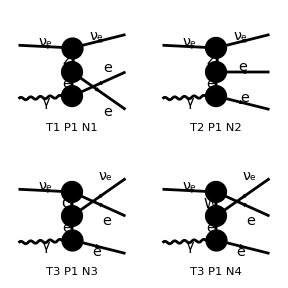

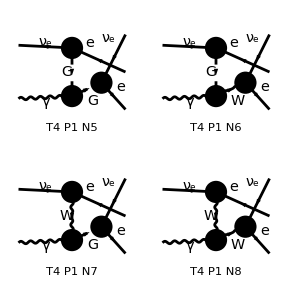

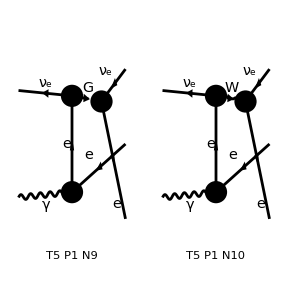

```mathematica
insertFieldseeQQbR=InsertFields[topsR,{-F[1,{1}],V[1]}->{-F[1,{1}],-F[2,{1}],F[2,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldseeQQbR,ColumnsXRows->{2,2}];
```

```mathematica
feynampR=CreateFeynAmp[insertFieldseeQQbR];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 4 Particles amplitudes

> Top. 3: 2 Particles amplitudes

in total: 8 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeR=CalcFeynAmp[feynampR,FermionChains->Chiral,Invariants->False,MomElim->5]/.MW2->mw2/.SW2->sw2;
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

```mathematica
squaredAmpQQbR=PolarizationSum[AmplitudeR,GaugeTerms->True];
```

> 121 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
(* Eps[eta[2],k[1],k[4],k[5]] *)
```

```mathematica
result=Collect[
Collect[squaredAmpQQbR//.Abbr[]//.Subexpr[]/.MomReplace/.Replacements2to3/.m4sq->0/.m5sq->MM2/.m3sq->ME2/.ConjugationList/.EpsRotate/.EpsReplace/.PassarinoId2/.EpsRotate/.EpsReplace/.Replacements2to3/.m5sq->MM2,{Eps[__]},Simplify][[1]]/.Den[a_,b_]:>1/(a - b )/.Qd->Qe/3/.Qu->-Qe*2/3/.Qe->-1,{Pair[__]},Simplify][[1]]
```

(Alfa Alfa2 π^3 (ME2 MM2 (2 ME2^4 s25 (s12^2+2 s13 s24+s12 (-2 s13-s24+s25))-2 ME2^3 (2 MM2 (s12^2 s13+s13 s24 (s24+2 s25)+s12 (s25^2-2 s13 (s24+s25)))+s25 (8 s13^2 s24+2 s13 s15 s24-6 s13 s24^2-s15 s24^2+s12^2 (3 s13-3 s24-s25)+2 s13^2 s25+2 s13 s15 s25-7 s13 s24 s25-2 s15 s24 s25-s13 s25^2-s15 s25^2+mw2 (5 s12^2+6 s13 s24+4 s15 s24+s12 (-6 s13-4 s15-5 s24+s25))+s12 (-8 s13^2+(s15+3 s24-s25) (s24+s25)+s13 (-2 s15+3 s24+6 s25))))+ME2^2 (-2 MM2^2 (s12-s24-s25) (2 s13 s24+s12 (-2 s13+s25))-2 MM2 (-6 s13^2 s24^2+4 s13 s24^3-12 s13^2 s24 s25-2 s13 s15 s24 s25+14 s13 s24^2 s25+s15 s24^2 s25-2 s13^2 s25^2-2 s13 s15 s25^2+11 s13 s24 s25^2+2 s15 s24 s25^2+s13 s25^3+s15 s25^3+s12^2 (-6 s13^2+4 s13 s24+5 s13 s25-2 s25^2)+s12 (12 s13^2 (s24+s25)-(s15-2 s25) s25 (s24+s25)-s13 (8 s24^2-2 s15 s25+19 s24 s25+10 s25^2))+2 mw2 (2 s12^3+s12 (6 s13 s24+4 s15 s24+2 s24^2+4 s13 s25+2 s15 s25+2 s24 s25-s25^2)-s12^2 (3 s13+2 (s15+2 s24+s25))-s24 (2 s15 (s24+s25)+s13 (3 s24+4 s25))))+s25 (8 mw2^2 (s12-s13-s15) (s12-s24)+2 (6 s13^2 (s15-3 s24-s25) (s24+s25)-s13 (6 s15-7 s24-2 s25) (s24+s25)^2+2 s15 (s24+s25)^3+6 s13^3 (2 s24+s25)-s12 (12 s13^3+s13^2 (6 s15-15 s24-13 s25)-s13 (6 s15-s24-4 s25) (s24+s25)+(2 s15+3 s24) (s24+s25)^2)+s12^2 (3 s13^2+3 s24 (s24+s25)-2 s13 (3 s24+s25)))+mw2 (4 s12^3+s12^2 (22 s13-37 s24-7 s25)+2 s15 (4 s15-13 s24-s25) (s24+s25)+12 s13^2 (3 s24+s25)+4 s13 s15 (9 s24+5 s25)-2 s13 (16 s24^2+17 s24 s25+s25^2)+s12 (-36 s13^2-8 s15^2+26 s15 s24+33 s24^2+2 s15 s25+32 s24 s25-s25^2+s13 (-36 s15+10 s24+8 s25)))))-ME2 (2 MM2^2 (s12-s24-s25) (4 s13 s24 (-s13+s24+s25)+mw2 (2 s12 s13-2 s13 s24-s12 s25)+s12 (4 s13^2-4 s13 (s24+s25)+s25 (s24+s25)))-2 MM2 (-6 s13^3 s24^2+8 s13^2 s24^3-2 s13 s24^4+4 mw2^2 (s12-s13-s15) (s12-s24) (s12-s24-s25)-12 s13^3 s24 s25-4 s13^2 s15 s24 s25+28 s13^2 s24^2 s25+4 s13 s15 s24^2 s25-12 s13 s24^3 s25-s15 s24^3 s25-4 s13^3 s25^2-4 s13^2 s15 s25^2+24 s13^2 s24 s25^2+8 s13 s15 s24 s25^2-19 s13 s24^2 s25^2-3 s15 s24^2 s25^2+4 s13^2 s25^3+4 s13 s15 s25^3-10 s13 s24 s25^3-3 s15 s24 s25^3-s13 s25^4-s15 s25^4+s12^2 (-6 s13^3+s25^2 (s24+s25)+2 s13^2 (4 s24+5 s25)-s13 (2 s24^2+7 s24 s25+5 s25^2))+s12 (12 s13^3 (s24+s25)+(s15-s25) s25 (s24+s25)^2-2 s13^2 (8 s24^2+19 s24 s25-2 (s15-4 s25) s25)+s13 (s24+s25) (4 s24^2-4 s15 s25+15 s24 s25+6 s25^2))+mw2 (s15 (s24+s25)^2 (8 s24+s25)-2 s13^2 (6 s24^2+8 s24 s25+s25^2)+s12^3 (8 s13-2 (4 s24+s25))+s13 (s24+s25) (10 s24^2+14 s24 s25+s25^2-2 s15 (4 s24+s25))+s12^2 (-12 s13^2+8 s15 s24+16 s24^2+4 s15 s25+16 s24 s25+s25^2-s13 (8 s15+6 s24+s25))+s12 (8 s13^2 (3 s24+2 s25)+s13 (16 s15 s24-12 s24^2+10 s15 s25-23 s24 s25-10 s25^2)-(s24+s25) (16 s15 s24+8 s24^2+5 s15 s25+6 s24 s25-s25^2))))+s25 (2 mw2^2 (s12^3+s12^2 (6 s13+2 s15-12 s24-s25)+s12 (-8 s13^2-4 s15^2+s15 (6 s24-2 s25)-2 s13 (6 s15-s24+s25)+11 s24 (s24+s25))+4 (s13+s15) ((s15-2 s24) (s24+s25)+s13 (2 s24+s25)))+2 (-s13^2 (9 s15-14 s24-5 s25) (s24+s25)^2+s13 (5 s15-4 s24-s25) (s24+s25)^3-s15 (s24+s25)^4-3 s13^3 (s24+s25) (-2 s15+6 s24+3 s25)+s13^4 (8 s24+6 s25)+s12^2 (s13^3+3 s13 s24 (s24+s25)-s24 (s24+s25)^2-s13^2 (3 s24+s25))+s12 (-8 s13^4+s13^2 (9 s15-11 s24-6 s25) (s24+s25)-s13 (5 s15-s24-s25) (s24+s25)^2+(s15+s24) (s24+s25)^3+s13^3 (-6 s15+17 s24+12 s25)))+mw2 (4 s12^3 (2 s13-3 s24)-s15 (8 s15-23 s24-3 s25) (s24+s25)^2+12 s13^3 (3 s24+2 s25)+s12^2 (14 s13^2-57 s13 s24+4 s15 s24+44 s24^2-17 s13 s25-4 s15 s25+37 s24 s25+s25^2)+s13 (s24+s25) (16 s15^2+30 s24^2+29 s24 s25+3 s25^2-8 s15 (8 s24+3 s25))+8 s13^2 (s15 (6 s24+5 s25)-2 (4 s24^2+5 s24 s25+s25^2))+s12 (-36 s13^3+s13^2 (-48 s15+50 s24+18 s25)-(s24+s25) (-8 s15^2+27 s15 s24+32 s24^2-s15 s25+25 s24 s25+s25^2)+s13 (-16 s15^2+64 s15 s24+19 s24^2+24 s15 s25+25 s24 s25+2 s25^2)))))+(s12-s24-s25) (MM2^2 (-2 s13 (s13-s24-s25) (-2 s24 (-s13+s24+s25)+s12 (-2 s13+2 s24+s25))+mw2 (4 s13 s24 (-s13+s24+s25)+s12 (4 s13^2-4 s13 (s24+s25)+s25 (s24+s25))))+s25 (-2 s13 (s13+s15-s24) (2 s13^3-4 s13^2 (s24+s25)+3 s13 (s24+s25)^2-(s24+s25)^3)+2 mw2^2 (-4 s13^3+s12^2 (s13-3 s24)+s15 (2 s15-3 s24) (s24+s25)+s13^2 (-8 s15+8 s24+2 s25)+s13 (-4 s15^2+10 s15 s24-4 s24^2+4 s15 s25-3 s24 s25)+s12 (2 s13^2+s15 s24+5 s24^2+s13 (2 s15-7 s24-s25)-s15 s25+4 s24 s25))+mw2 (-12 s13^4+s15 (s24+s25)^2 (5 s24+s25)+s13^3 (-20 s15+32 s24+14 s25)-2 s13^2 (4 s15^2-19 s15 s24+15 s24^2-11 s15 s25+15 s24 s25+2 s25^2)+4 s12^2 (s13^2-3 s13 s24+s24 (2 s24+s25))+s13 (s24+s25) (8 s15^2+10 s24^2+7 s24 s25+s25^2-4 s15 (6 s24+s25))+s12 (2 s13^3-2 s13^2 (8 s24+3 s25)-s24 (s24+s25) (4 s15+9 s24+5 s25)+s13 (4 s15 s24+23 s24^2-4 s15 s25+20 s24 s25+s25^2))))-MM2 (mw2^2 (8 (s13+s15) s24 (s13-s24-s25)+s12 (-8 s13^2-8 s13 s15+8 s15 s24+8 s24^2+4 s13 s25+4 s15 s25+6 s24 s25)+s12^2 (8 s13-2 (4 s24+s25)))+2 s13 ((s13-s24-s25) (2 s13^2 (s24+s25)-(s15-2 s24) s25 (s24+s25)-s13 (2 s24^2-2 s15 s25+6 s24 s25+s25^2))+s12 (-2 s13^3+s13^2 (4 s24+5 s25)+s25 (2 s24^2+3 s24 s25+s25^2)-s13 (2 s24^2+7 s24 s25+3 s25^2)))+mw2 (4 s12^2 (s13-s24) (2 s13-2 s24-s25)+4 s13^3 (3 s24+s25)+s15 (s24+s25)^2 (8 s24+s25)-4 s13^2 (5 s24^2+7 s24 s25+s25^2-s15 (2 s24+s25))+s13 (s24+s25) (8 s24^2+12 s24 s25+s25^2-4 s15 (4 s24+s25))+s12 (-12 s13^3+s13^2 (-8 s15+12 s24+14 s25)-(s24+s25) (8 s15 s24+8 s24^2+4 s24 s25-s25^2)+s13 (8 s24^2+s24 s25-3 s25^2+8 s15 (2 s24+s25)))))))-(2 ME2^4 s25 (MM2 (5 s12^2+6 s13 s24+4 s15 s24+s12 (-6 s13-4 s15-5 s24+s25))+4 mw2 (s12^2+2 s15 s24-s12 (2 s15+s24+s25)))+ME2^2 (-2 MM2^3 (s12-s24-s25) (2 s13 s24+s12 (-2 s13+s25))-2 MM2^2 (-12 s13^2 s24^2-8 s13 s15 s24^2+10 s13 s24^3+8 s15 s24^3-16 s13^2 s24 s25-10 s13 s15 s24 s25+24 s13 s24^2 s25+17 s15 s24^2 s25-2 s13^2 s25^2-2 s13 s15 s25^2+15 s13 s24 s25^2+10 s15 s24 s25^2+s13 s25^3+s15 s25^3+s12^3 (8 s13-2 (4 s24+s25))+s12^2 (-12 s13^2+8 s15 s24+16 s24^2+4 s15 s25+16 s24 s25+s25^2-s13 (8 s15+6 s24+s25))+s12 (8 s13^2 (3 s24+2 s25)+s13 (16 s15 s24-12 s24^2+10 s15 s25-23 s24 s25-10 s25^2)-(s24+s25) (16 s15 s24+8 s24^2+5 s15 s25+6 s24 s25-s25^2))+2 mw2 (8 s12^3-s12^2 (5 s13+8 s15+16 s24+10 s25)+s12 (10 s13 s24+16 s15 s24+8 s24^2+6 s13 s25+8 s15 s25+10 s24 s25+s25^2)-s24 (8 s15 (s24+s25)+s13 (5 s24+6 s25))))+MM2 (-8 mw2^2 (2 s12^3-s12^2 (2 s15+4 s24+5 s25)-s24 (2 s15 s24+s13 s25+5 s15 s25)+s12 (4 s15 s24+2 s24^2+s13 s25+5 s15 s25+5 s24 s25+2 s25^2))+s25 (4 s12^3 (2 s13-3 s24)-s15 (8 s15-23 s24-3 s25) (s24+s25)^2+12 s13^3 (3 s24+2 s25)+s12^2 (14 s13^2-57 s13 s24+4 s15 s24+44 s24^2-17 s13 s25-4 s15 s25+37 s24 s25+s25^2)+s13 (s24+s25) (16 s15^2+30 s24^2+29 s24 s25+3 s25^2-8 s15 (8 s24+3 s25))+8 s13^2 (s15 (6 s24+5 s25)-2 (4 s24^2+5 s24 s25+s25^2))+s12 (-36 s13^3+s13^2 (-48 s15+50 s24+18 s25)-(s24+s25) (-8 s15^2+27 s15 s24+32 s24^2-s15 s25+25 s24 s25+s25^2)+s13 (-16 s15^2+64 s15 s24+19 s24^2+24 s15 s25+25 s24 s25+2 s25^2)))-2 mw2 (8 s12^4+2 s12^3 (8 s13-8 s15-16 s24-13 s25)-10 s13^2 s25 (2 s24+s25)+s15 (s24+s25) (16 s24^2+8 s15 (s24-2 s25)+53 s24 s25-3 s25^2)+s12^2 (8 s15^2+48 s15 s24+40 s24^2+28 s15 s25+98 s24 s25+28 s25^2-s13 (16 s15+32 s24+51 s25))-s13 (3 s25 (-6 s24^2-5 s24 s25+s25^2)+2 s15 (8 s24^2+33 s24 s25+13 s25^2))+s12 (20 s13^2 s25+8 s15^2 (-2 s24+s25)-s15 (48 s24^2+97 s24 s25+9 s25^2)+s13 (32 s15 s24+16 s24^2+66 s15 s25+33 s24 s25+26 s25^2)-8 (2 s24^3+9 s24^2 s25+8 s24 s25^2+s25^3))))+4 mw2 s25 (mw2 (s12^3+s12^2 (4 s13-2 s15-3 s24-2 s25)+2 (-3 s15 s24^2-2 s15 s24 s25+s15 s25 (2 s15+s25)+s13 s25 (s24+s25)+2 s13 s15 (2 s24+s25))+s12 (8 s15 s24+2 s24^2+3 s24 s25+s25^2-2 s13 (4 s15+2 s24+3 s25)))+2 (s12^3 (3 s13+s15-2 s24)+s15 (s24+s25) (-2 s15^2+4 s24^2+2 s15 (s24-2 s25)+3 s24 s25-2 s25^2)+2 s13^2 (s25 (s24+s25)+s15 (3 s24+2 s25))+s12^2 (3 s13^2-2 s15^2+4 s15 (s24-s25)+s24 (3 s24+4 s25)-s13 (6 s15+7 s24+8 s25))-2 s13 (s15^2 (s24-s25)+s25 (s24+s25)^2+s15 (5 s24^2+6 s24 s25+s25^2))+s12 (2 s15^3+6 s15^2 s25-s13^2 (6 s15+3 s24+5 s25)-s24 (s24^2+3 s24 s25+2 s25^2)+s15 (-9 s24^2-5 s24 s25+5 s25^2)+s13 (2 s15^2+4 s24^2+11 s24 s25+7 s25^2+8 s15 (2 s24+s25))))))+ME2^3 (4 MM2^2 (2 s12^3+s12 (6 s13 s24+4 s15 s24+2 s24^2+4 s13 s25+2 s15 s25+2 s24 s25-s25^2)-s12^2 (3 s13+2 (s15+2 s24+s25))-s24 (2 s15 (s24+s25)+s13 (3 s24+4 s25)))-8 mw2 s25 (s12^3+6 s13 s15 s24-5 s15 s24^2+s12^2 (3 s13-2 s15-3 s24-2 s25)+2 s13 s15 s25+2 s15^2 s25+s13 s24 s25-4 s15 s24 s25+s13 s25^2+s15 s25^2+mw2 (s12^2+2 s15 s24-s12 (2 s15+s24+s25))+s12 (7 s15 s24+2 s24^2+s15 s25+3 s24 s25+s25^2-s13 (6 s15+3 s24+4 s25)))+MM2 (2 mw2 (8 s12^3-s12^2 (8 s15+16 s24+25 s25)-2 s24 (5 s13 s25+4 s15 (s24+3 s25))+s12 (8 s24^2+10 s13 s25+25 s24 s25+7 s25^2+8 s15 (2 s24+3 s25)))+s25 (-4 s12^3+s12^2 (-22 s13+37 s24+7 s25)+s12 (36 s13^2+8 s15^2-33 s24^2+2 s13 (18 s15-5 s24-4 s25)-32 s24 s25+s25^2-2 s15 (13 s24+s25))+2 (-s15 (4 s15-13 s24-s25) (s24+s25)-6 s13^2 (3 s24+s25)+s13 (16 s24^2+17 s24 s25+s25^2-2 s15 (9 s24+5 s25))))))+4 mw2 (s12-s24-s25) (-s25 (s12^2+2 s15^2+2 s15 s25+s25^2-2 s12 (s15+s25)) (-2 s13 (s13+s15-s24) (s13-s24-s25)+mw2 (-2 s13^2+s12 (s13-s24)+s15 (s24+s25)+s13 (-2 s15+2 s24+s25)))+MM2^2 (-2 s12^2 (s13-s24) (2 s13-2 s24-s25)-4 s15 s24 (-s13+s24+s25)^2+2 s12 (s13-s24) (s13-s24-s25) (2 s15+2 s24+s25)+mw2 (4 s15 s24 (-s13+s24+s25)+s12 (2 s13-2 s24-s25) (2 s15+2 s24+s25)+s12^2 (-4 s13+4 s24+s25)))+MM2 (mw2 (s12^3 (-4 s13+4 s24+s25)-s12^2 (4 s24^2+7 s24 s25+2 s25^2+2 s15 (4 s24+s25)-s13 (8 s15+4 s24+5 s25))+(2 s15+s25) (2 s13 s15 (s24-s25)-2 s13^2 s25+s13 s25 (2 s24+s25)+s15 (-2 s24^2-s24 s25+s25^2))+s12 (2 s13^2 s25+2 s15^2 (2 s24+s25)+s25 (4 s24^2+3 s24 s25+s25^2)+s15 (8 s24^2+7 s24 s25+s25^2)-2 s13 (2 s15^2+s25 (3 s24+s25)+s15 (4 s24+s25))))-2 (s12^3 (s13-s24) (2 s13-2 s24-s25)-s12^2 (s13-s24) (-((2 s24+s25) (2 s15+s24+2 s25))+s13 (4 s15+2 s24+3 s25))+(s13-s24-s25) (2 s15+s25) (s13^2 s25+s15 s24 (s24+s25)-s13 (s15 (s24-s25)+s24 s25))+s12 (-s13^3 s25+s24 (2 s15+s25) (s24+s25) (s15+2 s24+s25)+2 s13^2 (s15^2+s15 (2 s24+s25)+s25 (2 s24+s25))-s13 (2 s15^2 (2 s24+s25)+s25 (5 s24^2+5 s24 s25+s25^2)+s15 (8 s24^2+9 s24 s25+s25^2))))))+ME2 (-MM2^3 (s12-s24-s25) (4 s13 s24 (-s13+s24+s25)+mw2 (4 s12 s13-4 s13 s24-2 s12 s25)+s12 (4 s13^2-4 s13 (s24+s25)+s25 (s24+s25)))+MM2^2 (s12-s24-s25) (12 s13^3 s24+8 s13^2 s15 s24-20 s13^2 s24^2-16 s13 s15 s24^2+8 s13 s24^3+8 s15 s24^3+4 s12^2 (s13-s24) (2 s13-2 s24-s25)+4 s13^3 s25+4 s13^2 s15 s25-28 s13^2 s24 s25-20 s13 s15 s24 s25+20 s13 s24^2 s25+17 s15 s24^2 s25-4 s13^2 s25^2-4 s13 s15 s25^2+13 s13 s24 s25^2+10 s15 s24 s25^2+s13 s25^3+s15 s25^3+8 mw2^2 (3 s12^2+(s13+3 s15) s24-s12 (s13+3 s15+3 s24+s25))+s12 (-12 s13^3+s13^2 (-8 s15+12 s24+14 s25)-(s24+s25) (8 s15 s24+8 s24^2+4 s24 s25-s25^2)+s13 (8 s24^2+s24 s25-3 s25^2+8 s15 (2 s24+s25)))+2 mw2 (6 s12^2 (4 s13-4 s24-s25)+2 s13^2 (5 s24+s25)-s15 (24 s24^2+25 s24 s25+s25^2)-s13 (8 s24^2+10 s24 s25+s25^2-2 s15 (12 s24+s25))+s12 (-10 s13^2+24 s24^2+22 s24 s25+4 s25^2+12 s15 (2 s24+s25)-s13 (24 s15+16 s24+3 s25))))+4 mw2 s25 (mw2 (s12^4-2 s13^2 (2 s15+s25) (s24+s25)-s12^3 (3 s13+4 s15+3 s25)+s15 (s24+s25) (4 s15^2-2 s15 s24-2 s24^2+6 s15 s25-s24 s25+3 s25^2)+s12^2 (-2 s13^2+6 s15^2-s24^2+3 s25^2+s13 (6 s15+5 s24+9 s25)+s15 (s24+11 s25))+s13 (4 s15^2 s24+2 s15 (3 s24^2+5 s24 s25+2 s25^2)+s25 (2 s24^2+5 s24 s25+3 s25^2))+s12 (-4 s15^3+2 s13^2 (2 s15+s24+2 s25)-4 s15^2 (s24+3 s25)+s15 (5 s24^2-3 s24 s25-10 s25^2)+s25 (s24^2-s25^2)-s13 (4 s15^2+2 s24^2+10 s24 s25+9 s25^2+2 s15 (6 s24+5 s25))))-2 (s13^3 (2 s15+s25) (s24+s25)+s15 (s24+s25)^2 (2 s15^2-2 s15 s24-s24^2+2 s15 s25-s24 s25+s25^2)+s12^3 (3 s13^2+s24^2+s13 (2 s15-4 s24-s25)-s15 (s24+s25))+s13 (s24+s25) (-4 s15^3+s15^2 (6 s24-4 s25)+s15 (4 s24^2+7 s24 s25-s25^2)+s25 (s24^2+3 s24 s25+s25^2))-s13^2 (5 s15 (s24+s25)^2+2 s15^2 (2 s24+s25)+s25 (2 s24^2+5 s24 s25+3 s25^2))+s12^2 (s13^3+2 s15^2 (s24+s25)-s24^2 (s24+2 s25)-s13^2 (6 s15+5 s24+9 s25)+s15 (-2 s24^2+3 s24 s25+3 s25^2)+s13 (-4 s15^2+7 s15 s24+5 s24^2-5 s15 s25+12 s24 s25+3 s25^2))-s12 (s13^3 (2 s15+s24+2 s25)+(s24+s25) (2 s15^3-4 s15 s24^2+4 s15^2 s25-s24^2 s25+3 s15 s25^2)-s13^2 (4 s15^2+2 s24^2+10 s24 s25+9 s25^2+11 s15 (s24+s25))+s13 (-4 s15^3+s24^3+2 s15^2 (s24-4 s25)+9 s24^2 s25+12 s24 s25^2+3 s25^3+s15 (13 s24^2+13 s24 s25-4 s25^2)))))+MM2 (-((s12-s24-s25) s25 (-12 s13^4+s15 (s24+s25)^2 (5 s24+s25)+s13^3 (-20 s15+32 s24+14 s25)-2 s13^2 (4 s15^2-19 s15 s24+15 s24^2-11 s15 s25+15 s24 s25+2 s25^2)+4 s12^2 (s13^2-3 s13 s24+s24 (2 s24+s25))+s13 (s24+s25) (8 s15^2+10 s24^2+7 s24 s25+s25^2-4 s15 (6 s24+s25))+s12 (2 s13^3-2 s13^2 (8 s24+3 s25)-s24 (s24+s25) (4 s15+9 s24+5 s25)+s13 (4 s15 s24+23 s24^2-4 s15 s25+20 s24 s25+s25^2))))+8 mw2^2 (2 s12^4+s12^3 (2 s13-4 s15-6 s24-5 s25)-s13^2 s25 (s24+s25)+s15 (s24+s25) (2 s15 s24+2 s24^2-3 s15 s25+6 s24 s25-s25^2)+s12^2 (2 s15^2+6 s24^2+14 s24 s25+4 s25^2+5 s15 (2 s24+s25)-2 s13 (s15+2 s24+3 s25))-s13 (-s24^2 s25+s25^3+2 s15 (s24^2+4 s24 s25+2 s25^2))+s12 (-2 s24^3+s13^2 s25-9 s24^2 s25-8 s24 s25^2-s25^3+s15^2 (-4 s24+s25)-s15 s24 (8 s24+13 s25)+s13 (2 s24^2+5 s24 s25+5 s25^2+4 s15 (s24+2 s25))))+2 mw2 (4 s12^4 (4 s13-4 s24-s25)-10 s13^3 s25 (s24+s25)-s15 (s24+s25)^2 (8 s24^2+4 s15 (4 s24-3 s25)+31 s24 s25-3 s25^2)+2 s12^3 (4 s13^2+(4 s24+s25) (4 s15+5 s24+6 s25)-s13 (16 s15+24 s24+23 s25))+s13 (s24+s25) (8 s15^2 (2 s24-3 s25)-9 s24^2 s25+3 s25^3+2 s15 (8 s24^2+39 s24 s25+5 s25^2))-2 s13^2 (s25 (-9 s24^2-8 s24 s25+s25^2)+s15 (4 s24^2+25 s24 s25+17 s25^2))-s12^2 (32 s24^3+109 s24^2 s25+76 s24 s25^2+13 s25^3+8 s15^2 (2 s24+s25)+2 s13^2 (4 s15+8 s24+15 s25)+2 s15 (36 s24^2+39 s24 s25+5 s25^2)-2 s13 (8 s15^2+40 s15 s24+24 s24^2+26 s15 s25+67 s24 s25+25 s25^2))+s12 (10 s13^3 s25+2 s13^2 (8 s15 s24+4 s24^2+25 s15 s25+6 s24 s25+12 s25^2)+(s24+s25) (8 s24^3+4 s15^2 (8 s24-s25)+47 s24^2 s25+30 s24 s25^2+5 s25^3+s15 (48 s24^2+69 s24 s25-s25^2))-s13 (16 s24^3+8 s15^2 (4 s24-s25)+79 s24^2 s25+92 s24 s25^2+23 s25^3+2 s15 (32 s24^2+73 s24 s25+15 s25^2))))))) mw2^*+2 (-4 ME2^3 s25 (-MM2 (s12-s13-s15) (s12-s24)+mw2 (-s12^2-2 s15 s24+s12 (2 s15+s24+s25)))-2 mw2 (s12-s24-s25) (-s25 (-2 s13^2+2 mw2 (s12-s13-s15)-2 s13 s15+s12 (s13-s24)+2 s13 s24+s15 s24+s13 s25+s15 s25) (s12^2+2 s15^2+2 s15 s25+s25^2-2 s12 (s15+s25))+MM2^2 (4 s15 s24 (-s13+s24+s25)+s12 (2 s13-2 s24-s25) (2 s15+2 s24+s25)+s12^2 (-4 s13+4 s24+s25)+mw2 (-4 s12^2-4 s15 s24+2 s12 (2 s15+2 s24+s25)))+MM2 (s12^3 (-4 s13+4 s24+s25)-s12^2 (4 s24^2+7 s24 s25+2 s25^2+2 s15 (4 s24+s25)-s13 (8 s15+4 s24+5 s25))+(2 s15+s25) (2 s13 s15 (s24-s25)-2 s13^2 s25+s13 s25 (2 s24+s25)+s15 (-2 s24^2-s24 s25+s25^2))-2 mw2 (2 s12^3-2 s12^2 (2 s15+s24+s25)+s12 (2 s15^2+4 s15 s24-s13 s25+2 s24 s25)+(2 s15+s25) (s13 s25+s15 (-s24+s25)))+s12 (2 s13^2 s25+2 s15^2 (2 s24+s25)+s25 (4 s24^2+3 s24 s25+s25^2)+s15 (8 s24^2+7 s24 s25+s25^2)-2 s13 (2 s15^2+s25 (3 s24+s25)+s15 (4 s24+s25)))))+ME2^2 (4 MM2^2 (s12-s13-s15) (s12-s24) (s12-s24-s25)-2 mw2 s25 (s12^3+s12^2 (4 s13-2 s15-3 s24-2 s25)+2 mw2 (s12^2+2 s15 s24-s12 (2 s15+s24+s25))+2 (-3 s15 s24^2-2 s15 s24 s25+s15 s25 (2 s15+s25)+s13 s25 (s24+s25)+2 s13 s15 (2 s24+s25))+s12 (8 s15 s24+2 s24^2+3 s24 s25+s25^2-2 s13 (4 s15+2 s24+3 s25)))+MM2 (4 mw2 (2 s12^3-s12^2 (2 s15+4 s24+5 s25)-s24 (2 s15 s24+s13 s25+5 s15 s25)+s12 (4 s15 s24+2 s24^2+s13 s25+5 s15 s25+5 s24 s25+2 s25^2))+s25 (-s12^3+s12^2 (-6 s13-2 s15+12 s24+s25)-4 (s13+s15) ((s15-2 s24) (s24+s25)+s13 (2 s24+s25))+s12 (8 s13^2+4 s15^2+2 s13 (6 s15-s24+s25)-11 s24 (s24+s25)+s15 (-6 s24+2 s25)))))+ME2 (MM2^2 (s12-s24-s25) (-4 (s13+s15) s24 (s13-s24-s25)+s12^2 (-4 s13+4 s24+s25)+s12 (4 s13^2+4 s13 s15-4 s15 s24-4 s24^2-2 s13 s25-2 s15 s25-3 s24 s25)-4 mw2 (3 s12^2+(s13+3 s15) s24-s12 (s13+3 s15+3 s24+s25)))+2 mw2 s25 (-s12^4+4 s13^2 s15 s24-4 s13 s15^2 s24-4 s15^3 s24-6 s13 s15 s24^2+2 s15^2 s24^2+2 s15 s24^3+4 s13^2 s15 s25-4 s15^3 s25+2 s13^2 s24 s25-10 s13 s15 s24 s25-4 s15^2 s24 s25-2 s13 s24^2 s25+3 s15 s24^2 s25+2 s13^2 s25^2-4 s13 s15 s25^2-6 s15^2 s25^2-5 s13 s24 s25^2-2 s15 s24 s25^2-3 s13 s25^3-3 s15 s25^3+s12^3 (3 s13+4 s15+3 s25)+2 mw2 (-s15 s24^2+s15 s25 (2 s15+s25)+s13 (2 s15+s25) (s24+s25))+s12^2 (2 mw2 s13+2 s13^2-6 s15^2-s15 s24+s24^2-11 s15 s25-3 s25^2-s13 (6 s15+5 s24+9 s25))+s12 (4 s15^3+4 s15^2 s24-5 s15 s24^2+12 s15^2 s25+3 s15 s24 s25-s24^2 s25+10 s15 s25^2+s25^3-2 s13^2 (2 s15+s24+2 s25)+s13 (4 s15^2+12 s15 s24+2 s24^2+10 s15 s25+10 s24 s25+9 s25^2)-2 mw2 (s15 (-s24+s25)+s13 (2 s15+s24+2 s25))))+MM2 ((s12-s24-s25) s25 (-4 s13^3+s12^2 (s13-3 s24)+s15 (2 s15-3 s24) (s24+s25)+s13^2 (-8 s15+8 s24+2 s25)+s13 (-4 s15^2+10 s15 s24-4 s24^2+4 s15 s25-3 s24 s25)+s12 (2 s13^2+s15 s24+5 s24^2+s13 (2 s15-7 s24-s25)-s15 s25+4 s24 s25))-8 mw2^2 (s12^3+s12 (s24+s25) (2 s15+s24+s25)-s15 s24 (s24+2 s25)-s12^2 (s15+2 (s24+s25)))-4 mw2 (2 s12^4+s12^3 (2 s13-4 s15-6 s24-5 s25)-s13^2 s25 (s24+s25)+s15 (s24+s25) (2 s15 s24+2 s24^2-3 s15 s25+6 s24 s25-s25^2)+s12^2 (2 s15^2+6 s24^2+14 s24 s25+4 s25^2+5 s15 (2 s24+s25)-2 s13 (s15+2 s24+3 s25))-s13 (-s24^2 s25+s25^3+2 s15 (s24^2+4 s24 s25+2 s25^2))+s12 (-2 s24^3+s13^2 s25-9 s24^2 s25-8 s24 s25^2-s25^3+s15^2 (-4 s24+s25)-s15 s24 (8 s24+13 s25)+s13 (2 s24^2+5 s24 s25+5 s25^2+4 s15 (s24+2 s25))))))) (mw2^*)^2))/(mw2 (-ME2+mw2+s13) (-ME2+mw2+s13-s24-s25) s25^2 (-s12+s24+s25)^2 sw2 (ME2-s13-mw2^*) (ME2-s13+s24+s25-mw2^*) mw2^* sw2^*)+(2 Alfa Alfa2 π^3 (s24+s25) (mw2-mw2^*) (s24 Eps[eta[2],k[1],k[2],k[3]]+(-s12+s24+s25) Eps[eta[2],k[1],k[2],k[4]]-s12 Eps[eta[2],k[2],k[3],k[4]]) Pair[eta[2],k[1]])/((ME2-mw2-s13) s25 (ME2-mw2-s13+s24+s25) sw2 (ME2-s13-mw2^*) (ME2-s13+s24+s25-mw2^*) sw2^* Pair[eta[2],k[2]]^2)+(2 Alfa Alfa2 π^3 (mw2-mw2^*) ((-ME2 MM2 s24 (-2 mw2 (s12+s24)+(s24+s25) (ME2-MM2-2 s13+s24+s25))+(ME2 (2 MM2 s24 (s12+s24)-4 mw2 s24 s25+mw2 s12 (5 s24+s25))+mw2 (-4 s12^2 s24+s13 s24^2+s15 s24^2+4 MM2 s24 s25+2 s13 s24 s25-6 s15 s24 s25+s13 s25^2+s15 s25^2-4 s24 s25^2-MM2 s12 (5 s24+s25)-s12 (s24 (-8 s15+s24-7 s25)+s13 (s24+s25)))) mw2^*) Eps[eta[2],k[1],k[2],k[3]]+(ME2 MM2 (s12-s24-s25) (-2 mw2 (s12+s24)+(s24+s25) (ME2-MM2-2 s13+s24+s25))+(mw2 (s12-s24-s25) (4 s12^2-s13 s24+4 MM2 (s12-s25)-s13 s25+8 s15 s25+4 s25^2-8 s12 (s15+s25))+2 ME2 (-MM2 (s12+s24) (s12-s24-s25)+mw2 (-2 s12^2-2 s25 (s24+s25)+s12 (3 s24+5 s25)))) mw2^*) Eps[eta[2],k[1],k[2],k[4]]+s12 (ME2 MM2 (-2 mw2 (s12+s24)+(s24+s25) (ME2-MM2-2 s13+s24+s25))+(-2 ME2 (MM2 (s12+s24)+2 mw2 (s12-s25))+mw2 (4 s12^2+s13 s24+4 MM2 (s12-s25)+s13 s25+8 s15 s25+4 s25^2-8 s12 (s15+s25))) mw2^*) Eps[eta[2],k[2],k[3],k[4]]))/(mw2 (-ME2+mw2+s13) (-ME2+mw2+s13-s24-s25) s25 (-s12+s24+s25) sw2 (ME2-s13-mw2^*) (ME2-s13+s24+s25-mw2^*) mw2^* sw2^* Pair[eta[2],k[2]])+(2 Alfa Alfa2 π^3 s12 (s24+s25) (mw2-mw2^*) (s24 Eps[eta[2],k[1],k[2],k[3]]+(-s12+s24+s25) Eps[eta[2],k[1],k[2],k[4]]-s12 Eps[eta[2],k[2],k[3],k[4]]) Pair[eta[2],k[3]])/((ME2-mw2-s13) s25 (-s12+s24+s25) (ME2-mw2-s13+s24+s25) sw2 (ME2-s13-mw2^*) (ME2-s13+s24+s25-mw2^*) sw2^* Pair[eta[2],k[2]]^2)

```mathematica
(* Should check this result against OpenLoops to be sure in the ME2->0 case *)
```

```mathematica
OrganiseSquaredAmpR[input_,nweyl_,nqed_]:=
Simplify[
Collect[
Collect[
Coefficient[(2^nweyl)*input//.Abbr[]//.SubExpr[]/.MomReplace/.ConjugationList,Qe,nqed]*Qe^nqed/.Den[s12,mz2]->chiz/.Den[s12,Conjugate[mz2]]->Conjugate[chiz]/.Den[a_,b_]:>1/(a- b )/.Replacements2to3,Eps[__],Simplify][[1]]/.PassarinoId/.EpsEtaReplace/.EpsRotReplace/.Replacements2to3,Pair[__],Simplify][[1]]/.InverseReplacements2to3]
```

```mathematica
For[i=0,i<3,i++,Print["R Computation in powers of Qe = ",i];
RresTemp[i]=OrganiseSquaredAmpR[squaredAmpQQbR,4,i]
]
```

R Computation in powers of Qe = 0

R Computation in powers of Qe = 1

R Computation in powers of Qe = 2

```mathematica
(* Try to combine / find some common factors for simplifications *)
```

```mathematica
prefac=1/(s35^2 s45^2)2048 Alfa2 Alfas π^3;
```

```mathematica
RresTemp[1]
```

-1/(s12 s35^2 s45^2)2048 Alfa2 Alfas π^3 Qe Qu (chiz (gLe gLu (2 MT2^2 s12 (s15+s25)^2+2 MT2 (s12^2 (s13^2+s15^2+s24^2+s13 (s15-2 s24-s25)+s24 s25+s25^2+s15 (-s24+s25))+(s13 s25+s15 (s24+s25))^2-s12 (s15+s25) (s13^2+s13 (s15-2 s24+s25)+(s15+s24) (s24+s25)))-s12 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) s35 s45)+gRe gRu (2 MT2^2 s12 (s15+s25)^2+2 MT2 (s12^2 (s13^2+s15^2+s24^2+s13 (s15-2 s24-s25)+s24 s25+s25^2+s15 (-s24+s25))+(s13 s25+s15 (s24+s25))^2-s12 (s15+s25) (s13^2+s13 (s15-2 s24+s25)+(s15+s24) (s24+s25)))-s12 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) s35 s45)+gLu gRe (2 MT2^2 s12 (s15+s25)^2-s12 (s13^2+s24^2) s35 s45+2 MT2 ((s13 s25+s15 (s24+s25))^2-s12^2 s35 s45+s12 (s15+s25) s35 s45))+gLe gRu (2 MT2^2 s12 (s15+s25)^2-s12 (s13^2+s24^2) s35 s45+2 MT2 ((s13 s25+s15 (s24+s25))^2-s12^2 s35 s45+s12 (s15+s25) s35 s45)))+chiz^* (gRe^* ((2 MT2^2 s12 (s15+s25)^2-s12 (s13^2+s24^2) s35 s45+2 MT2 ((s13 s25+s15 (s24+s25))^2-s12^2 s35 s45+s12 (s15+s25) s35 s45)) gLu^*+(2 MT2^2 s12 (s15+s25)^2+2 MT2 (s12^2 (s13^2+s15^2+s24^2+s13 (s15-2 s24-s25)+s24 s25+s25^2+s15 (-s24+s25))+(s13 s25+s15 (s24+s25))^2-s12 (s15+s25) (s13^2+s13 (s15-2 s24+s25)+(s15+s24) (s24+s25)))-s12 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) s35 s45) gRu^*)+gLe^* ((2 MT2^2 s12 (s15+s25)^2+2 MT2 (s12^2 (s13^2+s15^2+s24^2+s13 (s15-2 s24-s25)+s24 s25+s25^2+s15 (-s24+s25))+(s13 s25+s15 (s24+s25))^2-s12 (s15+s25) (s13^2+s13 (s15-2 s24+s25)+(s15+s24) (s24+s25)))-s12 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) s35 s45) gLu^*+(2 MT2^2 s12 (s15+s25)^2-s12 (s13^2+s24^2) s35 s45+2 MT2 ((s13 s25+s15 (s24+s25))^2-s12^2 s35 s45+s12 (s15+s25) s35 s45)) gRu^*)))

```mathematica
CForm[prefac/.Alfa2->ALPHA^2]/.Pi->pi/.Power->pow/.Alfas->ALPHAS
```

2048*ALPHAS*pow(ALPHA,2)*pow(pi,3)*pow(s35,-2)*pow(s45,-2)

```mathematica
CForm[Rexpr]/.MT2->msqQ/.Qu->Q2/.Qe->Q1/.gLe->gLf1/.gRe->gRf1/.gLu->gLf2/.gRu->gRf2/.Power->pow/.Conjugate->conj/.chiz->chizs
```

-(chizs*conj(chizs)*(gLf1*conj(gLf1)*(conj(gRf2)*
            (-2*gLf2*msqQ*(s35*s45*(-(s15*s25) + pow(s12,2)) + 
                 s12*(s15 + s25)*(s13*(s15 - 2*s24 - s25) - msqQ*(s15 + s25) - 
                    (s15 - s24)*(s24 + s25) + pow(s13,2))) + 
              gRf2*(-(s12*s35*s45*(pow(s13,2) + pow(s24,2))) + 
                 2*msqQ*(s15 + s25)*(s25*pow(s13,2) + s15*((s13 + s24)*s25 + pow(s24,2))))) + 
           conj(gLf2)*(-2*gRf2*msqQ*(s35*s45*(-(s15*s25) + pow(s12,2)) + 
                 s12*(s15 + s25)*(s13*(s15 - 2*s24 - s25) - msqQ*(s15 + s25) - 
                    (s15 - s24)*(s24 + s25) + pow(s13,2))) + 
              gLf2*(-2*s35*s45*pow(s12,3) + 
                 2*msqQ*(s15 + s25)*(s25*pow(s13,2) + s15*((s13 + s24)*s25 + pow(s24,2))) - 
                 2*pow(s12,2)*(-((s15 - s24)*(s24 + s25)*(s15 + s24 + s25)) + 
                    (2*s15 - s24)*pow(s13,2) + pow(s13,3) - msqQ*pow(s15 + s25,2) + 
                    s13*(-(s15*(2*s24 + s25)) + pow(s15,2) - pow(s24 + s25,2))) + 
                 s12*((3*s15 - 2*s24 - s25)*pow(s13,3) + pow(s13,4) + 
                    pow(s13,2)*(-5*s15*s24 + (-3*s15 + 3*s24)*s25 + 3*pow(s15,2) + 2*pow(s24,2) + 
                       pow(s25,2)) + s13*(-((4*s24 + 3*s25)*pow(s15,2)) + pow(s15,3) - 
                       5*s25*pow(s24,2) + s15*(s25*(-4*msqQ + 4*s24 + s25) + 3*pow(s24,2)) - 
                       2*pow(s24,3) + (-4*msqQ - 4*s24 - s25)*pow(s25,2)) - 
                    (s24 + s25)*(4*msqQ*s15*(s15 + s25) + (s15 - s24)*(pow(s15,2) + pow(s24 + s25,2))))
                 ))) + gRf1*conj(gRf1)*(conj(gLf2)*
            (-2*gRf2*msqQ*(s35*s45*(-(s15*s25) + pow(s12,2)) + 
                 s12*(s15 + s25)*(s13*(s15 - 2*s24 - s25) - msqQ*(s15 + s25) - 
                    (s15 - s24)*(s24 + s25) + pow(s13,2))) + 
              gLf2*(-(s12*s35*s45*(pow(s13,2) + pow(s24,2))) + 
                 2*msqQ*(s15 + s25)*(s25*pow(s13,2) + s15*((s13 + s24)*s25 + pow(s24,2))))) + 
           conj(gRf2)*(-2*gLf2*msqQ*(s35*s45*(-(s15*s25) + pow(s12,2)) + 
                 s12*(s15 + s25)*(s13*(s15 - 2*s24 - s25) - msqQ*(s15 + s25) - 
                    (s15 - s24)*(s24 + s25) + pow(s13,2))) + 
              gRf2*(-2*s35*s45*pow(s12,3) + 
                 2*msqQ*(s15 + s25)*(s25*pow(s13,2) + s15*((s13 + s24)*s25 + pow(s24,2))) - 
                 2*pow(s12,2)*(-((s15 - s24)*(s24 + s25)*(s15 + s24 + s25)) + 
                    (2*s15 - s24)*pow(s13,2) + pow(s13,3) - msqQ*pow(s15 + s25,2) + 
                    s13*(-(s15*(2*s24 + s25)) + pow(s15,2) - pow(s24 + s25,2))) + 
                 s12*((3*s15 - 2*s24 - s25)*pow(s13,3) + pow(s13,4) + 
                    pow(s13,2)*(-5*s15*s24 + (-3*s15 + 3*s24)*s25 + 3*pow(s15,2) + 2*pow(s24,2) + 
                       pow(s25,2)) + s13*(-((4*s24 + 3*s25)*pow(s15,2)) + pow(s15,3) - 
                       5*s25*pow(s24,2) + s15*(s25*(-4*msqQ + 4*s24 + s25) + 3*pow(s24,2)) - 
                       2*pow(s24,3) + (-4*msqQ - 4*s24 - s25)*pow(s25,2)) - 
                    (s24 + s25)*(4*msqQ*s15*(s15 + s25) + (s15 - s24)*(pow(s15,2) + pow(s24 + s25,2))))
                 ))))) - 2*pow(Q1,2)*pow(Q2,2)*pow(s12,-2)*
    (-(s12*s35*s45*(-2*s12*(s13 + s15 + s24 + s25) + 2*(s13*s15 + pow(s12,2) + pow(s13,2)) + 
           pow(s15,2) + 2*(s24*s25 + pow(s24,2)) + pow(s25,2))) + 4*s12*pow(msqQ,2)*pow(s15 + s25,2) + 
      2*msqQ*(-2*s12*(s15 + s25)*(s13*(s15 - 2*s24) + s24*(s24 + s25) + pow(s13,2)) + 
         pow(s12,2)*(-2*s15*s24 + 2*pow(s13,2) + pow(s15,2) + 
            2*(s13*(s15 - 2*s24 - s25) + s24*s25 + pow(s24,2)) + pow(s25,2)) + 
         2*pow(s13*s25 + s15*(s24 + s25),2))) - 
   Q1*Q2*pow(s12,-1)*(chizs*((gLf2*gRf1 + gLf1*gRf2)*
          (s12*(-(s35*s45*(pow(s13,2) + pow(s24,2))) + 2*pow(msqQ,2)*pow(s15 + s25,2)) + 
            2*msqQ*(s35*s45*(s12*(s15 + s25) - pow(s12,2)) + pow(s13*s25 + s15*(s24 + s25),2))) + 
         (gLf1*gLf2 + gRf1*gRf2)*(-(s12*s35*s45*
               (2*s13*s15 + 2*s24*s25 - 2*s12*(s13 + s15 + s24 + s25) + 2*pow(s12,2) + pow(s13,2) + 
                 pow(s15,2) + pow(s24,2) + pow(s25,2))) + 
            2*(s12*pow(msqQ,2)*pow(s15 + s25,2) + 
               msqQ*(-(s12*(s15 + s25)*(s13*(s15 - 2*s24 + s25) + (s15 + s24)*(s24 + s25) + 
                       pow(s13,2))) + pow(s12,2)*
                   (s13*(s15 - 2*s24 - s25) - s15*(s24 - s25) + s24*s25 + pow(s13,2) + pow(s15,2) + 
                     pow(s24,2) + pow(s25,2)) + pow(s13*s25 + s15*(s24 + s25),2))))) + 
      conj(chizs)*(conj(gLf1)*(conj(gRf2)*
             (s12*(-(s35*s45*(pow(s13,2) + pow(s24,2))) + 2*pow(msqQ,2)*pow(s15 + s25,2)) + 
               2*msqQ*(s35*s45*(s12*(s15 + s25) - pow(s12,2)) + pow(s13*s25 + s15*(s24 + s25),2))) + 
            conj(gLf2)*(-(s12*s35*s45*(2*s13*s15 + 2*s24*s25 - 2*s12*(s13 + s15 + s24 + s25) + 
                    2*pow(s12,2) + pow(s13,2) + pow(s15,2) + pow(s24,2) + pow(s25,2))) + 
               2*(s12*pow(msqQ,2)*pow(s15 + s25,2) + 
                  msqQ*(-(s12*(s15 + s25)*
                        (s13*(s15 - 2*s24 + s25) + (s15 + s24)*(s24 + s25) + pow(s13,2))) + 
                     pow(s12,2)*(s13*(s15 - 2*s24 - s25) - s15*(s24 - s25) + s24*s25 + pow(s13,2) + 
                        pow(s15,2) + pow(s24,2) + pow(s25,2)) + pow(s13*s25 + s15*(s24 + s25),2))))) + 
         conj(gRf1)*(conj(gLf2)*(s12*(-(s35*s45*(pow(s13,2) + pow(s24,2))) + 
                  2*pow(msqQ,2)*pow(s15 + s25,2)) + 
               2*msqQ*(s35*s45*(s12*(s15 + s25) - pow(s12,2)) + pow(s13*s25 + s15*(s24 + s25),2))) + 
            conj(gRf2)*(-(s12*s35*s45*(2*s13*s15 + 2*s24*s25 - 2*s12*(s13 + s15 + s24 + s25) + 
                    2*pow(s12,2) + pow(s13,2) + pow(s15,2) + pow(s24,2) + pow(s25,2))) + 
               2*(s12*pow(msqQ,2)*pow(s15 + s25,2) + 
                  msqQ*(-(s12*(s15 + s25)*
                        (s13*(s15 - 2*s24 + s25) + (s15 + s24)*(s24 + s25) + pow(s13,2))) + 
                     pow(s12,2)*(s13*(s15 - 2*s24 - s25) - s15*(s24 - s25) + s24*s25 + pow(s13,2) + 
                        pow(s15,2) + pow(s24,2) + pow(s25,2)) + pow(s13*s25 + s15*(s24 + s25),2)))))))

```mathematica
(* One could also introduce sub-expressions to speed up computation *)
```

```mathematica
Clear[SubExpr]
```

```mathematica
test=Abbreviate[Rexpr,6]
```

-1/s12^2 2 Qe^2 Qu^2 (4 MT2^2 s12 (s15+s25)^2-s12 (s15^2+2 (s12^2+s13^2+s13 s15)+s25^2-2 s12 (s13+s15+s24+s25)+2 (s24^2+s24 s25)) s35 s45+2 MT2 (2 (s13 s25+s15 (s24+s25))^2-2 s12 (s15+s25) Sub1+s12^2 Sub3))-1/s12 Qe Qu (chiz ((gLe gLu+gRe gRu) (2 Sub19-s12 s35 s45 Sub20)+(gLu gRe+gLe gRu) (s12 Sub21+2 MT2 Sub22))+chiz^* (Sub24 gLe^*+Sub23 gRe^*))-chiz chiz^* (gRe gRe^* ((gLu Sub5-2 gRu MT2 Sub7) gLu^*+(gRu Sub15-2 gLu MT2 Sub7) gRu^*)+gLe gLe^* ((gLu Sub15-2 gRu MT2 Sub7) gLu^*+(gRu Sub5-2 gLu MT2 Sub7) gRu^*))

## 2. neutrino-neutrino interactions:

### 2.1) LO Squared Amplitude calculation nu nubar > ffbar

loading generic model file /Users/rhorry/Research/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/rhorry/Research/FeynArts-3.11/Models/SMQCD.mod

loading classes model file /Users/rhorry/Research/FeynArts-3.11/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

in total: 1 Particles insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

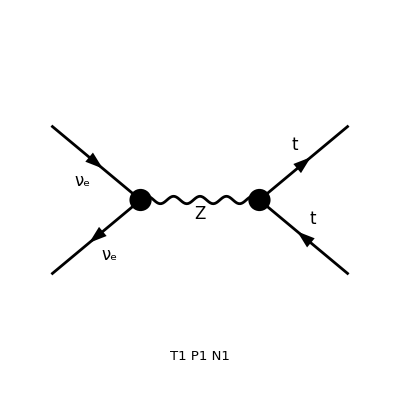

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],-F[1,{1}]}->{F[3,{3}],-F[3,{3}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{-F[1,{1}],k[2],0,{0,-LeptonNumber}}}→{{F[3,{3,Col3}],k[3],MT,{(2 Charge)/3,(2 ColorCharge)/(√3)}},{-F[3,{3,Col4}],k[4],MT,{-(2 Charge)/3,-(2 ColorCharge)/(√3)}}}][-4 Alfa gLnu gRu π Den[2 Pair[k[1],k[2]],mz2] Mat[F1 SUN1]-4 Alfa gLnu gLu π Den[2 Pair[k[1],k[2]],mz2] Mat[F2 SUN1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 4 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^2*squaredAmp*chiz*Conjugate[chiz]*(s12-mz2)*(s12-Conjugate[mz2])//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

192 Alfa2 chiz gLnu π^2 chiz^* gLnu^* ((gRf mfsq s12+gLf (s12-s13)^2) gLf^*+(gLf mfsq s12+gRf s13^2) gRf^*)

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

192*Alfa2*chiz*gLnu*conj(chiz)*conj(gLnu)*pow(Pi,2)*
   (conj(gLf)*(gRf*mfsq*s12 + gLf*pow(s12 - s13,2)) + conj(gRf)*(gLf*mfsq*s12 + gRf*pow(s13,2)))

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.2) LO Squared Amplitude calculation nu1 nu1 > nu1 nu1

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 2 Particles insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

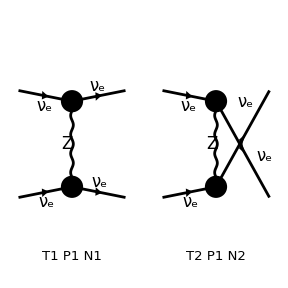

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],F[1,{1}]}->{F[1,{1}],F[1,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{F[1,{1}],k[2],0,{0,LeptonNumber}}}→{{F[1,{1}],k[3],0,{0,LeptonNumber}},{F[1,{1}],k[4],0,{0,LeptonNumber}}}][8 Alfa gLnu^2 π (Den[-2 Pair[k[1],k[3]],mz2]+Den[-2 Pair[k[1],k[4]],mz2]) Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 s12^2 (2 mz2+s12) (gLnu^*)^2 (s12+2 mz2^*))/((mz2+s12-s13) (mz2+s13) (s12-s13+mz2^*) (s13+mz2^*))

```mathematica
CForm[ans/.Alfa2->ALPHA*Conjugate[ALPHA]]/.Conjugate->conj/.Power->pow/.mz2->MZ2C/.Pi->pi
```

64*ALPHA*(2*MZ2C + s12)*conj(ALPHA)*(s12 + 2*conj(MZ2C))*pow(gLnu,2)*pow(pi,2)*pow(s12,2)*
   pow(MZ2C + s12 - s13,-1)*pow(MZ2C + s13,-1)*pow(conj(gLnu),2)*pow(s12 - s13 + conj(MZ2C),-1)*
   pow(s13 + conj(MZ2C),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

```mathematica
64/4
```

16

### 2.3) LO Squared Amplitude calculation nu1 nu2 > nu1 nu2

loading generic model file /Users/rhorry/Research/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/rhorry/Research/FeynArts-3.11/Models/SMQCD.mod

loading classes model file /Users/rhorry/Research/FeynArts-3.11/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

in total: 1 Particles insertion

> Top. 1 aebf/cedf/ef.m, 0 diagrams

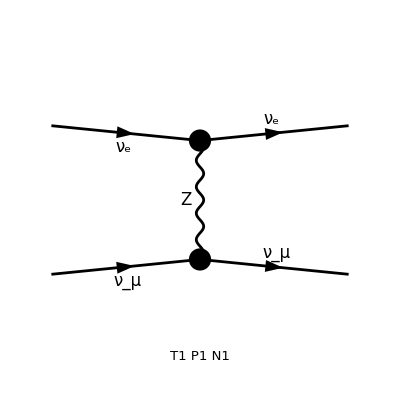

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],F[1,{2}]}->{F[1,{1}],F[1,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{F[1,{2}],k[2],0,{0,LeptonNumber}}}→{{F[1,{1}],k[3],0,{0,LeptonNumber}},{F[1,{2}],k[4],0,{0,LeptonNumber}}}][8 Alfa gLnu^2 π Den[-2 Pair[k[1],k[3]],mz2] Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 s12^2 (gLnu^*)^2)/((mz2+s13) (s13+mz2^*))

```mathematica
CForm[ans/.Alfa2->ALPHA*Conjugate[ALPHA]]/.Conjugate->conj/.Power->pow/.mz2->MZ2C/.Pi->pi
```

64*ALPHA*conj(ALPHA)*pow(gLnu,2)*pow(pi,2)*pow(s12,2)*pow(MZ2C + s13,-1)*pow(conj(gLnu),2)*
   pow(s13 + conj(MZ2C),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.4) LO Squared Amplitude calculation nu1 nu2bar > nu1 nu2bar

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

in total: 1 Particles insertion

> Top. 1 aebf/cedf/ef.m, 0 diagrams

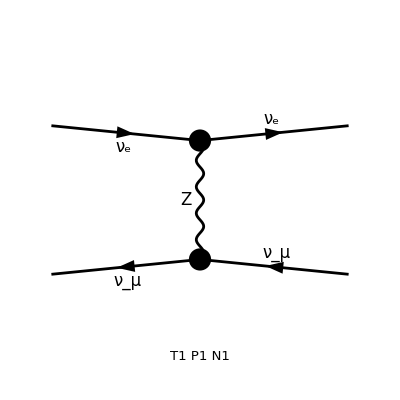

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],-F[1,{2}]}->{F[1,{1}],-F[1,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{-F[1,{2}],k[2],0,{0,-LeptonNumber}}}→{{F[1,{1}],k[3],0,{0,LeptonNumber}},{-F[1,{2}],k[4],0,{0,-LeptonNumber}}}][-4 Alfa gLnu^2 π Den[-2 Pair[k[1],k[3]],mz2] Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 (s12-s13)^2 (gLnu^*)^2)/((mz2+s13) (s13+mz2^*))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

64*Alfa2*pow(gLnu,2)*pow(Pi,2)*pow(s12 - s13,2)*pow(mz2 + s13,-1)*pow(conj(gLnu),2)*
   pow(s13 + conj(mz2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.5) LO Squared Amplitude calculation nu1bar nu2 > nu1bar nu2

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

in total: 1 Particles insertion

> Top. 1 aebf/cedf/ef.m, 0 diagrams

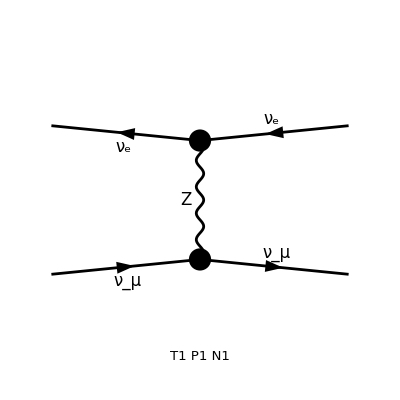

```mathematica
insertFields=InsertFields[topsLO,{-F[1,{1}],F[1,{2}]}->{-F[1,{1}],F[1,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{-F[1,{1}],k[1],0,{0,-LeptonNumber}},{F[1,{2}],k[2],0,{0,LeptonNumber}}}→{{-F[1,{1}],k[3],0,{0,-LeptonNumber}},{F[1,{2}],k[4],0,{0,LeptonNumber}}}][-4 Alfa gLnu^2 π Den[-2 Pair[k[1],k[3]],mz2] Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 (s12-s13)^2 (gLnu^*)^2)/((mz2+s13) (s13+mz2^*))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

64*Alfa2*pow(gLnu,2)*pow(Pi,2)*pow(s12 - s13,2)*pow(mz2 + s13,-1)*pow(conj(gLnu),2)*
   pow(s13 + conj(mz2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.6) LO Squared Amplitude calculation nu1 nu1bar > nu1 nu1bar

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

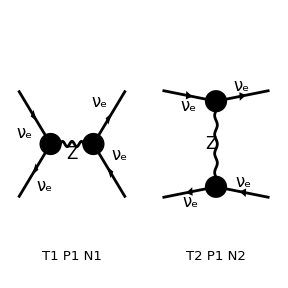

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],-F[1,{1}]}->{F[1,{1}],-F[1,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{-F[1,{1}],k[2],0,{0,-LeptonNumber}}}→{{F[1,{1}],k[3],0,{0,LeptonNumber}},{-F[1,{1}],k[4],0,{0,-LeptonNumber}}}][-4 Alfa gLnu^2 π (Den[2 Pair[k[1],k[2]],mz2]+Den[-2 Pair[k[1],k[3]],mz2]) Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 (s12-s13)^2 (2 mz2-s12+s13) (gLnu^*)^2 (s12-s13-2 mz2^*))/((mz2-s12) (mz2+s13) (s12-mz2^*) (s13+mz2^*))

```mathematica
CForm[ans/.Alfa2->ALPHA*Conjugate[ALPHA]]/.Conjugate->conj/.Power->pow/.mz2->MZ2C/.Pi->pi
```

64*ALPHA*(2*MZ2C - s12 + s13)*conj(ALPHA)*(s12 - s13 - 2*conj(MZ2C))*pow(gLnu,2)*pow(pi,2)*
   pow(MZ2C - s12,-1)*pow(s12 - s13,2)*pow(MZ2C + s13,-1)*pow(conj(gLnu),2)*pow(s12 - conj(MZ2C),-1)*
   pow(s13 + conj(MZ2C),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

## 2. neutrino-neutrino interactions nlo:

### 2.2) NLO Squared Amplitude calculation nu1 nu1 > nu1 nu1

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 2 Particles insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

-Graphics-

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 1 Particles insertion

> Top. 8: 1 Particles insertion

> Top. 9: 10 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

in total: 12 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebf/cgdh/egehfgfh.m, 0 diagrams

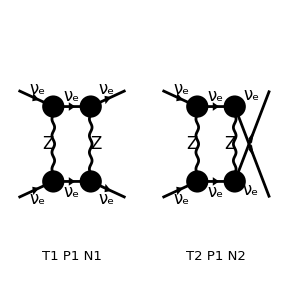

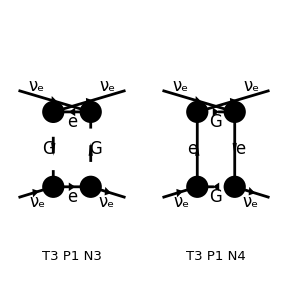

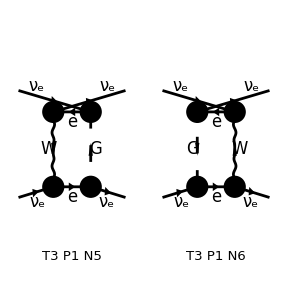

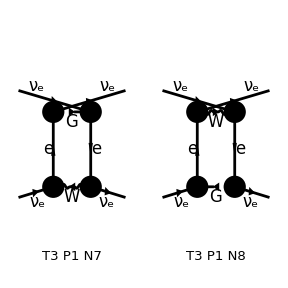

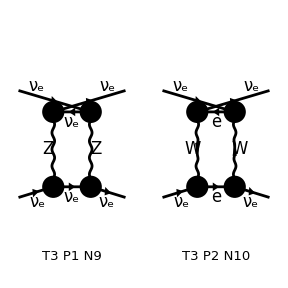

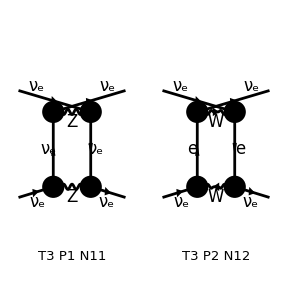

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 7 Particles insertions

> Top. 3: 7 Particles insertions

> Top. 4: 7 Particles insertions

> Top. 5: 7 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

in total: 28 Particles insertions

> Top. 1 aebf/cedg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cfdg/fhegehgh.m, 0 diagrams

> Top. 3 aebf/cgde/ehfgfhgh.m, 0 diagrams

> Top. 4 aebf/cgdf/fhegehgh.m, 0 diagrams

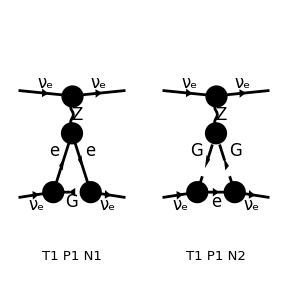

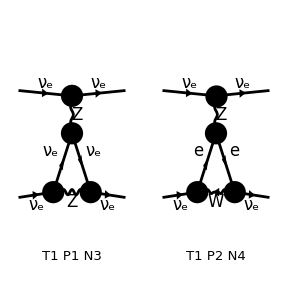

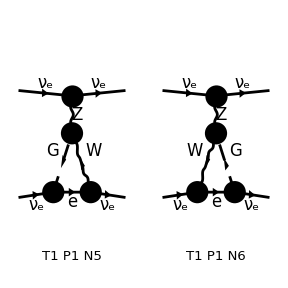

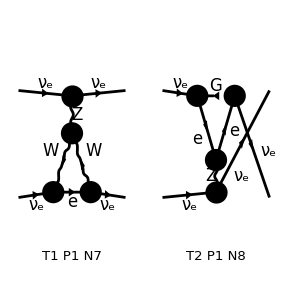

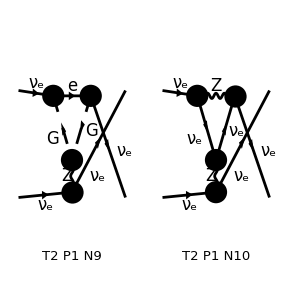

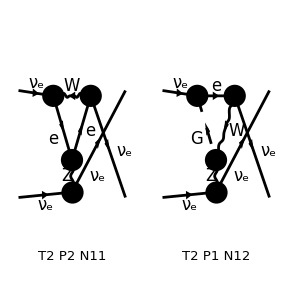

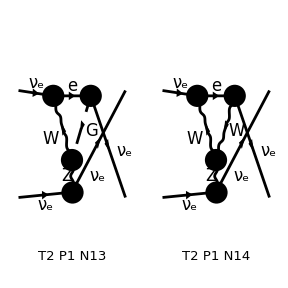

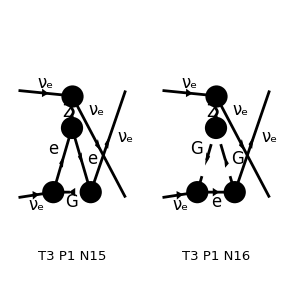

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 4 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

> Top. 26: 0 Particles insertions

> Top. 27: 20 Particles insertions

> Top. 28: 3 Particles insertions

> Top. 29: 3 Particles insertions

> Top. 30: 20 Particles insertions

> Top. 31: 3 Particles insertions

> Top. 32: 3 Particles insertions

> Top. 33: 3 Particles insertions

> Top. 34: 3 Particles insertions

> Top. 35: 3 Particles insertions

> Top. 36: 3 Particles insertions

> Top. 37: 0 Particles insertions

> Top. 38: 0 Particles insertions

in total: 72 Particles insertions

> Top. 1 aebf/cedf/egfggg.m, 0 diagrams

> Top. 2 aebf/cfde/egfggg.m, 0 diagrams

> Top. 3 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 4 aebf/cedg/effhghgh.m, 0 diagrams

> Top. 5 aebf/cedg/egghfhfh.m, 0 diagrams

> Top. 6 aebf/cfde/egfhghgh.m, 0 diagrams

> Top. 7 aebf/cfdg/efehghgh.m, 0 diagrams

> Top. 8 aebf/cfdg/fggheheh.m, 0 diagrams

> Top. 9 aebf/cgde/effhghgh.m, 0 diagrams

> Top. 10 aebf/cgde/egghfhfh.m, 0 diagrams

> Top. 11 aebf/cgdf/efehghgh.m, 0 diagrams

> Top. 12 aebf/cgdf/fggheheh.m, 0 diagrams

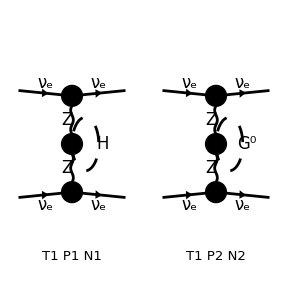

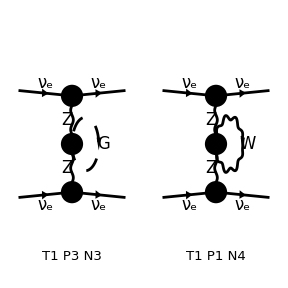

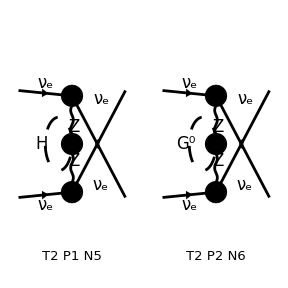

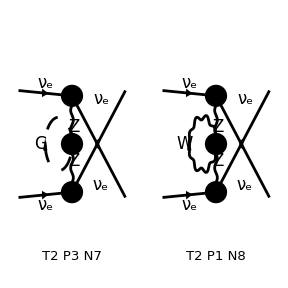

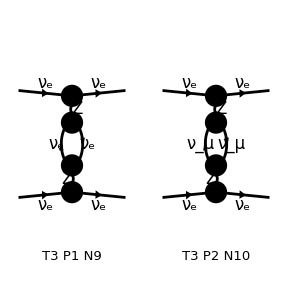

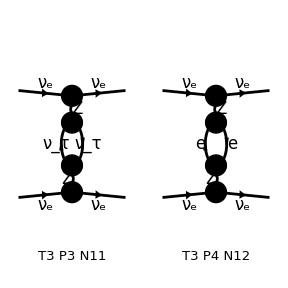

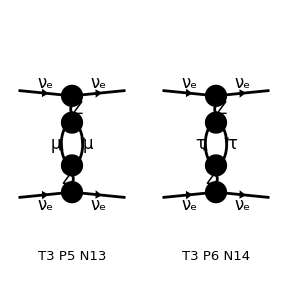

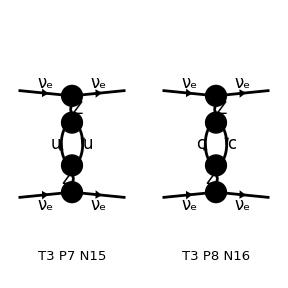

```mathematica
(**)
insertFieldsTree=InsertFields[topsLO,{F[1,{1}],F[1,{1}]}->{F[1,{1}],F[1,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldsTree,ColumnsXRows->{2,1}];
(**)
insertFieldsBox=InsertFields[topsBox,{F[1,{1}],F[1,{1}]}->{F[1,{1}],F[1,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldsBox,ColumnsXRows->{2,1}];
(**)
insertFieldsTri=InsertFields[topsTri,{F[1,{1}],F[1,{1}]}->{F[1,{1}],F[1,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldsTri,ColumnsXRows->{2,1}];
(**)
insertFieldsSelf=InsertFields[topsSelf,{F[1,{1}],F[1,{1}]}->{F[1,{1}],F[1,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldsSelf,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFieldsTree];
feynampBox=CreateFeynAmp[insertFieldsBox];
feynampTri=CreateFeynAmp[insertFieldsTri];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 10 Particles amplitudes

in total: 12 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 7 Particles amplitudes

> Top. 3: 7 Particles amplitudes

> Top. 4: 7 Particles amplitudes

in total: 28 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
AmplitudeBox=CalcFeynAmp[feynampBox,FermionChains->Chiral,Invariants->False,PaVeReduce->True]/.MZ2->mz2/.MW2->mw2;
AmplitudeTri=CalcFeynAmp[feynampTri,FermionChains->Chiral,Invariants->False,PaVeReduce->True]/.MZ2->mz2/.MW2->mw2;
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{F[1,{1}],k[2],0,{0,LeptonNumber}}}→{{F[1,{1}],k[3],0,{0,LeptonNumber}},{F[1,{1}],k[4],0,{0,LeptonNumber}}}][8 Alfa gLnu^2 π (Den[-2 Pair[k[1],k[3]],mz2]+Den[-2 Pair[k[1],k[4]],mz2]) Mat[F1]]

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

```mathematica
squaredAmpBox=PolarizationSum[AmplitudeLO,AmplitudeBox,GaugeTerms->False];
prefacBox=Alfa*Alfa2*Conjugate[gLnu^2]*Pi*(s12+2* Conjugate[mz2])/(s13+ Conjugate[mz2])
ansBox=Collect[2^4*squaredAmpBox/prefacBox//.Abbr[]//.Subexpr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->0/.m4sq->0/.IGram[a_]:>1/a,{B0i[__],C0i[__],D0i[__],gLnu},Simplify]
```

```mathematica
squaredAmpTri=PolarizationSum[AmplitudeLO,AmplitudeTri,GaugeTerms->False];
prefacTri=Alfa*Alfa2*Conjugate[gLnu^2]*Pi*(s12+2* Conjugate[mz2])/(s13+ Conjugate[mz2]);
ansTri=Collect[2^4*squaredAmpTri/prefacTri//.Abbr[]//.Subexpr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->0/.m4sq->0/.IGram[a_]:>1/a,{A0[__],B0i[__],C0i[__],D0i[__],gLnu},Simplify]
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

(32 gLnu^4 s12^2 (-2 mz2+3 s13) B0i[bb0,-s13,0,0])/(s13 (mz2+s13) (-s12+s13-mz2^*))+(8 gLnu s12^2 (gRe ME2 (2 ME2-2 mw2-s13)+2 gLe mw2 (2 ME2-2 mw2+3 s13)) B0i[bb0,-s13,ME2,ME2])/(mw2 s13 (mz2+s13) sw2 (-s12+s13-mz2^*))+(4 gLnu s12^2 (cw2 ME2 (2 ME2-2 mw2-s13)+4 CW2 mw2 (2 ME2-2 mw2+s13)+ME2 (-2 ME2+2 mw2+s13) sw2) B0i[bb0,-s13,mw2,mw2])/(CW mw2 s13 (mz2+s13) SW sw2 (-s12+s13-mz2^*))+(8 gLnu s12^2 (4 CW2 mw2 (ME2^2-2 ME2 mw2+mw2 (mw2-2 s13))+cw2 ME2 (ME2^2+mw2^2-ME2 (2 mw2+s13))-ME2 (ME2^2-ME2 (2 mw2+s13)+mw2 (mw2+4 s13)) sw2) C0i[cc0,0,-s13,0,ME2,mw2,mw2])/(CW mw2 s13 (mz2+s13) SW sw2 (-s12+s13-mz2^*))-(64 gLnu^4 s12^2 (mz2-s13)^2 C0i[cc0,-s13,0,0,0,0,mz2])/(s13 (mz2+s13) (-s12+s13-mz2^*))-(16 gLnu s12^2 (gRe ME2 (ME2^2-2 ME2 mw2+mw2 (mw2-2 s13))+gLe (-4 ME2 mw2 (mw2-s13)+2 mw2 (mw2-s13)^2+ME2^2 (2 mw2-s13))) C0i[cc0,-s13,0,0,ME2,ME2,mw2])/(mw2 s13 (mz2+s13) sw2 (-s12+s13-mz2^*))-(64 Finite gLnu^4 s12^2 (2 mz2+s12))/((mz2+s12-s13) (mz2+s13) (s12-s13+mz2^*))-(4 Finite gLnu s12^2 (2 mz2+s12) (-cw2 ME2+2 CW (gRe ME2+4 gLe mw2) SW+ME2 sw2))/(CW mw2 (mz2+s12-s13) (mz2+s13) SW sw2 (s12-s13+mz2^*))-(64 gLnu^4 s12^2 (mz2^2 s12+2 s12 s13 (-s12+s13)+mz2 (s12^2-6 s12 s13+6 s13^2)) B0i[bb0,0,0,mz2])/((s12-s13) (mz2+s12-s13) s13 (mz2+s13) (s12-s13+mz2^*))+(8 gLnu s12^2 (cw2 ME2 (ME2-mw2) (mz2 s12+s12^2-2 s12 s13+2 s13^2)+4 CW2 mw2 (2 (2 mz2+s12) (s12-s13) s13+ME2 (mz2 s12+s12^2-2 s12 s13+2 s13^2)-mw2 (mz2 s12+s12^2-2 s12 s13+2 s13^2))+2 CW gRe ME2^2 mz2 s12 SW+4 CW gLe ME2 mw2 mz2 s12 SW-2 CW gRe ME2 mw2 mz2 s12 SW-4 CW gLe mw2^2 mz2 s12 SW+2 CW gRe ME2^2 s12^2 SW+4 CW gLe ME2 mw2 s12^2 SW-2 CW gRe ME2 mw2 s12^2 SW-4 CW gLe mw2^2 s12^2 SW-4 CW gRe ME2^2 s12 s13 SW-8 CW gLe ME2 mw2 s12 s13 SW+4 CW gRe ME2 mw2 s12 s13 SW+8 CW gLe mw2^2 s12 s13 SW+16 CW gLe mw2 mz2 s12 s13 SW+8 CW gLe mw2 s12^2 s13 SW+4 CW gRe ME2^2 s13^2 SW+8 CW gLe ME2 mw2 s13^2 SW-4 CW gRe ME2 mw2 s13^2 SW-8 CW gLe mw2^2 s13^2 SW-16 CW gLe mw2 mz2 s13^2 SW-8 CW gLe mw2 s12 s13^2 SW-ME2^2 mz2 s12 sw2+ME2 mw2 mz2 s12 sw2-ME2^2 s12^2 sw2+ME2 mw2 s12^2 sw2+2 ME2^2 s12 s13 sw2-2 ME2 mw2 s12 s13 sw2-2 ME2^2 s13^2 sw2+2 ME2 mw2 s13^2 sw2) B0i[bb0,0,ME2,mw2])/(CW mw2 (s12-s13) (mz2+s12-s13) s13 (mz2+s13) SW sw2 (s12-s13+mz2^*))+(32 gLnu^4 s12^2 (2 mz2-3 s12+3 s13) B0i[bb0,-s12+s13,0,0])/((s12-s13) (mz2+s12-s13) (s12-s13+mz2^*))+(8 gLnu s12^2 (gRe ME2 (-2 ME2+2 mw2+s12-s13)+2 gLe mw2 (-2 ME2+2 mw2-3 s12+3 s13)) B0i[bb0,-s12+s13,ME2,ME2])/(mw2 (s12-s13) (mz2+s12-s13) sw2 (s12-s13+mz2^*))+(4 gLnu s12^2 (cw2 ME2 (-2 ME2+2 mw2+s12-s13)+4 CW2 mw2 (-2 ME2+2 mw2-s12+s13)+ME2 (2 ME2-2 mw2-s12+s13) sw2) B0i[bb0,-s12+s13,mw2,mw2])/(CW mw2 (s12-s13) (mz2+s12-s13) SW sw2 (s12-s13+mz2^*))-(8 gLnu s12^2 (cw2 ME2 (ME2^2+mw2^2+ME2 (-2 mw2-s12+s13))+4 CW2 mw2 (ME2^2-2 ME2 mw2+mw2 (mw2-2 s12+2 s13))-ME2 (ME2^2+mw2 (mw2+4 s12-4 s13)+ME2 (-2 mw2-s12+s13)) sw2) C0i[cc0,0,-s12+s13,0,ME2,mw2,mw2])/(CW mw2 (s12-s13) (mz2+s12-s13) SW sw2 (s12-s13+mz2^*))+(64 gLnu^4 s12^2 (mz2-s12+s13)^2 C0i[cc0,-s12+s13,0,0,0,0,mz2])/((s12-s13) (mz2+s12-s13) (s12-s13+mz2^*))+(16 gLnu s12^2 (gLe (-4 ME2 mw2 (mw2-s12+s13)+2 mw2 (mw2-s12+s13)^2+ME2^2 (2 mw2-s12+s13))+gRe ME2 (ME2^2-2 ME2 mw2+mw2 (mw2-2 s12+2 s13))) C0i[cc0,-s12+s13,0,0,ME2,ME2,mw2])/(mw2 (s12-s13) (mz2+s12-s13) sw2 (s12-s13+mz2^*))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

64*Alfa2*(2*mz2 + s12)*(s12 + 2*conj(mz2))*pow(gLnu,2)*pow(Pi,2)*pow(s12,2)*pow(mz2 + s12 - s13,-1)*
   pow(mz2 + s13,-1)*pow(conj(gLnu),2)*pow(s12 - s13 + conj(mz2),-1)*pow(s13 + conj(mz2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.3) NLO Squared Amplitude calculation nu1 nu2 > nu1 nu2

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 7 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 7 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 1 Particles insertion

> Top. 14: 0 Particles insertions

> Top. 15: 5 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

> Top. 26: 0 Particles insertions

> Top. 27: 0 Particles insertions

> Top. 28: 0 Particles insertions

> Top. 29: 4 Particles insertions

> Top. 30: 0 Particles insertions

> Top. 31: 0 Particles insertions

> Top. 32: 0 Particles insertions

> Top. 33: 0 Particles insertions

> Top. 34: 0 Particles insertions

> Top. 35: 0 Particles insertions

> Top. 36: 0 Particles insertions

> Top. 37: 0 Particles insertions

> Top. 38: 0 Particles insertions

> Top. 39: 0 Particles insertions

> Top. 40: 0 Particles insertions

> Top. 41: 0 Particles insertions

> Top. 42: 0 Particles insertions

> Top. 43: 0 Particles insertions

> Top. 44: 0 Particles insertions

> Top. 45: 0 Particles insertions

> Top. 46: 0 Particles insertions

> Top. 47: 0 Particles insertions

> Top. 48: 0 Particles insertions

> Top. 49: 0 Particles insertions

> Top. 50: 0 Particles insertions

> Top. 51: 0 Particles insertions

> Top. 52: 0 Particles insertions

> Top. 53: 0 Particles insertions

> Top. 54: 0 Particles insertions

> Top. 55: 0 Particles insertions

> Top. 56: 0 Particles insertions

> Top. 57: 0 Particles insertions

> Top. 58: 0 Particles insertions

> Top. 59: 0 Particles insertions

> Top. 60: 0 Particles insertions

> Top. 61: 0 Particles insertions

> Top. 62: 0 Particles insertions

> Top. 63: 20 Particles insertions

> Top. 64: 3 Particles insertions

> Top. 65: 3 Particles insertions

> Top. 66: 0 Particles insertions

> Top. 67: 0 Particles insertions

> Top. 68: 0 Particles insertions

> Top. 69: 0 Particles insertions

> Top. 70: 0 Particles insertions

> Top. 71: 3 Particles insertions

> Top. 72: 3 Particles insertions

> Top. 73: 0 Particles insertions

> Top. 74: 0 Particles insertions

in total: 56 Particles insertions

> Top. 1 aebf/cedg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdf/fhegehgh.m, 0 diagrams

> Top. 3 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 4 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 5 aebf/cedf/egfggg.m, 0 diagrams

> Top. 6 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 7 aebf/cedg/effhghgh.m, 0 diagrams

> Top. 8 aebf/cedg/egghfhfh.m, 0 diagrams

> Top. 9 aebf/cgdf/efehghgh.m, 0 diagrams

> Top. 10 aebf/cgdf/fggheheh.m, 0 diagrams

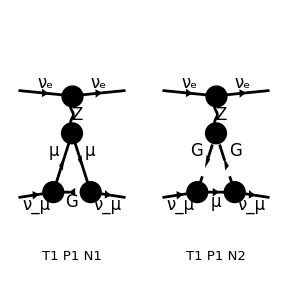

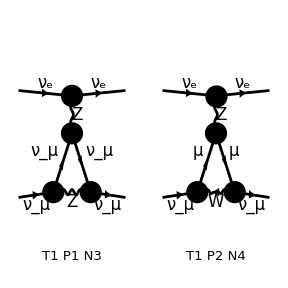

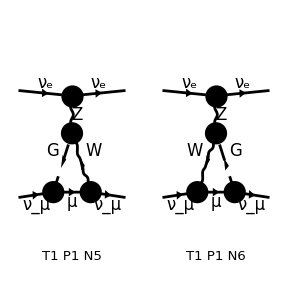

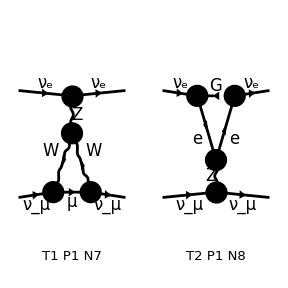

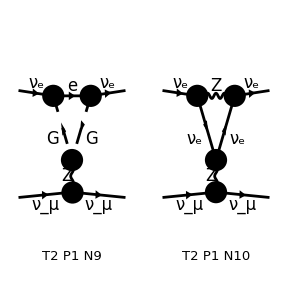

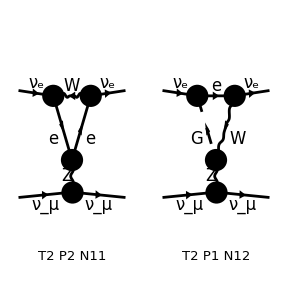

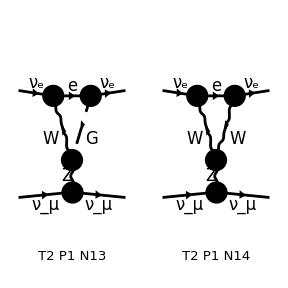

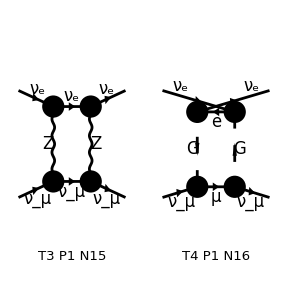

```mathematica
insertFields=InsertFields[topsV,{F[1,{1}],F[1,{2}]}->{F[1,{1}],F[1,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{F[1,{2}],k[2],0,{0,LeptonNumber}}}→{{F[1,{1}],k[3],0,{0,LeptonNumber}},{F[1,{2}],k[4],0,{0,LeptonNumber}}}][8 Alfa gLnu^2 π Den[-2 Pair[k[1],k[3]],mz2] Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 s12^2 (gLnu^*)^2)/((mz2+s13) (s13+mz2^*))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

64*Alfa2*pow(gLnu,2)*pow(Pi,2)*pow(s12,2)*pow(mz2 + s13,-1)*pow(conj(gLnu),2)*pow(s13 + conj(mz2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.4) LO Squared Amplitude calculation nu1 nu2bar > nu1 nu2bar

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],-F[1,{2}]}->{F[1,{1}],-F[1,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

in total: 1 Particles insertion

> Top. 1 aebf/cedf/ef.m, 0 diagrams

-Graphics-

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{-F[1,{2}],k[2],0,{0,-LeptonNumber}}}→{{F[1,{1}],k[3],0,{0,LeptonNumber}},{-F[1,{2}],k[4],0,{0,-LeptonNumber}}}][-4 Alfa gLnu^2 π Den[-2 Pair[k[1],k[3]],mz2] Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 (s12-s13)^2 (gLnu^*)^2)/((mz2+s13) (s13+mz2^*))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

64*Alfa2*pow(gLnu,2)*pow(Pi,2)*pow(s12 - s13,2)*pow(mz2 + s13,-1)*pow(conj(gLnu),2)*
   pow(s13 + conj(mz2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.5) LO Squared Amplitude calculation nu1bar nu2 > nu1bar nu2

```mathematica
insertFields=InsertFields[topsLO,{-F[1,{1}],F[1,{2}]}->{-F[1,{1}],F[1,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

in total: 1 Particles insertion

> Top. 1 aebf/cedf/ef.m, 0 diagrams

-Graphics-

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{-F[1,{1}],k[1],0,{0,-LeptonNumber}},{F[1,{2}],k[2],0,{0,LeptonNumber}}}→{{-F[1,{1}],k[3],0,{0,-LeptonNumber}},{F[1,{2}],k[4],0,{0,LeptonNumber}}}][-4 Alfa gLnu^2 π Den[-2 Pair[k[1],k[3]],mz2] Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 (s12-s13)^2 (gLnu^*)^2)/((mz2+s13) (s13+mz2^*))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

64*Alfa2*pow(gLnu,2)*pow(Pi,2)*pow(s12 - s13,2)*pow(mz2 + s13,-1)*pow(conj(gLnu),2)*
   pow(s13 + conj(mz2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```